Project2,Poincaré Normal Form method 
Pietro De Checchi, Gaia Marangon

__________________________________________________________________
Preliminaries: functions for polynomial substitution with truncation
==========================================================

```mathematica
(*POLYNOMIAL MULTIPLICATION, TRUNCATED AT ORDER nTrunc, IN 2 VARIABLES*)
Multipl 2v[p1_,p2_,nTrunc_] := Module[{},
(*Handle case: one (or both) polyn is zero*)
If[p1==0 || p2==0,
Return[0, Module];
];
(*Get info for first polynomial *)
p1Degx = Exponent[p1,x];
p1Degy = Exponent[p1,y];
p1DegTot =Max[Map[Exponent[#,x]+Exponent[#,y]&,MonomialList[p1]]];
p1CoeffList = CoefficientList[p1,{x,y}];
(*Get info for second polynomial *)
p2Degx = Exponent[p2,x];
p2Degy = Exponent[p2,y];
p2DegTot =Max[Map[Exponent[#,x]+Exponent[#,y]&,MonomialList[p2]]];
p2CoeffList = CoefficientList[p2,{x,y}];

(*Compose product*)
Sum[
Sum[
(*Inizio coefficienti*)
Sum[
Sum[
p1CoeffList[[i+1]][[j+1]] * p2CoeffList[[I-i+1]][[(L-I)-j+1]] (*+1 perché Mthm conta da 1 e non da 0*) 
,{j,Max[0, (L-I)-p2Degy],Min[L-I,p1Degy]}]
,{i, Max[0, I-p2Degx], Min[I,p1Degx]}]
(*Fine coefficienti*)
*x^I * y^(L-I)
,{I,Max[0, L-(p1Degy+p2Degy)], Min[L,p1Degx+p2Degx ]}]
,{L,0,Min[nTrunc, p1Degx+p2Degx+p1Degy+p2Degy]}] //Expand
]
```

```mathematica
(*POLYNOMIAL POWER, TRUNCATED AT ORDER nTrunc, IN 2 VARIABLES*)
Pow 2v[p_,expon_, nTrunc_]:= NestList[Multipl 2v[#,p,nTrunc]& ,p/. x^w_ /; w>nTrunc->0,expon-1]//Expand
```

```mathematica
(*POLYNOMIAL SUBSTITUTION, TRUNCATED AT ORDER nTrunc, IN 2 VARIABLES*)PolynSubst 2v[poli0_,poli1_,poli2_,nTrunc_] := Module[{},
(*Given polynomial poli0(X,Y) compute it in X=poli1(x,y), Y=poli2(x,y), truncating efficiently at nTrunc*)
(*Extract maximum power at which poli1 and poli2 will appear*)
maxpow1 = Exponent[poli0, X];
maxpow2 = Exponent[poli0, Y];
(*List all needed powers of poli1 and poli2 via truncated method*)
poli1 powList = Flatten[{1,Pow 2v[poli1,maxpow1,nTrunc]}];
poli2 powList = Flatten[{1,Pow 2v[poli2,maxpow2,nTrunc]}];
(*Rewrite poli0 as polynomial of poli1,poli2*)
poli0 new = Total[MonomialList[poli0, {X,Y}]];
(*Do[Print[poli0 new[[i]]],{i,1,Length[poli0 new ]}] *)
(*Combine powers in desired polynomial to get poli0*)
mySum = 0;
Do[
monomial = poli0 new[[a]];
(*Print[monomial /.{X->1,Y->1}];*) (*Coefficient*)
(*Print[Exponent[monomial,X]];*) (*Power of poli1*)
(*Print[Exponent[monomial,Y]];*) (*Power of poli2*)
mySum = mySum+(monomial /.{X->1,Y->1})*Multipl 2v[
 poli1 powList[[Exponent[monomial,X]+1]],
 poli2 powList[[Exponent[monomial,Y]+1]],
nTrunc];
,{a,1,Length[poli0 new ]}];
mypoli0 = Total[MonomialList[mySum, {x,y}]] 
]
```

__________________________________________________________________
Equations of motion
==========================================================

```mathematica
difx=v
difv=(-ω0^2(1+mbk*ε*Cos[ω t])(x-mbk*x^3/6))//TrigToExp//Expand
```

v

-x ω0^2+1/6 mbk x^3 ω0^2-1/2 ⅇ^(-ⅈ t ω) mbk x ε ω0^2-1/2 ⅇ^(ⅈ t ω) mbk x ε ω0^2+1/12 ⅇ^(-ⅈ t ω) mbk^2 x^3 ε ω0^2+1/12 ⅇ^(ⅈ t ω) mbk^2 x^3 ε ω0^2

__________________________________________________________________
Transformation of the equations of motion into the linear 
normal mode (diagonal) variables
==========================================================

```mathematica
xvsolveqp={x->(q+p)/Sqrt[2*ω0],v->I*Sqrt[ω0/2]*(q-p)}
qpsolvexv=Solve[{x==(q+p)/Sqrt[2*ω0],v==I*Sqrt[ω0/2]*(q-p)},{q,p}][[1]]//Expand//Simplify 
difq=(q/.qpsolvexv/.{x->difx,v->difv}//Expand)/.xvsolveqp//Expand//TrigToExp 
difp=(p/.qpsolvexv/.{x->difx,v->difv}//Expand)/.xvsolveqp//Expand//TrigToExp 
q*p/.qpsolvexv//Expand
```

{x→(p+q)/(√2 √ω0),v→(ⅈ (-p+q) √ω0)/(√2)}

{q→(-ⅈ v+x ω0)/(√2 √ω0),p→(ⅈ v+x ω0)/(√2 √ω0)}

-1/24 ⅈ mbk p^3-1/8 ⅈ mbk p^2 q-1/8 ⅈ mbk p q^2-1/24 ⅈ mbk q^3-1/48 ⅈ ⅇ^(-ⅈ t ω) mbk^2 p^3 ε-1/48 ⅈ ⅇ^(ⅈ t ω) mbk^2 p^3 ε-1/16 ⅈ ⅇ^(-ⅈ t ω) mbk^2 p^2 q ε-1/16 ⅈ ⅇ^(ⅈ t ω) mbk^2 p^2 q ε-1/16 ⅈ ⅇ^(-ⅈ t ω) mbk^2 p q^2 ε-1/16 ⅈ ⅇ^(ⅈ t ω) mbk^2 p q^2 ε-1/48 ⅈ ⅇ^(-ⅈ t ω) mbk^2 q^3 ε-1/48 ⅈ ⅇ^(ⅈ t ω) mbk^2 q^3 ε+ⅈ q ω0+1/4 ⅈ ⅇ^(-ⅈ t ω) mbk p ε ω0+1/4 ⅈ ⅇ^(ⅈ t ω) mbk p ε ω0+1/4 ⅈ ⅇ^(-ⅈ t ω) mbk q ε ω0+1/4 ⅈ ⅇ^(ⅈ t ω) mbk q ε ω0

1/24 ⅈ mbk p^3+1/8 ⅈ mbk p^2 q+1/8 ⅈ mbk p q^2+1/24 ⅈ mbk q^3+1/48 ⅈ ⅇ^(-ⅈ t ω) mbk^2 p^3 ε+1/48 ⅈ ⅇ^(ⅈ t ω) mbk^2 p^3 ε+1/16 ⅈ ⅇ^(-ⅈ t ω) mbk^2 p^2 q ε+1/16 ⅈ ⅇ^(ⅈ t ω) mbk^2 p^2 q ε+1/16 ⅈ ⅇ^(-ⅈ t ω) mbk^2 p q^2 ε+1/16 ⅈ ⅇ^(ⅈ t ω) mbk^2 p q^2 ε+1/48 ⅈ ⅇ^(-ⅈ t ω) mbk^2 q^3 ε+1/48 ⅈ ⅇ^(ⅈ t ω) mbk^2 q^3 ε-ⅈ p ω0-1/4 ⅈ ⅇ^(-ⅈ t ω) mbk p ε ω0-1/4 ⅈ ⅇ^(ⅈ t ω) mbk p ε ω0-1/4 ⅈ ⅇ^(-ⅈ t ω) mbk q ε ω0-1/4 ⅈ ⅇ^(ⅈ t ω) mbk q ε ω0

v^2/(2 ω0)+(x^2 ω0)/2

__________________________________________________________________
Initialize iterative loop: compute eigenvalues and define zeroth-order solution
==========================================================

```mathematica
λ1=Coefficient[difq,mbk,0]/q //Chop
λ2=Coefficient[difp,mbk,0]/p //Chop
```

ⅈ ω0

-ⅈ ω0

```mathematica
(*maximum order of expansions in the book-keeping parameter *)
nmax=3;
Clear[sol];

(*`zero-th order solution': here we introduce the original flow equations *)
sol[0]={
Table[{Fq[0][j]->Coefficient[difq,mbk,j],Fp[0][j]->Coefficient[difp,mbk,j]},{j,0,nmax}]/.{q->q[0],p->p[0]}}//Flatten
```

{Fq[0][0]→ⅈ ω0 q[0],Fp[0][0]→-ⅈ ω0 p[0],Fq[0][1]→1/4 ⅈ ⅇ^(-ⅈ t ω) ε ω0 p[0]+1/4 ⅈ ⅇ^(ⅈ t ω) ε ω0 p[0]-1/24 ⅈ p[0]^3+1/4 ⅈ ⅇ^(-ⅈ t ω) ε ω0 q[0]+1/4 ⅈ ⅇ^(ⅈ t ω) ε ω0 q[0]-1/8 ⅈ p[0]^2 q[0]-1/8 ⅈ p[0] q[0]^2-1/24 ⅈ q[0]^3,Fp[0][1]→-1/4 ⅈ ⅇ^(-ⅈ t ω) ε ω0 p[0]-1/4 ⅈ ⅇ^(ⅈ t ω) ε ω0 p[0]+1/24 ⅈ p[0]^3-1/4 ⅈ ⅇ^(-ⅈ t ω) ε ω0 q[0]-1/4 ⅈ ⅇ^(ⅈ t ω) ε ω0 q[0]+1/8 ⅈ p[0]^2 q[0]+1/8 ⅈ p[0] q[0]^2+1/24 ⅈ q[0]^3,Fq[0][2]→-1/48 ⅈ ⅇ^(-ⅈ t ω) ε p[0]^3-1/48 ⅈ ⅇ^(ⅈ t ω) ε p[0]^3-1/16 ⅈ ⅇ^(-ⅈ t ω) ε p[0]^2 q[0]-1/16 ⅈ ⅇ^(ⅈ t ω) ε p[0]^2 q[0]-1/16 ⅈ ⅇ^(-ⅈ t ω) ε p[0] q[0]^2-1/16 ⅈ ⅇ^(ⅈ t ω) ε p[0] q[0]^2-1/48 ⅈ ⅇ^(-ⅈ t ω) ε q[0]^3-1/48 ⅈ ⅇ^(ⅈ t ω) ε q[0]^3,Fp[0][2]→1/48 ⅈ ⅇ^(-ⅈ t ω) ε p[0]^3+1/48 ⅈ ⅇ^(ⅈ t ω) ε p[0]^3+1/16 ⅈ ⅇ^(-ⅈ t ω) ε p[0]^2 q[0]+1/16 ⅈ ⅇ^(ⅈ t ω) ε p[0]^2 q[0]+1/16 ⅈ ⅇ^(-ⅈ t ω) ε p[0] q[0]^2+1/16 ⅈ ⅇ^(ⅈ t ω) ε p[0] q[0]^2+1/48 ⅈ ⅇ^(-ⅈ t ω) ε q[0]^3+1/48 ⅈ ⅇ^(ⅈ t ω) ε q[0]^3,Fq[0][3]→0,Fp[0][3]→0}

__________________________________________________________________
Iterative loop: in every step (book-keeping order r=iord) define the 
transformation (polynomial coefficients cq and cp) as well as the new flow 
equations
==========================================================

```mathematica
Do[
(*---SET q,p TRANSFORM----------------------------------------------------*)
{t1,b1}=AbsoluteTiming[
Print["Order: ",iord];
tra[iord]={
q[iord-1]->q[iord]+eps^iord*Sum[   Sum[   Sum[ 
cq[m1,(2*iord+1 -2*ep)-m1,m3]*q[iord]^m1*p[iord]^((2*iord+1 -2*ep)-m1)*E^(ⅈ m3*ω t),
{m1,0,2*iord+1 -2*ep}],{m3, -ep,+ep,2}],{ep,0,iord}],
p[iord-1]->p[iord]+eps^iord*Sum[   Sum[   Sum[ 
cp[m1,(2*iord+1 -2*ep)-m1,m3]*q[iord]^m1*p[iord]^((2*iord+1 -2*ep)-m1)*E^(ⅈ m3*ω t),
{m1,0,2*iord+1 -2*ep}],{m3, -ep,+ep,2}],{ep,0,iord}]
}//Expand;

(*---Q EQUATION---------------------------------------------------------------------*)
(* 1. Imposing normal form, at all eps orders *)
(* 1.a Construct dotqtra via polynomial substitution with truncation*)
dotqtra atSol=(Sum[eps^j*Fq[iord-1][j],{j,0,nmax}]/.(Table[sol[j],{j,0,iord-1}]//Flatten))//Expand  //Chop;
dotqtra = PolynSubst 2v[
dotqtra atSol /.{q[iord-1]->X,p[iord-1]->Y} //Chop,
q[iord-1] /.tra[iord] /. {q[iord]->x, p[iord]->y} //Chop,
p[iord-1] /.tra[iord] /. {q[iord]->x, p[iord]->y} //Chop,
2*iord+1 (*=nTrunc*)
] /.{x->q[iord],y->p[iord]}//Chop;
(*    Rewrite dotqtra as polynomial of eps*)
dotqtra=Sum[eps^j*Coefficient[dotqtra,eps,j],{j,0,nmax}]//Expand //Chop;
(* 1.b Construct other terms of equation for q*)
dotqsol=(λ1*q[iord]+Sum[eps^j*Fq[iord][j],{j,1,nmax}])//Expand//Chop;
dotpsol=(λ2*p[iord]+Sum[eps^j*Fp[iord][j],{j,1,nmax}])//Expand//Chop;
dotqlhs=dotqsol*D[q[iord-1]/.tra[iord],q[iord]]+
dotpsol*D[q[iord-1]/.tra[iord],p[iord]]+
D[q[iord-1]/.tra[iord],t]//Expand //Chop;
dotqlhs=Sum[eps^j*Coefficient[dotqlhs,eps,j],{j,0,nmax}]//Expand//Chop;
qeq=dotqlhs-dotqtra;

(* 2. Consider equation at order eps=iord, to find the correct transformation *)
homonfq=Coefficient[qeq,eps,iord];

(*2.a Select "good" terms, that can be balanced*)
(*  - OPTION 1: for ω/ω0 not rational*)
homoq=Select[homonfq,
Exponent[#,q[iord]]!=Exponent[#,p[iord]]+1|| Exponent[#,ⅇ]/(ⅈ ω t )!=0&
]/.{Fq[w1_][w2_]->0,Fp[w1_][w2_]->0};
(*  - OPTION 2: for ω/ω0 generic, maybe not rational - but ω, ω0 must be values, not just symbols*)
(*homoq=Select[homonfq,
Exponent[#,ⅇ]/(ⅈ t )!=ω0 (Exponent[#,p[iord]]+1 -Exponent[#,q[iord]])&
]/.{Fq[w1_][w2_]->0,Fp[w1_][w2_]->0}*)

(*2.b.1 Get "bad" terms, that cannot be balanced*)
nfqsol=Solve[homonfq-homoq==0,Fq[iord][iord]][[1]] //Chop;

(*2.c Set to zero each monomial, to get the coefficients of the transformation *)

(*2.c.1  List all monomials of type Q^(...)P^(...)e^(...) and take their coefficients:*)
(*    -  List all possible exponents appearing in the good terms*)
expList =Union[Table[Exponent[homoq[[i]],ⅇ],{i,1,Length[homoq]}]];
(*    -  Exclude zero, Mathematica cannot take the coefficient of e^0*)
expList = DeleteCases[expList,0];
(*    -  For each e^(...), split its coefficient in monomials of type Q^(...)P^(...) and take their coeff*)
homoqterms =Table[     
MonomialList[Coefficient[homoq,ⅇ^expList[[i]]],{q[iord],p[iord]}]/. {q[iord]->1,p[iord]->1} 
 ,{i,1,Length[expList]}]//Flatten;
(*    -  For e^0, split its coefficient in monomials of type Q^(...)P^(...) and take their coeff*)
homoqterms = Append[homoqterms,
MonomialList[homoq/. ⅇ^(w_)->0,{q[iord],p[iord]}]/. {q[iord]->1,p[iord]->1}//Flatten
]//Flatten //Simplify ;

(*2.c.2 Isolate cq[...] variables from the coefficients of the monomials*)
cqterms=Table[((homoqterms[[i]]-(homoqterms[[i]]/.{cq[w1_,w2_,w3_]->0})//Simplify))/((homoqterms[[i]]-(homoqterms[[i]]/.{cq[w1_,w2_,w3_]->0})//Simplify)/.{cq[w1_,w2_,w3_]->1}),{i,1,Length[homoqterms]}] //Chop;

(*2.c.3 Set the coefficients to zero solving for the cq[...] variables*)
homoqsol=Solve[Table[homoqterms[[i]]==0,{i,1,Length[homoqterms]}],cqterms][[1]] //Chop;


(*---P EQUATION---------------------------------------------------------------------*)
(* 1. Imposing normal form, at all eps orders *)
(* 1.a Construct dotptra via polynomial substitution with truncation*)
dotptra atSol=(Sum[eps^j*Fp[iord-1][j],{j,0,nmax}]/.(Table[sol[j],{j,0,iord-1}]//Flatten))//Expand //Chop;
dotptra = PolynSubst 2v[
dotptra atSol /.{q[iord-1]->X,p[iord-1]->Y}//Chop,
q[iord-1] /.tra[iord] /. {q[iord]->x, p[iord]->y}//Chop,
p[iord-1] /.tra[iord] /. {q[iord]->x, p[iord]->y}//Chop,
2*iord+1 (*=nTrunc*)
] /.{x->q[iord],y->p[iord]}//Chop;
(*    Rewrite dotqtra as polynomial of eps*)
dotptra=Sum[eps^j*Coefficient[dotptra,eps,j],{j,0,nmax}]//Expand//Chop;
(* 1.b Construct other terms of equation for q*)
dotqsol=(λ1*q[iord]+Sum[eps^j*Fq[iord][j],{j,1,nmax}])//Expand//Chop;
dotpsol=(λ2*p[iord]+Sum[eps^j*Fp[iord][j],{j,1,nmax}])//Expand//Chop;
dotplhs=dotqsol*D[p[iord-1]/.tra[iord],q[iord]]+
dotpsol*D[p[iord-1]/.tra[iord],p[iord]]+
D[p[iord-1]/.tra[iord],t]//Expand//Chop;
dotplhs=Sum[eps^j*Coefficient[dotplhs,eps,j],{j,0,nmax}]//Expand//Chop;
peq=dotplhs-dotptra;

(* 2. Consider equation at order eps=iord, to find the correct transformation *)
homonfp=Coefficient[peq,eps,iord];

(*2.a Select "good" terms, that can be balanced*)
(*  - OPTION 1: for ω/ω0 not rational*)
homop=Select[homonfp,
Exponent[#,p[iord]]!=Exponent[#,q[iord]]+1|| Exponent[#,ⅇ]/(ⅈ ω t )!=0&
]/.{Fq[w1_][w2_]->0,Fp[w1_][w2_]->0};
(*  - OPTION 2: for ω/ω0 generic, maybe not rational - but ω, ω0 must be values, not just symbols*)
(*homop=Select[homonfp,
Exponent[#,ⅇ]/(ⅈ t )!=ω0 (Exponent[#,q[iord]]+1 -Exponent[#,p[iord]])&
]/.{Fq[w1_][w2_]->0,Fp[w1_][w2_]->0}*)

(*2.b Get "bad" terms, that cannot be balanced*)
nfpsol=Solve[homonfp-homop==0,Fp[iord][iord]][[1]]//Chop;

(*2.c Set to zero each monomial, to get the coefficients of the transformation *)

(*2.c.1  List all monomials of type Q^(...)P^(...)e^(...) and take their coefficients:*)
(*    -  List all possible exponents appearing in the good terms*)
Clear[expList];
expList =Union[Table[Exponent[homop[[i]],ⅇ],{i,1,Length[homop]}]];
(*    -  Exclude zero, Mathematica cannot take the coefficient of e^0*)
expList = DeleteCases[expList,0]; 
(*    -  For each e^(...), split its coefficient in monomials of type Q^(...)P^(...) and take their coeff*)
homopterms =Table[     
MonomialList[Coefficient[homop,ⅇ^expList[[i]]],{q[iord],p[iord]}]/. {q[iord]->1,p[iord]->1} 
 ,{i,1,Length[expList]}]//Flatten;
(*    -  For e^0, split its coefficient in monomials of type Q^(...)P^(...) and take their coeff*)
homopterms = Append[homopterms,
MonomialList[homop/. ⅇ^(w_)->0,{q[iord],p[iord]}]/. {q[iord]->1,p[iord]->1}//Flatten
]//Flatten //Simplify;

(*2.c.2 Isolate cp[...] variables from the coefficients of the monomials*)
cpterms=Table[((homopterms[[i]]-(homopterms[[i]]/.{cp[w1_,w2_,w3_]->0})//Simplify))/((homopterms[[i]]-(homopterms[[i]]/.{cp[w1_,w2_,w3_]->0})//Simplify)/.{cp[w1_,w2_,w3_]->1}),{i,1,Length[homopterms]}] //Chop;

(*2.c.3 Set the coefficients to zero solving for the cq[...] variables*)
homopsol=Solve[Table[homopterms[[i]]==0,{i,1,Length[homopterms]}],cpterms][[1]]//Chop;



(*---COMPLETING SOLUTION---------------------------------------------------------------------*)
sol[iord]=(Union[
Table[{cq[j+1,j,0]->0,cp[j,j+1,0]->0},{j,0,2*iord}] //Flatten,
(*{cq[iord+1,iord,0]->0,cp[iord,iord+1,0]->0}, (*BUTTA A ZERO COEFF DI TERMINI BRUTTI*)
{cq[iord+2,iord+1,0]->0,cp[iord+1,iord+2,0]->0}, (*ELENCATI A MANO*)
{cq[iord,iord-1,0]->0,cp[iord-1,iord,0]->0},*)
Table[Fq[iord][j]->(Fq[iord-1][j]/.sol[iord-1]),{j,0,iord-1}],Table[Fp[iord][j]->(Fp[iord-1][j]/.sol[iord-1]),{j,0,iord-1}],homoqsol,homopsol,nfqsol,nfpsol])/.{q[iord-1]->q[iord],p[iord-1]->p[iord]}//Flatten;
Do[
sol[iord]=Append[sol[iord],Solve[((Coefficient[qeq,eps,j]/.(Table[sol[j],{j,0,iord}]//Flatten)//Expand)/.{q[w_]->q[iord],p[w_]->p[iord]})==0,Fq[iord][j]][[1]]//Expand]//Flatten//Chop;
sol[iord]=Append[sol[iord],Solve[((Coefficient[peq,eps,j]/.(Table[sol[j],{j,0,iord}]//Flatten)//Expand)/.{q[w_]->q[iord],p[w_]->p[iord]})==0,Fp[iord][j]][[1]]//Expand]//Flatten//Chop,
{j,iord+1,nmax}];
sol[iord]=Flatten[sol[iord]];
(*Print[sol[iord]]*)
];
Print[t1],

{iord,1,nmax}];
```

Order: 1

0.765919

Order: 2

50.6463

Order: 3

1435.5

__________________________________________________________________
Final flow equations (in normal form)
==========================================================

```mathematica
(*Normal Form equation at different orders*)
Do[
dotqfinal[upToOrd]=(Sum[eps^j*Fq[upToOrd][j],{j,0,upToOrd}])/.sol[upToOrd];
dotpfinal[upToOrd]=(Sum[eps^j*Fp[upToOrd][j],{j,0,upToOrd}])/.sol[upToOrd];
Print[dotqfinal[upToOrd]];
Print[dotpfinal[upToOrd]];
,{upToOrd,0,nmax}]
```

ⅈ ω0 q[0]

-ⅈ ω0 p[0]

ⅈ ω0 q[1]-1/8 ⅈ eps p[1] q[1]^2

-ⅈ ω0 p[1]+1/8 ⅈ eps p[1]^2 q[1]

ⅈ ω0 q[2]+(ⅈ eps^2 ε^2 ω0^3 q[2])/(4 (ω-2 ω0) (ω+2 ω0))-1/8 ⅈ eps p[2] q[2]^2

-ⅈ ω0 p[2]-(ⅈ eps^2 ε^2 ω0^3 p[2])/(4 (ω-2 ω0) (ω+2 ω0))+1/8 ⅈ eps p[2]^2 q[2]

ⅈ ω0 q[3]+(ⅈ eps^2 ε^2 ω0^3 q[3])/(4 (ω-2 ω0) (ω+2 ω0))-1/8 ⅈ eps p[3] q[3]^2+eps^3 (-(3 ⅈ ε^2 ω0 p[3] q[3]^2)/(64 (ω-2 ω0))-(ⅈ ε^2 ω0^2 p[3] q[3]^2)/(64 ω^2)-(5 ⅈ ε^2 ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0)^2)+(ⅈ ε^2 ω0^2 p[3] q[3]^2)/(32 ω (ω-2 ω0))-(5 ⅈ ε^2 ω0^2 p[3] q[3]^2)/(128 (ω+2 ω0)^2)+(3 ⅈ ε^2 ω0 p[3] q[3]^2)/(64 (ω+2 ω0))+(ⅈ ε^2 ω0^2 p[3] q[3]^2)/(32 ω (ω+2 ω0))+(ⅈ ε^2 ω0^2 p[3] q[3]^2)/(32 (ω-2 ω0) (ω+2 ω0)))

-ⅈ ω0 p[3]-(ⅈ eps^2 ε^2 ω0^3 p[3])/(4 (ω-2 ω0) (ω+2 ω0))+1/8 ⅈ eps p[3]^2 q[3]+eps^3 ((3 ⅈ ε^2 ω0 p[3]^2 q[3])/(64 (ω-2 ω0))+(ⅈ ε^2 ω0^2 p[3]^2 q[3])/(64 ω^2)+(5 ⅈ ε^2 ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0)^2)-(ⅈ ε^2 ω0^2 p[3]^2 q[3])/(32 ω (ω-2 ω0))+(5 ⅈ ε^2 ω0^2 p[3]^2 q[3])/(128 (ω+2 ω0)^2)-(3 ⅈ ε^2 ω0 p[3]^2 q[3])/(64 (ω+2 ω0))-(ⅈ ε^2 ω0^2 p[3]^2 q[3])/(32 ω (ω+2 ω0))-(ⅈ ε^2 ω0^2 p[3]^2 q[3])/(32 (ω-2 ω0) (ω+2 ω0)))

```mathematica
(* check that p\dot{q}+q\dot{p}=0 for the final variables *)
p[1]*dotqfinal[1]+q[1]*dotpfinal[1]//Expand
p[2]*dotqfinal[2]+q[2]*dotpfinal[2]//Expand
```

0

0

__________________________________________________________________
Define the direct transformation 
q=q(Q=q(nmax),P=p(nmax)), p=p(Q=q(nmax),P=p(nmax)), 
by composing the transformations found in all intermediate steps
==========================================================

```mathematica
Do[

qptra[upToOrd]={};
Do[
qptra[j-1]={
q[j-1]->Expand[Normal[Series[
q[j]+eps^j*Sum[   Sum[   Sum[ 
cq[m1,(2*j+1 -2*ep)-m1,m3]*q[j]^m1*p[j]^((2*j+1 -2*ep)-m1)*E^(ⅈ m3*ω t),
{m1,0,2*j+1 -2*ep}],{m3, -ep,+ep,2}],{ep,0,j}]
/.qptra[j],{eps,0,upToOrd}]]],
p[j-1]->Expand[Normal[Series[
p[j]+eps^j*Sum[   Sum[   Sum[ 
cp[m1,(2*j+1 -2*ep)-m1,m3]*q[j]^m1*p[j]^((2*j+1 -2*ep)-m1)*E^(ⅈ m3*ω t),
{m1,0,2*j+1 -2*ep}],{m3, -ep,+ep,2}],{ep,0,j}]
/.qptra[j],{eps,0,upToOrd}]]]
}/.Flatten[Table[sol[j],{j,1,upToOrd}]]//Expand,
{j,upToOrd,1,-1}];
qptrafinal[upToOrd]=qptra[0]/.{q[0]->q,p[0]->p};
Print[qptrafinal[upToOrd]];

,{upToOrd,0,nmax}]
```

{}

{q→(ⅇ^(ⅈ t ω) eps ε ω0 p[1])/(4 (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps ε ω0 p[1])/(4 (ω+2 ω0))+(eps p[1]^3)/(96 ω0)+q[1]-(ⅇ^(-ⅈ t ω) eps ε ω0 q[1])/(4 ω)+(ⅇ^(ⅈ t ω) eps ε ω0 q[1])/(4 ω)+(eps p[1]^2 q[1])/(16 ω0)-(eps q[1]^3)/(48 ω0),p→p[1]+(ⅇ^(-ⅈ t ω) eps ε ω0 p[1])/(4 ω)-(ⅇ^(ⅈ t ω) eps ε ω0 p[1])/(4 ω)-(eps p[1]^3)/(48 ω0)+(ⅇ^(-ⅈ t ω) eps ε ω0 q[1])/(4 (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps ε ω0 q[1])/(4 (ω+2 ω0))+(eps p[1] q[1]^2)/(16 ω0)+(eps q[1]^3)/(96 ω0)}

{q→(ⅇ^(ⅈ t ω) eps ε ω0 p[2])/(4 (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps ε ω0 p[2])/(4 (ω+2 ω0))-(eps^2 ε^2 ω0^2 p[2])/(8 (ω^2-4 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^2 ε^2 ω0^3 p[2])/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^2 ε^2 ω0^3 p[2])/(16 ω (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^2 ε ω p[2]^3)/(128 (ω-4 ω0) (ω-2 ω0))+(eps p[2]^3)/(96 ω0)+(3 ⅇ^(ⅈ t ω) eps^2 ε ω0 p[2]^3)/(64 (ω-4 ω0) (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 p[2]^3)/(16 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω p[2]^3)/(128 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω0 p[2]^3)/(64 (ω^2+6 ω ω0+8 ω0^2))+(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 p[2]^3)/(16 ω (ω^2+6 ω ω0+8 ω0^2))+q[2]-(ⅇ^(-ⅈ t ω) eps ε ω0 q[2])/(4 ω)+(ⅇ^(ⅈ t ω) eps ε ω0 q[2])/(4 ω)-(ⅇ^(-2 ⅈ t ω) eps^2 ε^2 ω0^3 q[2])/(16 ω^2 (ω-2 ω0))+(ⅇ^(2 ⅈ t ω) eps^2 ε^2 ω0^3 q[2])/(16 ω^2 (ω+2 ω0))+(eps p[2]^2 q[2])/(16 ω0)+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω^2 p[2]^2 q[2])/(64 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 ε ω ω0 p[2]^2 q[2])/(32 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 p[2]^2 q[2])/(16 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^3 p[2]^2 q[2])/(8 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^2 ε ω^2 p[2]^2 q[2])/(64 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 ε ω ω0 p[2]^2 q[2])/(32 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 p[2]^2 q[2])/(16 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 ε ω0^3 p[2]^2 q[2])/(8 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 p[2]^4 q[2])/(1024 ω0^2)+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω p[2] q[2]^2)/(64 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^2 ε ω p[2] q[2]^2)/(64 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^2 ε ω0 p[2] q[2]^2)/(32 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^2 ε ω0 p[2] q[2]^2)/(32 (ω^2-4 ω0^2))+(eps^2 p[2]^3 q[2]^2)/(256 ω0^2)+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω q[2]^3)/(128 (ω-2 ω0)^2)-(eps q[2]^3)/(48 ω0)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω0 q[2]^3)/(64 (ω-2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 q[2]^3)/(16 ω (ω-2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^2 ε ω q[2]^3)/(128 (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^2 ε ω0 q[2]^3)/(64 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 q[2]^3)/(16 ω (ω+2 ω0)^2)-(eps^2 p[2] q[2]^4)/(256 ω0^2),p→p[2]+(ⅇ^(-ⅈ t ω) eps ε ω0 p[2])/(4 ω)-(ⅇ^(ⅈ t ω) eps ε ω0 p[2])/(4 ω)-(ⅇ^(2 ⅈ t ω) eps^2 ε^2 ω0^3 p[2])/(16 ω^2 (ω-2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^2 ε^2 ω0^3 p[2])/(16 ω^2 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 ε ω p[2]^3)/(128 (ω-2 ω0)^2)-(eps p[2]^3)/(48 ω0)-(3 ⅇ^(ⅈ t ω) eps^2 ε ω0 p[2]^3)/(64 (ω-2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 p[2]^3)/(16 ω (ω-2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω p[2]^3)/(128 (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω0 p[2]^3)/(64 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 p[2]^3)/(16 ω (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps ε ω0 q[2])/(4 (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps ε ω0 q[2])/(4 (ω+2 ω0))-(eps^2 ε^2 ω0^2 q[2])/(8 (ω^2-4 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^2 ε^2 ω0^3 q[2])/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^2 ε^2 ω0^3 q[2])/(16 ω (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω p[2]^2 q[2])/(64 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^2 ε ω p[2]^2 q[2])/(64 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^2 ε ω0 p[2]^2 q[2])/(32 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^2 ε ω0 p[2]^2 q[2])/(32 (ω^2-4 ω0^2))-(eps^2 p[2]^4 q[2])/(256 ω0^2)+(eps p[2] q[2]^2)/(16 ω0)+(3 ⅇ^(ⅈ t ω) eps^2 ε ω^2 p[2] q[2]^2)/(64 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 ε ω ω0 p[2] q[2]^2)/(32 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 p[2] q[2]^2)/(16 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 ε ω0^3 p[2] q[2]^2)/(8 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω^2 p[2] q[2]^2)/(64 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 ε ω ω0 p[2] q[2]^2)/(32 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 p[2] q[2]^2)/(16 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^3 p[2] q[2]^2)/(8 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω q[2]^3)/(128 (ω-4 ω0) (ω-2 ω0))+(eps q[2]^3)/(96 ω0)+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω0 q[2]^3)/(64 (ω-4 ω0) (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 q[2]^3)/(16 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 ε ω q[2]^3)/(128 (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 ε ω0 q[2]^3)/(64 (ω+2 ω0) (ω+4 ω0))+(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 q[2]^3)/(16 ω (ω+2 ω0) (ω+4 ω0))+(eps^2 p[2]^2 q[2]^3)/(256 ω0^2)+(eps^2 p[2] q[2]^4)/(1024 ω0^2)}

{q→(ⅇ^(ⅈ t ω) eps ε ω0 p[3])/(4 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3])/(4 (ω-2 ω0))-(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^2 (ω-2 ω0)^2)+(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^5 p[3])/(16 ω^2 (ω-2 ω0)^2 (3 ω-2 ω0))-(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^2 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps ε ω0 p[3])/(4 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3])/(4 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^2 (ω-2 ω0) (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^2 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^5 p[3])/(16 ω^2 (ω+2 ω0)^2 (3 ω+2 ω0))-(eps^2 ε^2 ω0^2 p[3])/(8 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^3 p[3])/(32 ω (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^3 p[3])/(32 ω (ω^2-4 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^2 ε^2 ω0^3 p[3])/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^2 (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^2 (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^2 ε^2 ω0^3 p[3])/(16 ω (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^2 (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^2 (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^2 ε ω p[3]^3)/(128 (ω-4 ω0) (ω-2 ω0))+(eps p[3]^3)/(96 ω0)+(eps^3 p[3]^3)/(96 ω0)+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3]^3)/(512 (ω-2 ω0)^3)+(3 ⅇ^(ⅈ t ω) eps^2 ε ω0 p[3]^3)/(64 (ω-4 ω0) (ω-2 ω0))+(3 eps^3 ε^2 ω0 p[3]^3)/(512 (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0 p[3]^3)/(512 (ω-4 ω0) (ω-2 ω0))-(9 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 (ω-2 ω0)^3)-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(512 ω^2 (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 p[3]^3)/(16 ω (ω-4 ω0) (ω-2 ω0))-(3 eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω-4 ω0) (ω-2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^3)/(16 ω (ω-2 ω0)^3)+(eps^3 ε^2 ω0^3 p[3]^3)/(64 ω^2 (ω-4 ω0) (ω-2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^3)/(64 ω^2 (ω-4 ω0) (ω-2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^3)/(32 ω^2 (ω-2 ω0)^3)+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3]^3)/(512 (ω+2 ω0)^3)+(9 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 (ω+2 ω0)^3)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^3)/(16 ω (ω+2 ω0)^3)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^3)/(32 ω^2 (ω+2 ω0)^3)-(3 eps^3 ε^2 ω ω0 p[3]^3)/(512 (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 ε^2 ω0^2 p[3]^3)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 ε^2 ω0^3 p[3]^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 ε^2 ω ω0 p[3]^3)/(512 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(512 ω^2 (ω+2 ω0))+(3 eps^3 ε^2 ω0^2 p[3]^3)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 ε^2 ω0^3 p[3]^3)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 ε^2 ω0 p[3]^3)/(128 (ω^2-4 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω^2+3 ω ω0+2 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω p[3]^3)/(128 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω0 p[3]^3)/(64 (ω^2+6 ω ω0+8 ω0^2))+(3 eps^3 ε^2 ω0 p[3]^3)/(512 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0 p[3]^3)/(512 (ω^2+6 ω ω0+8 ω0^2))+(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 p[3]^3)/(16 ω (ω^2+6 ω ω0+8 ω0^2))+(3 eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω^2+6 ω ω0+8 ω0^2))-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω^2+6 ω ω0+8 ω0^2))+(eps^3 ε^2 ω0^3 p[3]^3)/(64 ω^2 (ω^2+6 ω ω0+8 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^3)/(64 ω^2 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^5)/(2048 (ω-2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^5)/(2048 (ω-6 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^5)/(1024 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^5)/(4096 (ω-2 ω0)^2 ω0)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^5)/(4096 (ω-6 ω0) (ω-2 ω0) ω0)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^5)/(2048 (ω-4 ω0) (ω-2 ω0) ω0)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^5)/(512 ω (ω-2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^5)/(512 ω (ω-6 ω0) (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^5)/(256 ω (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^5)/(2048 (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^5)/(4096 ω0 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^5)/(512 ω (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^5)/(1024 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^5)/(2048 ω0 (ω^2+6 ω ω0+8 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^5)/(256 ω (ω^2+6 ω ω0+8 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^5)/(2048 (ω^2+8 ω ω0+12 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^5)/(4096 ω0 (ω^2+8 ω ω0+12 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^5)/(512 ω (ω^2+8 ω ω0+12 ω0^2))+q[3]-(ⅇ^(-ⅈ t ω) eps ε ω0 q[3])/(4 ω)+(ⅇ^(ⅈ t ω) eps ε ω0 q[3])/(4 ω)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 q[3])/(4 ω)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 q[3])/(4 ω)-(ⅇ^(-2 ⅈ t ω) eps^2 ε^2 ω0^3 q[3])/(16 ω^2 (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^3 (ω-2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^3 (ω-2 ω0))+(ⅇ^(2 ⅈ t ω) eps^2 ε^2 ω0^3 q[3])/(16 ω^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^3 (ω+2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^3 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^3 q[3])/(32 (ω-2 ω0) (ω^2-4 ω0^2))-(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^5 q[3])/(48 ω^3 (ω^2-4 ω0^2))+(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^5 q[3])/(48 ω^3 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^3 q[3])/(32 (ω+2 ω0) (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω (ω-2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω (ω+2 ω0) (ω^2+3 ω ω0+2 ω0^2))+(eps p[3]^2 q[3])/(16 ω0)+(eps^3 p[3]^2 q[3])/(16 ω0)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(256 ω^2 (ω-2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 ω^2 (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω^2 p[3]^2 q[3])/(64 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 ε ω ω0 p[3]^2 q[3])/(32 (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^3 ε^2 ω ω0 p[3]^2 q[3])/(256 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3]^2 q[3])/(256 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 p[3]^2 q[3])/(16 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^3 p[3]^2 q[3])/(8 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^3 ε^2 ω0^3 p[3]^2 q[3])/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^2 q[3])/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 ω^2 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 ω^2 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^2 ε ω^2 p[3]^2 q[3])/(64 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 ε ω ω0 p[3]^2 q[3])/(32 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^3 ε^2 ω ω0 p[3]^2 q[3])/(256 (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3]^2 q[3])/(256 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 ω^2 (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(256 ω^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 p[3]^2 q[3])/(16 (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 ε ω0^3 p[3]^2 q[3])/(8 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 ε^2 ω0^3 p[3]^2 q[3])/(64 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^2 q[3])/(64 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 ω^2 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 ω^2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 ε^2 ω0 p[3]^2 q[3])/(256 (ω^2-4 ω0^2))-(3 eps^3 ε^2 ω ω0 p[3]^2 q[3])/(256 (ω-2 ω0) (ω^2-4 ω0^2))+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3]^2 q[3])/(256 (ω-2 ω0) (ω^2-4 ω0^2))+(eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0) (ω^2-4 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0) (ω^2-4 ω0^2))-(3 eps^3 ε^2 ω ω0 p[3]^2 q[3])/(256 (ω+2 ω0) (ω^2-4 ω0^2))+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3]^2 q[3])/(256 (ω+2 ω0) (ω^2-4 ω0^2))-(eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 (ω+2 ω0) (ω^2-4 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 (ω+2 ω0) (ω^2-4 ω0^2))-(27 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω^2 ω0^2 p[3]^2 q[3])/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(57 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0^3 p[3]^2 q[3])/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(9 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^5 p[3]^2 q[3])/(128 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(512 ω (ω^2-3 ω ω0+2 ω0^2))+(27 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω^2 ω0^2 p[3]^2 q[3])/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(57 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0^3 p[3]^2 q[3])/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(9 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^5 p[3]^2 q[3])/(128 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(512 ω (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^4 q[3])/(512 (ω-2 ω0)^2)+(eps^2 p[3]^4 q[3])/(1024 ω0^2)-(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^4 q[3])/(4096 ω ω0)+(ⅇ^(ⅈ t ω) eps^3 ε p[3]^4 q[3])/(4096 ω ω0)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(1024 (ω-2 ω0)^2 ω0)-(ⅇ^(ⅈ t ω) eps^3 ε p[3]^4 q[3])/(1024 (ω-2 ω0) ω0)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^4 q[3])/(128 ω (ω-2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^4 q[3])/(512 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(512 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(1024 ω0 (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^4 q[3])/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^4 q[3])/(128 ω (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^4 q[3])/(256 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^4 q[3])/(128 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(512 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^4 q[3])/(1024 ω0 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^4 q[3])/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^4 q[3])/(256 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^4 q[3])/(128 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^4 q[3])/(1024 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε p[3]^4 q[3])/(1024 (ω^2-4 ω0^2))+(21 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^4 q[3])/(1024 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(2048 ω0 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(2048 ω0 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω^3 p[3]^4 q[3])/(2048 (ω-4 ω0)^2 ω0 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε ω ω0 p[3]^4 q[3])/(256 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^4 q[3])/(64 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε ω0^3 p[3]^4 q[3])/(8 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))+(21 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^4 q[3])/(1024 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^3 p[3]^4 q[3])/(2048 ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 ε ω ω0 p[3]^4 q[3])/(256 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^4 q[3])/(64 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0^3 p[3]^4 q[3])/(8 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 p[3]^6 q[3])/(16384 ω0^3)-(3 eps^3 ε^2 ω^2 ω0 p[3] q[3]^2)/(256 (ω-2 ω0) (ω+2 ω0)^3)+(eps^3 ε^2 ω ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0) (ω+2 ω0)^3)-(eps^3 ε^2 ω0^3 p[3] q[3]^2)/(64 (ω-2 ω0) (ω+2 ω0)^3)+(eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 ω (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω^2 ω0 p[3] q[3]^2)/(256 (ω-2 ω0)^2 (ω+2 ω0)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω^2 ω0 p[3] q[3]^2)/(256 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3] q[3]^2)/(64 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3] q[3]^2)/(64 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 ω (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 ω (ω-2 ω0)^2 (ω+2 ω0)^2)-(3 eps^3 ε^2 ω^2 ω0 p[3] q[3]^2)/(256 (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 ε^2 ω ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 ε^2 ω0^3 p[3] q[3]^2)/(64 (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 ω (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0^2 p[3] q[3]^2)/(64 (ω^2-4 ω0^2)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0^2 p[3] q[3]^2)/(64 (ω^2-4 ω0^2)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3] q[3]^2)/(8 ω (ω^2-4 ω0^2)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3] q[3]^2)/(8 ω (ω^2-4 ω0^2)^2)+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω p[3] q[3]^2)/(64 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^2 ε ω p[3] q[3]^2)/(64 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^2 ε ω0 p[3] q[3]^2)/(32 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^2 ε ω0 p[3] q[3]^2)/(32 (ω^2-4 ω0^2))+(eps^3 ε^2 ω0 p[3] q[3]^2)/(64 (ω^2-4 ω0^2))-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0 p[3] q[3]^2)/(256 (ω^2-4 ω0^2))-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0 p[3] q[3]^2)/(256 (ω^2-4 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 ω (ω^2-4 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 ω (ω^2-4 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(256 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(256 ω (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 ω (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(1024 (ω-4 ω0) (ω-2 ω0))+(eps^2 p[3]^3 q[3]^2)/(256 ω0^2)-(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(1024 ω ω0)+(ⅇ^(ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(1024 ω ω0)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(2048 (ω-4 ω0) (ω-2 ω0) ω0)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(256 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^3 q[3]^2)/(128 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^3 p[3]^3 q[3]^2)/(512 (ω-2 ω0) ω0 (ω+2 ω0)^3)-(9 ⅇ^(-ⅈ t ω) eps^3 ε ω ω0 p[3]^3 q[3]^2)/(512 (ω-2 ω0) (ω+2 ω0)^3)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(64 (ω-2 ω0) (ω+2 ω0)^3)-(7 ⅇ^(-ⅈ t ω) eps^3 ε ω0^3 p[3]^3 q[3]^2)/(128 ω (ω-2 ω0) (ω+2 ω0)^3)-(ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(1024 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^3 q[3]^2)/(2048 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(512 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(256 ω (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^3 q[3]^2)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(1024 (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω^3 p[3]^3 q[3]^2)/(512 (ω-2 ω0)^3 ω0 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^3 q[3]^2)/(2048 (ω-2 ω0)^2 ω0 (ω+2 ω0))+(9 ⅇ^(ⅈ t ω) eps^3 ε ω ω0 p[3]^3 q[3]^2)/(512 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(512 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(64 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(256 ω (ω-2 ω0)^2 (ω+2 ω0))+(7 ⅇ^(ⅈ t ω) eps^3 ε ω0^3 p[3]^3 q[3]^2)/(128 ω (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(512 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(512 (ω^2-4 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(1024 ω0 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(1024 ω0 (ω^2-4 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(1024 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(2048 ω0 (ω^2+6 ω ω0+8 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(256 ω (ω^2+6 ω ω0+8 ω0^2))-(5 eps^3 p[3]^5 q[3]^2)/(32768 ω0^3)+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω q[3]^3)/(128 (ω-2 ω0)^2)-(eps q[3]^3)/(48 ω0)-(eps^3 q[3]^3)/(48 ω0)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω0 q[3]^3)/(64 (ω-2 ω0)^2)+(3 eps^3 ε^2 ω0 q[3]^3)/(512 (ω-2 ω0)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0 q[3]^3)/(512 (ω-2 ω0)^2)-(3 eps^3 ε^2 ω ω0 q[3]^3)/(512 (ω-4 ω0) (ω-2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 q[3]^3)/(16 ω (ω-2 ω0)^2)-(3 eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω-2 ω0)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω-2 ω0)^2)+(3 eps^3 ε^2 ω0^2 q[3]^3)/(256 (ω-4 ω0) (ω-2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 ω^2 (ω-2 ω0))+(eps^3 ε^2 ω0^3 q[3]^3)/(64 ω^2 (ω-2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 q[3]^3)/(64 ω^2 (ω-2 ω0)^2)-(eps^3 ε^2 ω0^3 q[3]^3)/(64 ω (ω-4 ω0) (ω-2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^2 ε ω q[3]^3)/(128 (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^2 ε ω0 q[3]^3)/(64 (ω+2 ω0)^2)+(3 eps^3 ε^2 ω0 q[3]^3)/(512 (ω+2 ω0)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0 q[3]^3)/(512 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 q[3]^3)/(16 ω (ω+2 ω0)^2)+(3 eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω+2 ω0)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω+2 ω0)^2)+(eps^3 ε^2 ω0^3 q[3]^3)/(64 ω^2 (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 q[3]^3)/(64 ω^2 (ω+2 ω0)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0 q[3]^3)/(512 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 ω^2 (ω+2 ω0))-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 q[3]^3)/(64 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(3 eps^3 ε^2 ω ω0 q[3]^3)/(512 (ω+2 ω0)^2 (ω+4 ω0))-(3 eps^3 ε^2 ω0^2 q[3]^3)/(256 (ω+2 ω0)^2 (ω+4 ω0))-(eps^3 ε^2 ω0^3 q[3]^3)/(64 ω (ω+2 ω0)^2 (ω+4 ω0))+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0 q[3]^3)/(512 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 q[3]^3)/(64 ω (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(9 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω^2 ω0^2 q[3]^3)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(19 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0^3 q[3]^3)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 q[3]^3)/(32 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^5 q[3]^3)/(128 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(9 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω^2 ω0^2 q[3]^3)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(19 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0^3 q[3]^3)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 q[3]^3)/(32 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^5 q[3]^3)/(128 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(1024 (ω-2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(2048 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(2048 (ω-2 ω0)^2 ω0)+(ⅇ^(ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(1024 (ω-2 ω0) ω0)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(4096 (ω-4 ω0) (ω-2 ω0) ω0)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(256 ω (ω-2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(512 ω (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(1024 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(512 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(2048 ω0 (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^2 q[3]^3)/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^2 q[3]^3)/(512 (ω-2 ω0) ω0 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(256 ω (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(256 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(128 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(128 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(256 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(512 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(1024 ω0 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^2 q[3]^3)/(512 (ω-2 ω0)^2 ω0 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^2 q[3]^3)/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(128 ω (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(2048 (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(4096 ω0 (ω+2 ω0) (ω+4 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(512 ω (ω+2 ω0) (ω+4 ω0))+(33 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(4096 ω0 (ω^2-4 ω0^2))-(33 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(4096 ω0 (ω^2-4 ω0^2))+(25 ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(1024 ω (ω^2-4 ω0^2))-(25 ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(1024 ω (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(256 ω^2 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(256 ω^2 (ω^2-4 ω0^2))+(5 eps^3 p[3]^4 q[3]^3)/(16384 ω0^3)+(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3] q[3]^4)/(512 (ω-4 ω0) (ω-2 ω0))-(eps^2 p[3] q[3]^4)/(256 ω0^2)+(ⅇ^(-ⅈ t ω) eps^3 ε p[3] q[3]^4)/(1024 ω ω0)-(ⅇ^(ⅈ t ω) eps^3 ε p[3] q[3]^4)/(1024 ω ω0)+(ⅇ^(ⅈ t ω) eps^3 ε p[3] q[3]^4)/(4096 (ω-2 ω0) ω0)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(1024 (ω-4 ω0) (ω-2 ω0) ω0)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3] q[3]^4)/(128 ω (ω-4 ω0) (ω-2 ω0))-(9 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3] q[3]^4)/(512 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω^3 p[3] q[3]^4)/(512 (ω-2 ω0) ω0 (ω+2 ω0)^3)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω ω0 p[3] q[3]^4)/(256 (ω-2 ω0) (ω+2 ω0)^3)+(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3] q[3]^4)/(128 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω0^3 p[3] q[3]^4)/(64 ω (ω-2 ω0) (ω+2 ω0)^3)-(9 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3] q[3]^4)/(512 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε p[3] q[3]^4)/(4096 ω0 (ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^3 p[3] q[3]^4)/(512 (ω-2 ω0)^3 ω0 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω ω0 p[3] q[3]^4)/(256 (ω-2 ω0)^3 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3] q[3]^4)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω0^3 p[3] q[3]^4)/(64 ω (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε p[3] q[3]^4)/(512 (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(1024 ω0 (ω+2 ω0) (ω+4 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3] q[3]^4)/(128 ω (ω+2 ω0) (ω+4 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε p[3] q[3]^4)/(512 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 ε p[3] q[3]^4)/(512 (ω^2-4 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(1024 ω0 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(1024 ω0 (ω^2-4 ω0^2))+(eps^3 p[3]^3 q[3]^4)/(32768 ω0^3)+(3 ⅇ^(-ⅈ t ω) eps^3 ε q[3]^5)/(1024 (ω-2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω q[3]^5)/(256 (ω-4 ω0)^2 (ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω q[3]^5)/(2048 (ω-2 ω0)^2 ω0)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 q[3]^5)/(2048 (ω-4 ω0)^2 (ω-2 ω0) ω0)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 q[3]^5)/(256 ω (ω-2 ω0)^2)+(11 ⅇ^(-ⅈ t ω) eps^3 ε ω0 q[3]^5)/(512 (ω-4 ω0)^2 (ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 q[3]^5)/(128 ω (ω-4 ω0)^2 (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε q[3]^5)/(1024 (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω q[3]^5)/(2048 ω0 (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 q[3]^5)/(256 ω (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω q[3]^5)/(256 (ω+2 ω0) (ω+4 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 q[3]^5)/(2048 ω0 (ω+2 ω0) (ω+4 ω0)^2)-(11 ⅇ^(ⅈ t ω) eps^3 ε ω0 q[3]^5)/(512 (ω+2 ω0) (ω+4 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω0^2 q[3]^5)/(128 ω (ω+2 ω0) (ω+4 ω0)^2)-(5 eps^3 p[3]^2 q[3]^5)/(8192 ω0^3)+(eps^3 p[3] q[3]^6)/(4096 ω0^3),p→p[3]+(ⅇ^(-ⅈ t ω) eps ε ω0 p[3])/(4 ω)-(ⅇ^(ⅈ t ω) eps ε ω0 p[3])/(4 ω)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3])/(4 ω)-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3])/(4 ω)-(ⅇ^(2 ⅈ t ω) eps^2 ε^2 ω0^3 p[3])/(16 ω^2 (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^3 (ω-2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^3 (ω-2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^2 ε^2 ω0^3 p[3])/(16 ω^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^3 (ω+2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^3 p[3])/(32 (ω-2 ω0) (ω^2-4 ω0^2))+(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^5 p[3])/(48 ω^3 (ω^2-4 ω0^2))-(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^5 p[3])/(48 ω^3 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^3 p[3])/(32 (ω+2 ω0) (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω (ω-2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^4 p[3])/(64 ω (ω+2 ω0) (ω^2+3 ω ω0+2 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^2 ε ω p[3]^3)/(128 (ω-2 ω0)^2)-(eps p[3]^3)/(48 ω0)-(eps^3 p[3]^3)/(48 ω0)-(3 ⅇ^(ⅈ t ω) eps^2 ε ω0 p[3]^3)/(64 (ω-2 ω0)^2)+(3 eps^3 ε^2 ω0 p[3]^3)/(512 (ω-2 ω0)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0 p[3]^3)/(512 (ω-2 ω0)^2)-(3 eps^3 ε^2 ω ω0 p[3]^3)/(512 (ω-4 ω0) (ω-2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 p[3]^3)/(16 ω (ω-2 ω0)^2)-(3 eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω-2 ω0)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω-2 ω0)^2)+(3 eps^3 ε^2 ω0^2 p[3]^3)/(256 (ω-4 ω0) (ω-2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 ω^2 (ω-2 ω0))+(eps^3 ε^2 ω0^3 p[3]^3)/(64 ω^2 (ω-2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^3)/(64 ω^2 (ω-2 ω0)^2)-(eps^3 ε^2 ω0^3 p[3]^3)/(64 ω (ω-4 ω0) (ω-2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω p[3]^3)/(128 (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω0 p[3]^3)/(64 (ω+2 ω0)^2)+(3 eps^3 ε^2 ω0 p[3]^3)/(512 (ω+2 ω0)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0 p[3]^3)/(512 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 p[3]^3)/(16 ω (ω+2 ω0)^2)+(3 eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω+2 ω0)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 ω (ω+2 ω0)^2)+(eps^3 ε^2 ω0^3 p[3]^3)/(64 ω^2 (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^3)/(64 ω^2 (ω+2 ω0)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3]^3)/(512 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 ω^2 (ω+2 ω0))-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^3)/(64 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(9 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω^2 ω0^2 p[3]^3)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(19 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0^3 p[3]^3)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^3)/(32 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^5 p[3]^3)/(128 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(9 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω^2 ω0^2 p[3]^3)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(19 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0^3 p[3]^3)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^3)/(32 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^5 p[3]^3)/(128 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3]^3)/(512 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^3)/(256 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^3)/(64 ω (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(3 eps^3 ε^2 ω ω0 p[3]^3)/(512 (ω+2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(3 eps^3 ε^2 ω0^2 p[3]^3)/(256 (ω+2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(eps^3 ε^2 ω0^3 p[3]^3)/(64 ω (ω+2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^5)/(1024 (ω-2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^5)/(256 (ω-4 ω0)^2 (ω-2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^5)/(2048 (ω-2 ω0)^2 ω0)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^5)/(2048 (ω-4 ω0)^2 (ω-2 ω0) ω0)-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^5)/(256 ω (ω-2 ω0)^2)+(11 ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^5)/(512 (ω-4 ω0)^2 (ω-2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^5)/(128 ω (ω-4 ω0)^2 (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^5)/(1024 (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^5)/(2048 ω0 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^5)/(256 ω (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^5)/(256 (ω+2 ω0) (ω+4 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^5)/(2048 ω0 (ω+2 ω0) (ω+4 ω0)^2)-(11 ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^5)/(512 (ω+2 ω0) (ω+4 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^5)/(128 ω (ω+2 ω0) (ω+4 ω0)^2)+(ⅇ^(-ⅈ t ω) eps ε ω0 q[3])/(4 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 q[3])/(4 (ω-2 ω0))-(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^2 (ω-2 ω0)^2)+(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^5 q[3])/(16 ω^2 (ω-2 ω0)^2 (3 ω-2 ω0))-(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^2 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps ε ω0 q[3])/(4 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0 q[3])/(4 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^2 (ω-2 ω0) (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^2 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^5 q[3])/(16 ω^2 (ω+2 ω0)^2 (3 ω+2 ω0))-(eps^2 ε^2 ω0^2 q[3])/(8 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^3 q[3])/(32 ω (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^3 q[3])/(32 ω (ω^2-4 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^2 ε^2 ω0^3 q[3])/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^2 (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(-3 ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^2 (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^2 ε^2 ω0^3 q[3])/(16 ω (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^2 (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(3 ⅈ t ω) eps^3 ε^3 ω0^4 q[3])/(64 ω^2 (ω^2+3 ω ω0+2 ω0^2))-(3 eps^3 ε^2 ω^2 ω0 p[3]^2 q[3])/(256 (ω-2 ω0) (ω+2 ω0)^3)+(eps^3 ε^2 ω ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0) (ω+2 ω0)^3)-(eps^3 ε^2 ω0^3 p[3]^2 q[3])/(64 (ω-2 ω0) (ω+2 ω0)^3)+(eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 ω (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω^2 ω0 p[3]^2 q[3])/(256 (ω-2 ω0)^2 (ω+2 ω0)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω^2 ω0 p[3]^2 q[3])/(256 (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^2 q[3])/(64 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3]^2 q[3])/(64 (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 ω (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 ω (ω-2 ω0)^2 (ω+2 ω0)^2)-(3 eps^3 ε^2 ω^2 ω0 p[3]^2 q[3])/(256 (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 ε^2 ω ω0^2 p[3]^2 q[3])/(128 (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 ε^2 ω0^3 p[3]^2 q[3])/(64 (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 ε^2 ω0^4 p[3]^2 q[3])/(32 ω (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0^2 p[3]^2 q[3])/(64 (ω^2-4 ω0^2)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0^2 p[3]^2 q[3])/(64 (ω^2-4 ω0^2)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^2 q[3])/(8 ω (ω^2-4 ω0^2)^2)-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3]^2 q[3])/(8 ω (ω^2-4 ω0^2)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω p[3]^2 q[3])/(64 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^2 ε ω p[3]^2 q[3])/(64 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^2 ε ω0 p[3]^2 q[3])/(32 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^2 ε ω0 p[3]^2 q[3])/(32 (ω^2-4 ω0^2))+(eps^3 ε^2 ω0 p[3]^2 q[3])/(64 (ω^2-4 ω0^2))-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0 p[3]^2 q[3])/(256 (ω^2-4 ω0^2))-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0 p[3]^2 q[3])/(256 (ω^2-4 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 ω (ω^2-4 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 ω (ω^2-4 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(256 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(128 ω (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3]^2 q[3])/(256 ω (ω^2+3 ω ω0+2 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^4 q[3])/(512 (ω-4 ω0) (ω-2 ω0))-(eps^2 p[3]^4 q[3])/(256 ω0^2)-(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^4 q[3])/(1024 ω ω0)+(ⅇ^(ⅈ t ω) eps^3 ε p[3]^4 q[3])/(1024 ω ω0)+(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^4 q[3])/(4096 (ω-2 ω0) ω0)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(1024 (ω-4 ω0) (ω-2 ω0) ω0)-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^4 q[3])/(128 ω (ω-4 ω0) (ω-2 ω0))-(9 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^4 q[3])/(512 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^3 p[3]^4 q[3])/(512 (ω-2 ω0) ω0 (ω+2 ω0)^3)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω ω0 p[3]^4 q[3])/(256 (ω-2 ω0) (ω+2 ω0)^3)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^4 q[3])/(128 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω0^3 p[3]^4 q[3])/(64 ω (ω-2 ω0) (ω+2 ω0)^3)-(9 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^4 q[3])/(512 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε p[3]^4 q[3])/(4096 ω0 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^3 p[3]^4 q[3])/(512 (ω-2 ω0)^3 ω0 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω ω0 p[3]^4 q[3])/(256 (ω-2 ω0)^3 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^4 q[3])/(128 (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω0^3 p[3]^4 q[3])/(64 ω (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^4 q[3])/(512 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 ε p[3]^4 q[3])/(512 (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(1024 ω0 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(1024 ω0 (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^4 q[3])/(512 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^4 q[3])/(1024 ω0 (ω^2+6 ω ω0+8 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^4 q[3])/(128 ω (ω^2+6 ω ω0+8 ω0^2))+(eps^3 p[3]^6 q[3])/(4096 ω0^3)+(eps p[3] q[3]^2)/(16 ω0)+(eps^3 p[3] q[3]^2)/(16 ω0)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 ω^2 (ω-2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(256 ω^2 (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 ε ω^2 p[3] q[3]^2)/(64 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 ε ω ω0 p[3] q[3]^2)/(32 (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^3 ε^2 ω ω0 p[3] q[3]^2)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3] q[3]^2)/(256 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 p[3] q[3]^2)/(16 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 ε ω0^3 p[3] q[3]^2)/(8 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^3 ε^2 ω0^3 p[3] q[3]^2)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3] q[3]^2)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 ω^2 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 ω^2 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω^2 p[3] q[3]^2)/(64 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 ε ω ω0 p[3] q[3]^2)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^3 ε^2 ω ω0 p[3] q[3]^2)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3] q[3]^2)/(256 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(256 ω^2 (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 ω^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 p[3] q[3]^2)/(16 (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^3 p[3] q[3]^2)/(8 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 ε^2 ω0^3 p[3] q[3]^2)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 p[3] q[3]^2)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 ω^2 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 ω^2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 ε^2 ω0 p[3] q[3]^2)/(256 (ω^2-4 ω0^2))-(3 eps^3 ε^2 ω ω0 p[3] q[3]^2)/(256 (ω-2 ω0) (ω^2-4 ω0^2))+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3] q[3]^2)/(256 (ω-2 ω0) (ω^2-4 ω0^2))+(eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0) (ω^2-4 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 (ω-2 ω0) (ω^2-4 ω0^2))-(3 eps^3 ε^2 ω ω0 p[3] q[3]^2)/(256 (ω+2 ω0) (ω^2-4 ω0^2))+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0 p[3] q[3]^2)/(256 (ω+2 ω0) (ω^2-4 ω0^2))-(eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 (ω+2 ω0) (ω^2-4 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(128 (ω+2 ω0) (ω^2-4 ω0^2))-(27 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω^2 ω0^2 p[3] q[3]^2)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(57 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0^3 p[3] q[3]^2)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(9 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^5 p[3] q[3]^2)/(128 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(512 ω (ω^2-3 ω ω0+2 ω0^2))+(27 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω^2 ω0^2 p[3] q[3]^2)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(57 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0^3 p[3] q[3]^2)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 p[3] q[3]^2)/(32 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(9 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^5 p[3] q[3]^2)/(128 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 p[3] q[3]^2)/(512 ω (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(1024 (ω-2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(2048 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(2048 (ω-2 ω0)^2 ω0)+(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(1024 (ω-2 ω0) ω0)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(4096 (ω-4 ω0) (ω-2 ω0) ω0)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(256 ω (ω-2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(512 ω (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(1024 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(256 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(512 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(2048 ω0 (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^3 q[3]^2)/(512 (ω-2 ω0) ω0 (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^3 q[3]^2)/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(256 ω (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(128 ω (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(512 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(1024 ω0 (ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^3 q[3]^2)/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^3 q[3]^2)/(512 (ω-2 ω0)^2 ω0 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(128 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))-(33 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(4096 ω0 (ω^2-4 ω0^2))+(33 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(4096 ω0 (ω^2-4 ω0^2))-(25 ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(1024 ω (ω^2-4 ω0^2))+(25 ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(1024 ω (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(256 ω^2 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^3 q[3]^2)/(256 ω^2 (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^3 q[3]^2)/(2048 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^3 q[3]^2)/(4096 ω0 (ω^2+6 ω ω0+8 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^3 q[3]^2)/(512 ω (ω^2+6 ω ω0+8 ω0^2))-(5 eps^3 p[3]^5 q[3]^2)/(8192 ω0^3)-(3 ⅇ^(-ⅈ t ω) eps^2 ε ω q[3]^3)/(128 (ω-4 ω0) (ω-2 ω0))+(eps q[3]^3)/(96 ω0)+(eps^3 q[3]^3)/(96 ω0)+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω ω0 q[3]^3)/(512 (ω-2 ω0)^3)+(3 ⅇ^(-ⅈ t ω) eps^2 ε ω0 q[3]^3)/(64 (ω-4 ω0) (ω-2 ω0))+(3 eps^3 ε^2 ω0 q[3]^3)/(512 (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0 q[3]^3)/(512 (ω-4 ω0) (ω-2 ω0))-(9 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 (ω-2 ω0)^3)-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(512 ω^2 (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 ε ω0^2 q[3]^3)/(16 ω (ω-4 ω0) (ω-2 ω0))-(3 eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω-4 ω0) (ω-2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 q[3]^3)/(16 ω (ω-2 ω0)^3)+(eps^3 ε^2 ω0^3 q[3]^3)/(64 ω^2 (ω-4 ω0) (ω-2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^3 q[3]^3)/(64 ω^2 (ω-4 ω0) (ω-2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^4 q[3]^3)/(32 ω^2 (ω-2 ω0)^3)+(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω ω0 q[3]^3)/(512 (ω+2 ω0)^3)+(9 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 (ω+2 ω0)^3)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 q[3]^3)/(16 ω (ω+2 ω0)^3)+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^4 q[3]^3)/(32 ω^2 (ω+2 ω0)^3)-(3 eps^3 ε^2 ω ω0 q[3]^3)/(512 (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 ε^2 ω0^2 q[3]^3)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 ε^2 ω0^3 q[3]^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 ε^2 ω ω0 q[3]^3)/(512 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(512 ω^2 (ω+2 ω0))+(3 eps^3 ε^2 ω0^2 q[3]^3)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 ε^2 ω0^3 q[3]^3)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 ε ω q[3]^3)/(128 (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 ε ω0 q[3]^3)/(64 (ω+2 ω0) (ω+4 ω0))+(3 eps^3 ε^2 ω0 q[3]^3)/(512 (ω+2 ω0) (ω+4 ω0))-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0 q[3]^3)/(512 (ω+2 ω0) (ω+4 ω0))+(ⅇ^(ⅈ t ω) eps^2 ε ω0^2 q[3]^3)/(16 ω (ω+2 ω0) (ω+4 ω0))+(3 eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω+2 ω0) (ω+4 ω0))-(3 ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω+2 ω0) (ω+4 ω0))+(eps^3 ε^2 ω0^3 q[3]^3)/(64 ω^2 (ω+2 ω0) (ω+4 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^3 q[3]^3)/(64 ω^2 (ω+2 ω0) (ω+4 ω0))-(eps^3 ε^2 ω0 q[3]^3)/(128 (ω^2-4 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^3 ε^2 ω0^2 q[3]^3)/(256 ω (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(1024 (ω-4 ω0) (ω-2 ω0))+(eps^2 p[3]^2 q[3]^3)/(256 ω0^2)+(ⅇ^(-ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(1024 ω ω0)-(ⅇ^(ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(1024 ω ω0)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(2048 (ω-4 ω0) (ω-2 ω0) ω0)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(256 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^2 q[3]^3)/(128 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^3 p[3]^2 q[3]^3)/(512 (ω-2 ω0) ω0 (ω+2 ω0)^3)-(9 ⅇ^(ⅈ t ω) eps^3 ε ω ω0 p[3]^2 q[3]^3)/(512 (ω-2 ω0) (ω+2 ω0)^3)+(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(64 (ω-2 ω0) (ω+2 ω0)^3)-(7 ⅇ^(ⅈ t ω) eps^3 ε ω0^3 p[3]^2 q[3]^3)/(128 ω (ω-2 ω0) (ω+2 ω0)^3)-(ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(1024 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^2 q[3]^3)/(2048 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(512 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(256 ω (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3]^2 q[3]^3)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(1024 (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^3 p[3]^2 q[3]^3)/(512 (ω-2 ω0)^3 ω0 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3]^2 q[3]^3)/(2048 (ω-2 ω0)^2 ω0 (ω+2 ω0))+(9 ⅇ^(-ⅈ t ω) eps^3 ε ω ω0 p[3]^2 q[3]^3)/(512 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(512 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(64 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3]^2 q[3]^3)/(256 ω (ω-2 ω0)^2 (ω+2 ω0))+(7 ⅇ^(-ⅈ t ω) eps^3 ε ω0^3 p[3]^2 q[3]^3)/(128 ω (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(1024 (ω+2 ω0) (ω+4 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(2048 ω0 (ω+2 ω0) (ω+4 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3]^2 q[3]^3)/(256 ω (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(512 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 ε p[3]^2 q[3]^3)/(512 (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(1024 ω0 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3]^2 q[3]^3)/(1024 ω0 (ω^2-4 ω0^2))+(eps^3 p[3]^4 q[3]^3)/(32768 ω0^3)-(3 ⅇ^(-ⅈ t ω) eps^3 ε p[3] q[3]^4)/(512 (ω-2 ω0)^2)+(eps^2 p[3] q[3]^4)/(1024 ω0^2)+(ⅇ^(-ⅈ t ω) eps^3 ε p[3] q[3]^4)/(4096 ω ω0)-(ⅇ^(ⅈ t ω) eps^3 ε p[3] q[3]^4)/(4096 ω ω0)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(1024 (ω-2 ω0)^2 ω0)-(ⅇ^(-ⅈ t ω) eps^3 ε p[3] q[3]^4)/(1024 (ω-2 ω0) ω0)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3] q[3]^4)/(128 ω (ω-2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε p[3] q[3]^4)/(512 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(512 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(1024 ω0 (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3] q[3]^4)/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3] q[3]^4)/(128 ω (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 ε ω0 p[3] q[3]^4)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3] q[3]^4)/(128 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(512 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε p[3] q[3]^4)/(1024 ω0 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3] q[3]^4)/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 p[3] q[3]^4)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3] q[3]^4)/(128 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 ε p[3] q[3]^4)/(1024 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 ε p[3] q[3]^4)/(1024 (ω^2-4 ω0^2))+(21 ⅇ^(-ⅈ t ω) eps^3 ε ω^2 p[3] q[3]^4)/(1024 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(2048 ω0 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω p[3] q[3]^4)/(2048 ω0 (ω^2-4 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω^3 p[3] q[3]^4)/(2048 (ω-4 ω0)^2 ω0 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε ω ω0 p[3] q[3]^4)/(256 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω0^2 p[3] q[3]^4)/(64 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 ε ω0^3 p[3] q[3]^4)/(8 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))+(21 ⅇ^(ⅈ t ω) eps^3 ε ω^2 p[3] q[3]^4)/(1024 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω^3 p[3] q[3]^4)/(2048 ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 ε ω ω0 p[3] q[3]^4)/(256 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω0^2 p[3] q[3]^4)/(64 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 ε ω0^3 p[3] q[3]^4)/(8 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(5 eps^3 p[3]^3 q[3]^4)/(16384 ω0^3)-(3 ⅇ^(-ⅈ t ω) eps^3 ε q[3]^5)/(2048 (ω-2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 ε q[3]^5)/(2048 (ω-6 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 ε q[3]^5)/(1024 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω q[3]^5)/(4096 (ω-2 ω0)^2 ω0)+(3 ⅇ^(-ⅈ t ω) eps^3 ε ω q[3]^5)/(4096 (ω-6 ω0) (ω-2 ω0) ω0)-(3 ⅇ^(-ⅈ t ω) eps^3 ε ω q[3]^5)/(2048 (ω-4 ω0) (ω-2 ω0) ω0)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 q[3]^5)/(512 ω (ω-2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 ε ω0 q[3]^5)/(512 ω (ω-6 ω0) (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 ε ω0 q[3]^5)/(256 ω (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε q[3]^5)/(2048 (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 ε ω q[3]^5)/(4096 ω0 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 ε ω0 q[3]^5)/(512 ω (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 ε q[3]^5)/(1024 (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 ε ω q[3]^5)/(2048 ω0 (ω+2 ω0) (ω+4 ω0))+(ⅇ^(ⅈ t ω) eps^3 ε ω0 q[3]^5)/(256 ω (ω+2 ω0) (ω+4 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε q[3]^5)/(2048 (ω+2 ω0) (ω+6 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 ε ω q[3]^5)/(4096 ω0 (ω+2 ω0) (ω+6 ω0))-(ⅇ^(ⅈ t ω) eps^3 ε ω0 q[3]^5)/(512 ω (ω+2 ω0) (ω+6 ω0))-(5 eps^3 p[3]^2 q[3]^5)/(32768 ω0^3)-(eps^3 p[3] q[3]^6)/(16384 ω0^3)}

```mathematica
Coefficient[q/.qptrafinal[nmax],eps,0]
Coefficient[q/.qptrafinal[nmax],eps,1]
Coefficient[q/.qptrafinal[nmax],eps,2]
```

q[3]

(ⅇ^(ⅈ t ω) ε ω0 p[3])/(4 (ω-2 ω0))-(ⅇ^(-ⅈ t ω) ε ω0 p[3])/(4 (ω+2 ω0))+p[3]^3/(96 ω0)-(ⅇ^(-ⅈ t ω) ε ω0 q[3])/(4 ω)+(ⅇ^(ⅈ t ω) ε ω0 q[3])/(4 ω)+(p[3]^2 q[3])/(16 ω0)-q[3]^3/(48 ω0)

-(ε^2 ω0^2 p[3])/(8 (ω^2-4 ω0^2))+(ⅇ^(2 ⅈ t ω) ε^2 ω0^3 p[3])/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-2 ⅈ t ω) ε^2 ω0^3 p[3])/(16 ω (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(ⅈ t ω) ε ω p[3]^3)/(128 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) ε ω0 p[3]^3)/(64 (ω-4 ω0) (ω-2 ω0))-(ⅇ^(ⅈ t ω) ε ω0^2 p[3]^3)/(16 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) ε ω p[3]^3)/(128 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) ε ω0 p[3]^3)/(64 (ω^2+6 ω ω0+8 ω0^2))+(ⅇ^(-ⅈ t ω) ε ω0^2 p[3]^3)/(16 ω (ω^2+6 ω ω0+8 ω0^2))-(ⅇ^(-2 ⅈ t ω) ε^2 ω0^3 q[3])/(16 ω^2 (ω-2 ω0))+(ⅇ^(2 ⅈ t ω) ε^2 ω0^3 q[3])/(16 ω^2 (ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) ε ω^2 p[3]^2 q[3])/(64 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) ε ω ω0 p[3]^2 q[3])/(32 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) ε ω0^2 p[3]^2 q[3])/(16 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) ε ω0^3 p[3]^2 q[3])/(8 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) ε ω^2 p[3]^2 q[3])/(64 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) ε ω ω0 p[3]^2 q[3])/(32 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) ε ω0^2 p[3]^2 q[3])/(16 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) ε ω0^3 p[3]^2 q[3])/(8 ω (ω-2 ω0)^2 (ω+2 ω0))+(p[3]^4 q[3])/(1024 ω0^2)+(3 ⅇ^(-ⅈ t ω) ε ω p[3] q[3]^2)/(64 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) ε ω p[3] q[3]^2)/(64 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) ε ω0 p[3] q[3]^2)/(32 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) ε ω0 p[3] q[3]^2)/(32 (ω^2-4 ω0^2))+(p[3]^3 q[3]^2)/(256 ω0^2)+(3 ⅇ^(-ⅈ t ω) ε ω q[3]^3)/(128 (ω-2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) ε ω0 q[3]^3)/(64 (ω-2 ω0)^2)+(ⅇ^(-ⅈ t ω) ε ω0^2 q[3]^3)/(16 ω (ω-2 ω0)^2)-(3 ⅇ^(ⅈ t ω) ε ω q[3]^3)/(128 (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) ε ω0 q[3]^3)/(64 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) ε ω0^2 q[3]^3)/(16 ω (ω+2 ω0)^2)-(p[3] q[3]^4)/(256 ω0^2)

```mathematica
Coefficient[p/.qptrafinal[nmax],eps,0]
Coefficient[p/.qptrafinal[nmax],eps,1]
Coefficient[p/.qptrafinal[nmax],eps,2]
```

p[3]

(ⅇ^(-ⅈ t ω) ε ω0 p[3])/(4 ω)-(ⅇ^(ⅈ t ω) ε ω0 p[3])/(4 ω)-p[3]^3/(48 ω0)+(ⅇ^(-ⅈ t ω) ε ω0 q[3])/(4 (ω-2 ω0))-(ⅇ^(ⅈ t ω) ε ω0 q[3])/(4 (ω+2 ω0))+(p[3] q[3]^2)/(16 ω0)+q[3]^3/(96 ω0)

-(ⅇ^(2 ⅈ t ω) ε^2 ω0^3 p[3])/(16 ω^2 (ω-2 ω0))+(ⅇ^(-2 ⅈ t ω) ε^2 ω0^3 p[3])/(16 ω^2 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) ε ω p[3]^3)/(128 (ω-2 ω0)^2)-(3 ⅇ^(ⅈ t ω) ε ω0 p[3]^3)/(64 (ω-2 ω0)^2)+(ⅇ^(ⅈ t ω) ε ω0^2 p[3]^3)/(16 ω (ω-2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) ε ω p[3]^3)/(128 (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) ε ω0 p[3]^3)/(64 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) ε ω0^2 p[3]^3)/(16 ω (ω+2 ω0)^2)-(ε^2 ω0^2 q[3])/(8 (ω^2-4 ω0^2))+(ⅇ^(-2 ⅈ t ω) ε^2 ω0^3 q[3])/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(2 ⅈ t ω) ε^2 ω0^3 q[3])/(16 ω (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(-ⅈ t ω) ε ω p[3]^2 q[3])/(64 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) ε ω p[3]^2 q[3])/(64 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) ε ω0 p[3]^2 q[3])/(32 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) ε ω0 p[3]^2 q[3])/(32 (ω^2-4 ω0^2))-(p[3]^4 q[3])/(256 ω0^2)+(3 ⅇ^(ⅈ t ω) ε ω^2 p[3] q[3]^2)/(64 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) ε ω ω0 p[3] q[3]^2)/(32 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) ε ω0^2 p[3] q[3]^2)/(16 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) ε ω0^3 p[3] q[3]^2)/(8 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) ε ω^2 p[3] q[3]^2)/(64 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) ε ω ω0 p[3] q[3]^2)/(32 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) ε ω0^2 p[3] q[3]^2)/(16 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) ε ω0^3 p[3] q[3]^2)/(8 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) ε ω q[3]^3)/(128 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) ε ω0 q[3]^3)/(64 (ω-4 ω0) (ω-2 ω0))-(ⅇ^(-ⅈ t ω) ε ω0^2 q[3]^3)/(16 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) ε ω q[3]^3)/(128 (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) ε ω0 q[3]^3)/(64 (ω+2 ω0) (ω+4 ω0))+(ⅇ^(ⅈ t ω) ε ω0^2 q[3]^3)/(16 ω (ω+2 ω0) (ω+4 ω0))+(p[3]^2 q[3]^3)/(256 ω0^2)+(p[3] q[3]^4)/(1024 ω0^2)

__________________________________________________________________
Now compute the inverse transformation Q=q[nmax]=Q(q,p), P=p[nmax]=P(q,p).
Here we have an example of series inversion
==========================================================

```mathematica
qptrainvfinal[0]={q[0]->q, p[0]->p}

Do[

qfinrep=(q[upToOrd]->q-((q/.qptrafinal[upToOrd])-q[upToOrd]));
pfinrep=(p[upToOrd]->p-((p/.qptrafinal[upToOrd])-p[upToOrd]));
qptrainv[0]={qfinrep,pfinrep};
Do[
qptrainv[j]={
q[upToOrd]->Expand[Normal[Series[(q[upToOrd]/.qptrainv[j-1])/.qptrainv[0],{eps,0,upToOrd}]]],
p[upToOrd]->Expand[Normal[Series[(p[upToOrd]/.qptrainv[j-1])/.qptrainv[0],{eps,0,upToOrd}]]]},
{j,1,upToOrd}];
qptrainvfinal[upToOrd]=qptrainv[upToOrd];
Print[qptrainvfinal[upToOrd]];

,{upToOrd,1,nmax}]
```

{q[0]→q,p[0]→p}

{q[1]→q-(eps p^3)/(96 ω0)-(eps p^2 q)/(16 ω0)+(eps q^3)/(48 ω0)+(ⅇ^(-ⅈ t ω) eps q ε ω0)/(4 ω)-(ⅇ^(ⅈ t ω) eps q ε ω0)/(4 ω)-(ⅇ^(ⅈ t ω) eps p ε ω0)/(4 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps p ε ω0)/(4 (ω+2 ω0)),p[1]→p+(eps p^3)/(48 ω0)-(eps p q^2)/(16 ω0)-(eps q^3)/(96 ω0)-(ⅇ^(-ⅈ t ω) eps p ε ω0)/(4 ω)+(ⅇ^(ⅈ t ω) eps p ε ω0)/(4 ω)-(ⅇ^(-ⅈ t ω) eps q ε ω0)/(4 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps q ε ω0)/(4 (ω+2 ω0))}

{q[2]→q+(ⅇ^(-ⅈ t ω) eps^2 p^3 ε)/(192 ω)-(ⅇ^(ⅈ t ω) eps^2 p^3 ε)/(192 ω)+(ⅇ^(-ⅈ t ω) eps^2 q^3 ε)/(48 ω)-(ⅇ^(ⅈ t ω) eps^2 q^3 ε)/(48 ω)-(3 ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω)/(128 (ω-2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 p^3 ε)/(96 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε)/(128 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε)/(32 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^2 q^3 ε)/(384 (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 p^3 ε ω)/(128 (ω-4 ω0) (ω-2 ω0))+(eps^2 p^4 q)/(3072 ω0^2)-(eps^2 p^3 q^2)/(384 ω0^2)+(3 eps^2 p^2 q^3)/(1024 ω0^2)+(eps^2 p q^4)/(192 ω0^2)+(eps^2 q^5)/(768 ω0^2)-(eps p^3)/(96 ω0)-(eps p^2 q)/(16 ω0)+(eps q^3)/(48 ω0)+(ⅇ^(-ⅈ t ω) eps q ε ω0)/(4 ω)-(ⅇ^(ⅈ t ω) eps q ε ω0)/(4 ω)+(3 ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω0)/(64 (ω-2 ω0)^2)-(ⅇ^(ⅈ t ω) eps p ε ω0)/(4 (ω-2 ω0))-(3 ⅇ^(ⅈ t ω) eps^2 p^3 ε ω0)/(64 (ω-4 ω0) (ω-2 ω0))-(eps^2 q ε^2 ω0^2)/(8 ω^2)+(ⅇ^(-2 ⅈ t ω) eps^2 q ε^2 ω0^2)/(16 ω^2)+(ⅇ^(2 ⅈ t ω) eps^2 q ε^2 ω0^2)/(16 ω^2)+(eps^2 q ε^2 ω0^2)/(16 (ω-2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω0^2)/(16 ω (ω-2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 p^3 ε ω0^2)/(16 ω (ω-4 ω0) (ω-2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^2 q ε^2 ω0^3)/(16 ω^2 (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 q^3 ε ω)/(128 (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω^2)/(64 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^2 q^3 ε ω0)/(64 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω ω0)/(32 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 q ε^2 ω0^2)/(16 (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 q^3 ε ω0^2)/(16 ω (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω0^2)/(16 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω0^3)/(8 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 p^3 ε)/(96 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 p^2 q ε)/(128 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 p q^2 ε)/(32 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 q^3 ε)/(384 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω^2)/(64 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps p ε ω0)/(4 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω ω0)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω0^2)/(16 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^2 q ε^2 ω0^2)/(16 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^2 q ε^2 ω0^2)/(16 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^2 q ε^2 ω0^3)/(16 ω^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω0^3)/(8 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω)/(64 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω)/(64 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω0)/(32 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω0)/(32 (ω^2-4 ω0^2))+(eps^2 p ε^2 ω0^2)/(8 (ω^2-4 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^2 p ε^2 ω0^3)/(16 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^2 p ε^2 ω0^3)/(16 ω (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω)/(128 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω0)/(64 (ω^2+6 ω ω0+8 ω0^2))-(ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω0^2)/(16 ω (ω^2+6 ω ω0+8 ω0^2)),p[2]→p-(ⅇ^(-ⅈ t ω) eps^2 p^3 ε)/(48 ω)+(ⅇ^(ⅈ t ω) eps^2 p^3 ε)/(48 ω)-(ⅇ^(-ⅈ t ω) eps^2 q^3 ε)/(192 ω)+(ⅇ^(ⅈ t ω) eps^2 q^3 ε)/(192 ω)-(3 ⅇ^(ⅈ t ω) eps^2 p^3 ε ω)/(128 (ω-2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 p^3 ε)/(384 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p^2 q ε)/(32 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p q^2 ε)/(128 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 q^3 ε)/(96 (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω)/(128 (ω-4 ω0) (ω-2 ω0))+(eps^2 p^5)/(768 ω0^2)+(eps^2 p^4 q)/(192 ω0^2)+(3 eps^2 p^3 q^2)/(1024 ω0^2)-(eps^2 p^2 q^3)/(384 ω0^2)+(eps^2 p q^4)/(3072 ω0^2)+(eps p^3)/(48 ω0)-(eps p q^2)/(16 ω0)-(eps q^3)/(96 ω0)-(ⅇ^(-ⅈ t ω) eps p ε ω0)/(4 ω)+(ⅇ^(ⅈ t ω) eps p ε ω0)/(4 ω)+(3 ⅇ^(ⅈ t ω) eps^2 p^3 ε ω0)/(64 (ω-2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps q ε ω0)/(4 (ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω0)/(64 (ω-4 ω0) (ω-2 ω0))-(eps^2 p ε^2 ω0^2)/(8 ω^2)+(ⅇ^(-2 ⅈ t ω) eps^2 p ε^2 ω0^2)/(16 ω^2)+(ⅇ^(2 ⅈ t ω) eps^2 p ε^2 ω0^2)/(16 ω^2)+(eps^2 p ε^2 ω0^2)/(16 (ω-2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 p^3 ε ω0^2)/(16 ω (ω-2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω0^2)/(16 ω (ω-4 ω0) (ω-2 ω0))+(ⅇ^(2 ⅈ t ω) eps^2 p ε^2 ω0^3)/(16 ω^2 (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω)/(128 (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω^2)/(64 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω0)/(64 (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω ω0)/(32 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 p ε^2 ω0^2)/(16 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω0^2)/(16 ω (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω0^2)/(16 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω0^3)/(8 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 p^3 ε)/(384 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε)/(32 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε)/(128 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 q^3 ε)/(96 (ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω^2)/(64 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps q ε ω0)/(4 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω ω0)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω0^2)/(16 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^2 p ε^2 ω0^2)/(16 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^2 p ε^2 ω0^2)/(16 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^2 p ε^2 ω0^3)/(16 ω^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω0^3)/(8 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^2 q^3 ε ω)/(128 (ω+2 ω0) (ω+4 ω0))-(3 ⅇ^(ⅈ t ω) eps^2 q^3 ε ω0)/(64 (ω+2 ω0) (ω+4 ω0))-(ⅇ^(ⅈ t ω) eps^2 q^3 ε ω0^2)/(16 ω (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω)/(64 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω)/(64 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω0)/(32 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω0)/(32 (ω^2-4 ω0^2))+(eps^2 q ε^2 ω0^2)/(8 (ω^2-4 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^2 q ε^2 ω0^3)/(16 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^2 q ε^2 ω0^3)/(16 ω (ω^2+3 ω ω0+2 ω0^2))}

{q[3]→q+(ⅇ^(-ⅈ t ω) eps^2 p^3 ε)/(192 ω)-(ⅇ^(ⅈ t ω) eps^2 p^3 ε)/(192 ω)+(ⅇ^(-ⅈ t ω) eps^2 q^3 ε)/(48 ω)-(ⅇ^(ⅈ t ω) eps^2 q^3 ε)/(48 ω)-(3 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(2048 (ω-2 ω0)^2)-(9 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(1024 (ω-2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(1024 (ω-2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω)/(128 (ω-2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 p^3 ε)/(96 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε)/(128 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε)/(32 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^2 q^3 ε)/(384 (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(2048 (ω-6 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω)/(256 (ω-4 ω0)^2 (ω-2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(1024 (ω-4 ω0) (ω-2 ω0))+(9 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(1024 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(2048 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 p^3 ε ω)/(128 (ω-4 ω0) (ω-2 ω0))-(5 eps^3 p^7)/(294912 ω0^3)-(eps^3 p^6 q)/(12288 ω0^3)-(5 eps^3 p^5 q^2)/(49152 ω0^3)-(61 eps^3 p^4 q^3)/(73728 ω0^3)-(17 eps^3 p^3 q^4)/(24576 ω0^3)+(25 eps^3 p^2 q^5)/(49152 ω0^3)+(31 eps^3 p q^6)/(294912 ω0^3)+(eps^3 q^7)/(16384 ω0^3)+(eps^2 p^4 q)/(3072 ω0^2)-(eps^2 p^3 q^2)/(384 ω0^2)+(3 eps^2 p^2 q^3)/(1024 ω0^2)+(eps^2 p q^4)/(192 ω0^2)+(eps^2 q^5)/(768 ω0^2)-(eps p^3)/(96 ω0)-(eps^3 p^3)/(96 ω0)-(eps p^2 q)/(16 ω0)-(eps^3 p^2 q)/(16 ω0)+(eps q^3)/(48 ω0)+(eps^3 q^3)/(48 ω0)+(ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(3072 ω ω0)-(ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(3072 ω ω0)+(7 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε)/(4096 ω ω0)-(7 ⅇ^(ⅈ t ω) eps^3 p^4 q ε)/(4096 ω ω0)+(ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(3072 ω ω0)-(ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(3072 ω ω0)-(23 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(12288 ω ω0)+(23 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(12288 ω ω0)+(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε)/(256 ω ω0)-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε)/(256 ω ω0)+(7 ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(3072 ω ω0)-(7 ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(3072 ω ω0)+(3 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω)/(4096 (ω-2 ω0)^2 ω0)+(9 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω)/(2048 (ω-2 ω0)^2 ω0)-(3 ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω)/(2048 (ω-2 ω0)^2 ω0)-(ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(12288 (ω-2 ω0) ω0)-(ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(12288 (ω-2 ω0) ω0)-(5 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε)/(6144 (ω-2 ω0) ω0)+(ⅇ^(ⅈ t ω) eps^3 p^4 q ε)/(1024 (ω-2 ω0) ω0)-(7 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(3072 (ω-2 ω0) ω0)-(13 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(3072 (ω-2 ω0) ω0)+(13 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(6144 (ω-2 ω0) ω0)-(35 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(6144 (ω-2 ω0) ω0)-(5 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε)/(6144 (ω-2 ω0) ω0)-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε)/(1024 (ω-2 ω0) ω0)-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(768 (ω-2 ω0) ω0)+(ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(6144 (ω-2 ω0) ω0)-(3 ⅇ^(ⅈ t ω) eps^3 p^5 ε ω)/(4096 (ω-6 ω0) (ω-2 ω0) ω0)-(3 ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω^2)/(2048 (ω-4 ω0)^2 (ω-2 ω0) ω0)+(3 ⅇ^(ⅈ t ω) eps^3 p^5 ε ω)/(2048 (ω-4 ω0) (ω-2 ω0) ω0)-(9 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω)/(2048 (ω-4 ω0) (ω-2 ω0) ω0)-(3 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω)/(4096 (ω-4 ω0) (ω-2 ω0) ω0)+(eps^3 p^3 ε^2 ω0)/(192 ω^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(384 ω^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(384 ω^2)+(eps^3 p^2 q ε^2 ω0)/(64 ω^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(128 ω^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(128 ω^2)-(5 eps^3 q^3 ε^2 ω0)/(192 ω^2)+(5 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(384 ω^2)+(5 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(384 ω^2)+(ⅇ^(-ⅈ t ω) eps q ε ω0)/(4 ω)-(ⅇ^(ⅈ t ω) eps q ε ω0)/(4 ω)+(ⅇ^(-ⅈ t ω) eps^3 q ε ω0)/(4 ω)-(ⅇ^(ⅈ t ω) eps^3 q ε ω0)/(4 ω)+(9 eps^3 p q^2 ε^2 ω ω0)/(512 (ω-2 ω0)^3)+(3 ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω0)/(64 (ω-2 ω0)^2)-(eps^3 p^3 ε^2 ω0)/(384 (ω-2 ω0)^2)-(5 eps^3 p^2 q ε^2 ω0)/(256 (ω-2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(256 (ω-2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(512 (ω-2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(512 (ω-2 ω0)^2)+(29 eps^3 q^3 ε^2 ω0)/(1536 (ω-2 ω0)^2)-(11 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(512 (ω-2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(512 ω (ω-2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(256 ω (ω-2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω0)/(256 ω (ω-2 ω0)^2)-(9 eps^3 p^2 q ε^2 ω ω0)/(512 (ω-4 ω0) (ω-2 ω0)^2)-(ⅇ^(ⅈ t ω) eps p ε ω0)/(4 (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p ε ω0)/(4 (ω-2 ω0))+(eps^3 p^2 q ε^2 ω0)/(512 ω (ω-2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(512 ω (ω-2 ω0))-(eps^3 p q^2 ε^2 ω0)/(64 ω (ω-2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(128 ω (ω-2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(128 ω (ω-2 ω0))+(eps^3 q^3 ε^2 ω0)/(512 ω (ω-2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(512 ω (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^5 ε ω0)/(512 ω (ω-6 ω0) (ω-2 ω0))-(11 ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω0)/(512 (ω-4 ω0)^2 (ω-2 ω0))-(3 ⅇ^(ⅈ t ω) eps^2 p^3 ε ω0)/(64 (ω-4 ω0) (ω-2 ω0))-(9 eps^3 p^3 ε^2 ω0)/(512 (ω-4 ω0) (ω-2 ω0))+(9 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(512 (ω-4 ω0) (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^3 p^5 ε ω0)/(256 ω (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(256 ω (ω-4 ω0) (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(512 ω (ω-4 ω0) (ω-2 ω0))-(eps^2 q ε^2 ω0^2)/(8 ω^2)+(ⅇ^(-2 ⅈ t ω) eps^2 q ε^2 ω0^2)/(16 ω^2)+(ⅇ^(2 ⅈ t ω) eps^2 q ε^2 ω0^2)/(16 ω^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(128 (ω-2 ω0)^3)-(9 eps^3 p q^2 ε^2 ω0^2)/(256 (ω-2 ω0)^3)+(eps^2 q ε^2 ω0^2)/(16 (ω-2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω0^2)/(16 ω (ω-2 ω0)^2)-(9 eps^3 q^3 ε^2 ω0^2)/(256 ω (ω-2 ω0)^2)+(9 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(256 ω (ω-2 ω0)^2)+(9 eps^3 p^2 q ε^2 ω0^2)/(256 (ω-4 ω0) (ω-2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(1536 ω^2 (ω-2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(256 ω^2 (ω-2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(768 ω^2 (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω0^2)/(128 ω (ω-4 ω0)^2 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p^3 ε ω0^2)/(16 ω (ω-4 ω0) (ω-2 ω0))+(9 eps^3 p^3 ε^2 ω0^2)/(256 ω (ω-4 ω0) (ω-2 ω0))-(9 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(256 ω (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω^3)+(3 ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω^3)+(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω^3)-(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω^3)-(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 (ω-2 ω0)^3)-(3 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^3)/(64 ω (ω-2 ω0)^3)+(3 eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-2 ω0)^3)+(3 eps^3 q^3 ε^2 ω0^3)/(64 ω^2 (ω-2 ω0)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^3)/(64 ω^2 (ω-2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω (ω-2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω (ω-2 ω0)^2)-(3 eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-4 ω0) (ω-2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^2 q ε^2 ω0^3)/(16 ω^2 (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω^2 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(32 ω^2 (ω-2 ω0))-(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω^2 (ω-2 ω0))-(3 eps^3 p^3 ε^2 ω0^3)/(64 ω^2 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^3)/(64 ω^2 (ω-4 ω0) (ω-2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^4)/(32 ω^2 (ω-2 ω0)^3)-(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^2 (ω-2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^3 (ω-2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^3 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω (ω-2 ω0)^2 (ω-ω0))-(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^5)/(16 ω^2 (ω-2 ω0)^2 (3 ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω^2)/(128 (ω-2 ω0) (ω+2 ω0)^3)+(9 ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω^2)/(512 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω^3)/(512 (ω-2 ω0) ω0 (ω+2 ω0)^3)+(3 ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω^3)/(512 (ω-2 ω0) ω0 (ω+2 ω0)^3)+(9 eps^3 p q^2 ε^2 ω ω0)/(512 (ω+2 ω0)^3)+(9 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω ω0)/(512 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω^2 ω0)/(256 (ω-2 ω0) (ω+2 ω0)^3)-(3 eps^3 p q^2 ε^2 ω^2 ω0)/(128 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(128 (ω+2 ω0)^3)+(9 eps^3 p q^2 ε^2 ω0^2)/(256 (ω+2 ω0)^3)-(ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0^2)/(64 (ω-2 ω0) (ω+2 ω0)^3)-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^3)+(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^3)+(eps^3 p q^2 ε^2 ω ω0^2)/(64 (ω-2 ω0) (ω+2 ω0)^3)+(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 (ω+2 ω0)^3)-(3 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^3)/(64 ω (ω+2 ω0)^3)+(3 eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω+2 ω0)^3)-(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^3)/(64 (ω-2 ω0) (ω+2 ω0)^3)-(eps^3 p q^2 ε^2 ω0^3)/(32 (ω-2 ω0) (ω+2 ω0)^3)+(7 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0^3)/(128 ω (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^3)-(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^4)/(32 ω^2 (ω+2 ω0)^3)+(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^4)/(32 ω (ω-2 ω0) (ω+2 ω0)^3)+(eps^3 p q^2 ε^2 ω0^4)/(16 ω (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(2048 (ω+2 ω0)^2)-(9 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(1024 (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(1024 (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^2 q^3 ε ω)/(128 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω)/(3072 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω)/(1536 (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω)/(1536 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω)/(1536 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω^2)/(64 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω)/(4096 ω0 (ω+2 ω0)^2)-(9 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω)/(2048 ω0 (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 q^5 ε ω)/(2048 ω0 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω^2)/(2048 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω^2)/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(5 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω^2)/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω^2)/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^2 q^3 ε ω0)/(64 (ω+2 ω0)^2)-(eps^3 p^3 ε^2 ω0)/(384 (ω+2 ω0)^2)-(5 eps^3 p^2 q ε^2 ω0)/(256 (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(256 (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(512 (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(512 (ω+2 ω0)^2)+(29 eps^3 q^3 ε^2 ω0)/(1536 (ω+2 ω0)^2)-(11 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(512 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(512 ω (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(256 ω (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 q^5 ε ω0)/(256 ω (ω+2 ω0)^2)+(3 eps^3 p^3 ε^2 ω^2 ω0)/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω^2 ω0)/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω^2 ω0)/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω0)/(1536 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω0)/(768 (ω-2 ω0) (ω+2 ω0)^2)+(5 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(768 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω0)/(768 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω ω0)/(32 (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^3 p^2 q ε^2 ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(9 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0)/(512 (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 q^3 ε^2 ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 q ε^2 ω0^2)/(16 (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 q^3 ε ω0^2)/(16 ω (ω+2 ω0)^2)+(9 eps^3 q^3 ε^2 ω0^2)/(256 ω (ω+2 ω0)^2)-(9 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(256 ω (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0^2)/(64 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0^2)/(64 (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω0^2)/(16 (ω-2 ω0) (ω+2 ω0)^2)+(eps^3 p^2 q ε^2 ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)-(9 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω0^2)/(768 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω0^2)/(384 ω (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0^2)/(384 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω0^2)/(384 ω (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^3 q^3 ε^2 ω0^3)/(64 ω^2 (ω+2 ω0)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^3)/(64 ω^2 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω (ω+2 ω0)^2)+(eps^3 p^3 ε^2 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(32 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(32 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω0^3)/(8 ω (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^2 (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^4)/(16 ω (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^4)/(16 ω (ω-2 ω0)^2 (ω+2 ω0)^2)+(eps^3 p^2 q ε^2 ω0^4)/(32 ω^2 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^4)/(32 ω^2 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω (ω+ω0) (ω+2 ω0)^2)+(eps^3 p^2 q ε^2 ω0^2)/(64 (-ω+2 ω0) (ω+2 ω0)^2)+(eps^3 q^3 ε^2 ω0^2)/(128 (-ω+2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^2 p^3 ε)/(96 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 p^2 q ε)/(128 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 p q^2 ε)/(32 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 q^3 ε)/(384 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω^2)/(128 (ω-2 ω0)^3 (ω+2 ω0))+(9 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω^2)/(512 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^5 ε ω)/(3072 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω)/(1536 (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω)/(1536 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω)/(1536 (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω^2)/(64 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(12288 ω0 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(12288 ω0 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε)/(1024 ω0 (ω+2 ω0))+(5 ⅇ^(ⅈ t ω) eps^3 p^4 q ε)/(6144 ω0 (ω+2 ω0))+(13 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(3072 ω0 (ω+2 ω0))+(7 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(3072 ω0 (ω+2 ω0))+(35 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(6144 ω0 (ω+2 ω0))-(13 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(6144 ω0 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε)/(1024 ω0 (ω+2 ω0))+(5 ⅇ^(ⅈ t ω) eps^3 p q^4 ε)/(6144 ω0 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(6144 ω0 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(768 ω0 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω^3)/(512 (ω-2 ω0)^3 ω0 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω^3)/(512 (ω-2 ω0)^3 ω0 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^5 ε ω^2)/(2048 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω^2)/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(5 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω^2)/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω^2)/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps p ε ω0)/(4 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 p ε ω0)/(4 (ω+2 ω0))+(eps^3 p^2 q ε^2 ω0)/(512 ω (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(512 ω (ω+2 ω0))-(eps^3 p q^2 ε^2 ω0)/(64 ω (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(128 ω (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(128 ω (ω+2 ω0))+(eps^3 q^3 ε^2 ω0)/(512 ω (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(512 ω (ω+2 ω0))-(9 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω ω0)/(512 (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω ω0)/(256 (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω^2 ω0)/(256 (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 p q^2 ε^2 ω^2 ω0)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^5 ε ω0)/(1536 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω0)/(768 (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(768 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω0)/(768 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω ω0)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^3 p^2 q ε^2 ω ω0)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(9 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0)/(512 (ω-2 ω0)^2 (ω+2 ω0))-(3 eps^3 q^3 ε^2 ω ω0)/(256 (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω ω0)/(256 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(384 (ω-2 ω0) (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(384 (ω-2 ω0) (ω+2 ω0))+(eps^3 p^2 q ε^2 ω0)/(128 (ω-2 ω0) (ω+2 ω0))+(5 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(256 (ω-2 ω0) (ω+2 ω0))+(5 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(256 (ω-2 ω0) (ω+2 ω0))+(eps^3 p q^2 ε^2 ω0)/(128 (ω-2 ω0) (ω+2 ω0))+(eps^3 q^3 ε^2 ω0)/(128 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(768 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(768 (ω-2 ω0) (ω+2 ω0))+(9 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0)/(512 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(1536 ω^2 (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(256 ω^2 (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(768 ω^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0^2)/(64 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω0^2)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω ω0^2)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 p q^2 ε^2 ω ω0^2)/(64 (ω-2 ω0)^3 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω0^2)/(16 (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 p^2 q ε^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(9 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(256 (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 q^3 ε^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^5 ε ω0^2)/(768 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω0^2)/(384 ω (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0^2)/(384 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω0^2)/(384 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^2 q ε^2 ω0^2)/(16 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^2 q ε^2 ω0^2)/(16 (ω-2 ω0) (ω+2 ω0))-(9 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(256 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^2 q ε^2 ω0^3)/(16 ω^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(32 ω^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω^2 (ω+2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω^2 (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^3)/(64 (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 p q^2 ε^2 ω0^3)/(32 (ω-2 ω0)^3 (ω+2 ω0))-(7 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0^3)/(128 ω (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω0^3)/(64 ω (ω-2 ω0)^3 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω0^3)/(8 ω (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0))-(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0))+(3 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^3 (ω+2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^3 (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^4)/(32 ω (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 p q^2 ε^2 ω0^4)/(16 ω (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 p^2 q ε^2 ω0^4)/(32 ω^2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^4)/(32 ω^2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^2 (ω-2 ω0) (ω+2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^2 (ω-2 ω0) (ω+2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^5)/(16 ω^2 (ω+2 ω0)^2 (3 ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 q^5 ε ω)/(256 (ω+2 ω0) (ω+4 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 q^5 ε ω^2)/(2048 ω0 (ω+2 ω0) (ω+4 ω0)^2)+(11 ⅇ^(ⅈ t ω) eps^3 q^5 ε ω0)/(512 (ω+2 ω0) (ω+4 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 q^5 ε ω0^2)/(128 ω (ω+2 ω0) (ω+4 ω0)^2)-(9 eps^3 p^2 q ε^2 ω ω0)/(512 (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 p^2 q ε^2 ω0^2)/(256 (ω+2 ω0)^2 (ω+4 ω0))-(3 eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω+2 ω0)^2 (ω+4 ω0))-(3 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0^2)/(64 (ω^2-4 ω0^2)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0^2)/(64 (ω^2-4 ω0^2)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^4)/(8 ω (ω^2-4 ω0^2)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^4)/(8 ω (ω^2-4 ω0^2)^2)+(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε)/(1536 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p^4 q ε)/(1536 (ω^2-4 ω0^2))+(5 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(1536 (ω^2-4 ω0^2))+(5 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(1536 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε)/(1536 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p q^4 ε)/(1536 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(3072 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(3072 (ω^2-4 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω)/(64 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω)/(64 (ω^2-4 ω0^2))-(21 ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω^2)/(1024 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω)/(1024 ω0 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω)/(1024 ω0 (ω^2-4 ω0^2))+(5 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω)/(1024 ω0 (ω^2-4 ω0^2))-(5 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω)/(1024 ω0 (ω^2-4 ω0^2))-(33 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω)/(4096 ω0 (ω^2-4 ω0^2))+(33 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω)/(4096 ω0 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω)/(1024 ω0 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω)/(1024 ω0 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω)/(2048 ω0 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 q^5 ε ω)/(2048 ω0 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω^3)/(2048 (ω-4 ω0)^2 ω0 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω0)/(32 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω0)/(32 (ω^2-4 ω0^2))+(eps^3 p^3 ε^2 ω0)/(384 (ω^2-4 ω0^2))+(eps^3 p q^2 ε^2 ω0)/(64 (ω^2-4 ω0^2))-(3 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(256 (ω^2-4 ω0^2))-(3 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(256 (ω^2-4 ω0^2))-(eps^3 q^3 ε^2 ω0)/(768 (ω^2-4 ω0^2))-(25 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(1024 ω (ω^2-4 ω0^2))+(25 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(1024 ω (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω ω0)/(256 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(eps^2 p ε^2 ω0^2)/(8 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0^2)/(256 ω^2 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0^2)/(256 ω^2 (ω^2-4 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(128 ω (ω^2-4 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(128 ω (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω0^2)/(64 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(32 ω (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(32 ω (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω0^3)/(8 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^5)/(48 ω^3 (ω^2-4 ω0^2))-(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^5)/(48 ω^3 (ω^2-4 ω0^2))-(21 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω^2)/(1024 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω^3)/(2048 ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω ω0)/(256 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω0^2)/(64 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω0^3)/(8 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(27 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω^2 ω0^2)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(9 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω^2 ω0^2)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(57 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0^3)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(19 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω ω0^3)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^4)/(32 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^4)/(32 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(9 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^5)/(128 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^5)/(128 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(768 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(256 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(1536 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^2 p ε^2 ω0^3)/(16 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^2 (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^2 (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(27 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω^2 ω0^2)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(9 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω^2 ω0^2)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(57 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0^3)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(19 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω ω0^3)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^4)/(32 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^4)/(32 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(9 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^5)/(128 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^5)/(128 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(768 ω (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(256 ω (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(1536 ω (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^2 p ε^2 ω0^3)/(16 ω (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^2 (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^2 (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(1024 (ω^2+6 ω ω0+8 ω0^2))+(9 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(1024 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(2048 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω)/(128 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω)/(2048 ω0 (ω^2+6 ω ω0+8 ω0^2))+(9 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω)/(2048 ω0 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω)/(4096 ω0 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω0)/(64 (ω^2+6 ω ω0+8 ω0^2))-(9 eps^3 p^3 ε^2 ω0)/(512 (ω^2+6 ω ω0+8 ω0^2))+(9 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(512 (ω^2+6 ω ω0+8 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω0)/(256 ω (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(256 ω (ω^2+6 ω ω0+8 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(512 ω (ω^2+6 ω ω0+8 ω0^2))+(9 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0)/(512 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω0^2)/(16 ω (ω^2+6 ω ω0+8 ω0^2))-(9 eps^3 p^3 ε^2 ω0^2)/(256 ω (ω^2+6 ω ω0+8 ω0^2))+(9 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(256 ω (ω^2+6 ω ω0+8 ω0^2))+(9 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(256 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(3 eps^3 p^3 ε^2 ω0^3)/(64 ω^2 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^3)/(64 ω^2 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(2048 (ω^2+8 ω ω0+12 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω)/(4096 ω0 (ω^2+8 ω ω0+12 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω0)/(512 ω (ω^2+8 ω ω0+12 ω0^2)),p[3]→p-(ⅇ^(-ⅈ t ω) eps^2 p^3 ε)/(48 ω)+(ⅇ^(ⅈ t ω) eps^2 p^3 ε)/(48 ω)-(ⅇ^(-ⅈ t ω) eps^2 q^3 ε)/(192 ω)+(ⅇ^(ⅈ t ω) eps^2 q^3 ε)/(192 ω)+(3 ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(1024 (ω-2 ω0)^2)-(9 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(1024 (ω-2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(2048 (ω-2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^2 p^3 ε ω)/(128 (ω-2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 p^3 ε)/(384 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p^2 q ε)/(32 (ω-2 ω0))+(ⅇ^(ⅈ t ω) eps^2 p q^2 ε)/(128 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 q^3 ε)/(96 (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(2048 (ω-6 ω0) (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^5 ε ω)/(256 (ω-4 ω0)^2 (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(2048 (ω-4 ω0) (ω-2 ω0))+(9 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(1024 (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(1024 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω)/(128 (ω-4 ω0) (ω-2 ω0))+(eps^3 p^7)/(16384 ω0^3)+(31 eps^3 p^6 q)/(294912 ω0^3)+(25 eps^3 p^5 q^2)/(49152 ω0^3)-(17 eps^3 p^4 q^3)/(24576 ω0^3)-(61 eps^3 p^3 q^4)/(73728 ω0^3)-(5 eps^3 p^2 q^5)/(49152 ω0^3)-(eps^3 p q^6)/(12288 ω0^3)-(5 eps^3 q^7)/(294912 ω0^3)+(eps^2 p^5)/(768 ω0^2)+(eps^2 p^4 q)/(192 ω0^2)+(3 eps^2 p^3 q^2)/(1024 ω0^2)-(eps^2 p^2 q^3)/(384 ω0^2)+(eps^2 p q^4)/(3072 ω0^2)+(eps p^3)/(48 ω0)+(eps^3 p^3)/(48 ω0)-(eps p q^2)/(16 ω0)-(eps^3 p q^2)/(16 ω0)-(eps q^3)/(96 ω0)-(eps^3 q^3)/(96 ω0)-(7 ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(3072 ω ω0)+(7 ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(3072 ω ω0)-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε)/(256 ω ω0)+(ⅇ^(ⅈ t ω) eps^3 p^4 q ε)/(256 ω ω0)+(23 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(12288 ω ω0)-(23 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(12288 ω ω0)-(ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(3072 ω ω0)+(ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(3072 ω ω0)-(7 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε)/(4096 ω ω0)+(7 ⅇ^(ⅈ t ω) eps^3 p q^4 ε)/(4096 ω ω0)-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(3072 ω ω0)+(ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(3072 ω ω0)-(3 ⅇ^(ⅈ t ω) eps^3 p^5 ε ω)/(2048 (ω-2 ω0)^2 ω0)+(9 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω)/(2048 (ω-2 ω0)^2 ω0)+(3 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω)/(4096 (ω-2 ω0)^2 ω0)+(ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(6144 (ω-2 ω0) ω0)-(ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(768 (ω-2 ω0) ω0)-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε)/(1024 (ω-2 ω0) ω0)-(5 ⅇ^(ⅈ t ω) eps^3 p^4 q ε)/(6144 (ω-2 ω0) ω0)-(35 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(6144 (ω-2 ω0) ω0)+(13 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(6144 (ω-2 ω0) ω0)-(13 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(3072 (ω-2 ω0) ω0)-(7 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(3072 (ω-2 ω0) ω0)+(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε)/(1024 (ω-2 ω0) ω0)-(5 ⅇ^(ⅈ t ω) eps^3 p q^4 ε)/(6144 (ω-2 ω0) ω0)-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(12288 (ω-2 ω0) ω0)-(ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(12288 (ω-2 ω0) ω0)-(3 ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω)/(4096 (ω-6 ω0) (ω-2 ω0) ω0)-(3 ⅇ^(ⅈ t ω) eps^3 p^5 ε ω^2)/(2048 (ω-4 ω0)^2 (ω-2 ω0) ω0)-(3 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω)/(4096 (ω-4 ω0) (ω-2 ω0) ω0)-(9 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω)/(2048 (ω-4 ω0) (ω-2 ω0) ω0)+(3 ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω)/(2048 (ω-4 ω0) (ω-2 ω0) ω0)-(5 eps^3 p^3 ε^2 ω0)/(192 ω^2)+(5 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(384 ω^2)+(5 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(384 ω^2)+(eps^3 p q^2 ε^2 ω0)/(64 ω^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(128 ω^2)-(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(128 ω^2)+(eps^3 q^3 ε^2 ω0)/(192 ω^2)-(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(384 ω^2)-(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(384 ω^2)-(ⅇ^(-ⅈ t ω) eps p ε ω0)/(4 ω)+(ⅇ^(ⅈ t ω) eps p ε ω0)/(4 ω)-(ⅇ^(-ⅈ t ω) eps^3 p ε ω0)/(4 ω)+(ⅇ^(ⅈ t ω) eps^3 p ε ω0)/(4 ω)+(9 eps^3 p^2 q ε^2 ω ω0)/(512 (ω-2 ω0)^3)+(3 ⅇ^(ⅈ t ω) eps^2 p^3 ε ω0)/(64 (ω-2 ω0)^2)+(29 eps^3 p^3 ε^2 ω0)/(1536 (ω-2 ω0)^2)-(11 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(512 (ω-2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(512 (ω-2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(512 (ω-2 ω0)^2)-(5 eps^3 p q^2 ε^2 ω0)/(256 (ω-2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(256 (ω-2 ω0)^2)-(eps^3 q^3 ε^2 ω0)/(384 (ω-2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 p^5 ε ω0)/(256 ω (ω-2 ω0)^2)+(3 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(256 ω (ω-2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(512 ω (ω-2 ω0)^2)-(9 eps^3 p q^2 ε^2 ω ω0)/(512 (ω-4 ω0) (ω-2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps q ε ω0)/(4 (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 q ε ω0)/(4 (ω-2 ω0))+(eps^3 p^3 ε^2 ω0)/(512 ω (ω-2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(512 ω (ω-2 ω0))-(eps^3 p^2 q ε^2 ω0)/(64 ω (ω-2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(128 ω (ω-2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(128 ω (ω-2 ω0))+(eps^3 p q^2 ε^2 ω0)/(512 ω (ω-2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(512 ω (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω0)/(512 ω (ω-6 ω0) (ω-2 ω0))-(11 ⅇ^(ⅈ t ω) eps^3 p^5 ε ω0)/(512 (ω-4 ω0)^2 (ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω0)/(64 (ω-4 ω0) (ω-2 ω0))-(9 eps^3 q^3 ε^2 ω0)/(512 (ω-4 ω0) (ω-2 ω0))+(9 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(512 (ω-4 ω0) (ω-2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(512 ω (ω-4 ω0) (ω-2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(256 ω (ω-4 ω0) (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω0)/(256 ω (ω-4 ω0) (ω-2 ω0))-(eps^2 p ε^2 ω0^2)/(8 ω^2)+(ⅇ^(-2 ⅈ t ω) eps^2 p ε^2 ω0^2)/(16 ω^2)+(ⅇ^(2 ⅈ t ω) eps^2 p ε^2 ω0^2)/(16 ω^2)-(9 eps^3 p^2 q ε^2 ω0^2)/(256 (ω-2 ω0)^3)+(3 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(128 (ω-2 ω0)^3)+(eps^2 p ε^2 ω0^2)/(16 (ω-2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 p^3 ε ω0^2)/(16 ω (ω-2 ω0)^2)-(9 eps^3 p^3 ε^2 ω0^2)/(256 ω (ω-2 ω0)^2)+(9 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(256 ω (ω-2 ω0)^2)+(9 eps^3 p q^2 ε^2 ω0^2)/(256 (ω-4 ω0) (ω-2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(768 ω^2 (ω-2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(256 ω^2 (ω-2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(1536 ω^2 (ω-2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^5 ε ω0^2)/(128 ω (ω-4 ω0)^2 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 q^3 ε ω0^2)/(16 ω (ω-4 ω0) (ω-2 ω0))+(9 eps^3 q^3 ε^2 ω0^2)/(256 ω (ω-4 ω0) (ω-2 ω0))-(9 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(256 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω^3)-(3 ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω^3)-(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω^3)+(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω^3)-(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 (ω-2 ω0)^3)+(3 eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-2 ω0)^3)-(3 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^3)/(64 ω (ω-2 ω0)^3)+(3 eps^3 p^3 ε^2 ω0^3)/(64 ω^2 (ω-2 ω0)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^3)/(64 ω^2 (ω-2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω (ω-2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω (ω-2 ω0)^2)-(3 eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-4 ω0) (ω-2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^2 p ε^2 ω0^3)/(16 ω^2 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(32 ω^2 (ω-2 ω0))-(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω^2 (ω-2 ω0))-(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω^2 (ω-2 ω0))-(3 eps^3 q^3 ε^2 ω0^3)/(64 ω^2 (ω-4 ω0) (ω-2 ω0))+(3 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^3)/(64 ω^2 (ω-4 ω0) (ω-2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^4)/(32 ω^2 (ω-2 ω0)^3)-(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^2 (ω-2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^3 (ω-2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^3 (ω-2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω (ω-2 ω0)^2 (ω-ω0))-(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^5)/(16 ω^2 (ω-2 ω0)^2 (3 ω-2 ω0))+(9 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω^2)/(512 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω^2)/(128 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω^3)/(512 (ω-2 ω0) ω0 (ω+2 ω0)^3)-(3 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω^3)/(512 (ω-2 ω0) ω0 (ω+2 ω0)^3)+(9 eps^3 p^2 q ε^2 ω ω0)/(512 (ω+2 ω0)^3)-(3 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^3)+(9 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω ω0)/(512 (ω-2 ω0) (ω+2 ω0)^3)-(3 eps^3 p^2 q ε^2 ω^2 ω0)/(128 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω^2 ω0)/(256 (ω-2 ω0) (ω+2 ω0)^3)+(9 eps^3 p^2 q ε^2 ω0^2)/(256 (ω+2 ω0)^3)-(3 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(128 (ω+2 ω0)^3)-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^3)-(ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0^2)/(64 (ω-2 ω0) (ω+2 ω0)^3)+(eps^3 p^2 q ε^2 ω ω0^2)/(64 (ω-2 ω0) (ω+2 ω0)^3)+(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^3)+(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 (ω+2 ω0)^3)+(3 eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω+2 ω0)^3)-(3 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^3)/(64 ω (ω+2 ω0)^3)-(eps^3 p^2 q ε^2 ω0^3)/(32 (ω-2 ω0) (ω+2 ω0)^3)-(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^3)/(64 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^3)+(7 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0^3)/(128 ω (ω-2 ω0) (ω+2 ω0)^3)-(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^4)/(32 ω^2 (ω+2 ω0)^3)+(eps^3 p^2 q ε^2 ω0^4)/(16 ω (ω-2 ω0) (ω+2 ω0)^3)+(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^4)/(32 ω (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(1024 (ω+2 ω0)^2)-(9 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(1024 (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(2048 (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω)/(128 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω)/(1536 (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω)/(1536 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω)/(1536 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 q^5 ε ω)/(3072 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω^2)/(64 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω)/(2048 ω0 (ω+2 ω0)^2)-(9 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω)/(2048 ω0 (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω)/(4096 ω0 (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω^2)/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(5 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω^2)/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω^2)/(1024 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 q^5 ε ω^2)/(2048 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω0)/(64 (ω+2 ω0)^2)+(29 eps^3 p^3 ε^2 ω0)/(1536 (ω+2 ω0)^2)-(11 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(512 (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(512 (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(512 (ω+2 ω0)^2)-(5 eps^3 p q^2 ε^2 ω0)/(256 (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(256 (ω+2 ω0)^2)-(eps^3 q^3 ε^2 ω0)/(384 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω0)/(256 ω (ω+2 ω0)^2)-(3 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(256 ω (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(512 ω (ω+2 ω0)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω^2 ω0)/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω^2 ω0)/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)+(3 eps^3 q^3 ε^2 ω^2 ω0)/(128 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω0)/(768 (ω-2 ω0) (ω+2 ω0)^2)+(5 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(768 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω0)/(768 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 q^5 ε ω0)/(1536 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω ω0)/(32 (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 p^3 ε^2 ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(9 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0)/(512 (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^3 p q^2 ε^2 ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0)/(256 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 p ε^2 ω0^2)/(16 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^2 p^3 ε ω0^2)/(16 ω (ω+2 ω0)^2)+(9 eps^3 p^3 ε^2 ω0^2)/(256 ω (ω+2 ω0)^2)-(9 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(256 ω (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0^2)/(64 (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0^2)/(64 (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω0^2)/(16 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)-(9 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(256 (ω-2 ω0) (ω+2 ω0)^2)+(eps^3 p q^2 ε^2 ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω0^2)/(384 ω (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0^2)/(384 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω0^2)/(384 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^3 q^5 ε ω0^2)/(768 ω (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^3 p^3 ε^2 ω0^3)/(64 ω^2 (ω+2 ω0)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^3)/(64 ω^2 (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0)^2)+(eps^3 q^3 ε^2 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(32 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(32 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^2 p q^2 ε ω0^3)/(8 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^2 (ω+2 ω0)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^4)/(16 ω (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^4)/(16 ω (ω-2 ω0)^2 (ω+2 ω0)^2)+(eps^3 p q^2 ε^2 ω0^4)/(32 ω^2 (ω-2 ω0) (ω+2 ω0)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^4)/(32 ω^2 (ω-2 ω0) (ω+2 ω0)^2)+(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω (ω+ω0) (ω+2 ω0)^2)+(eps^3 p^3 ε^2 ω0^2)/(128 (-ω+2 ω0) (ω+2 ω0)^2)+(eps^3 p q^2 ε^2 ω0^2)/(64 (-ω+2 ω0) (ω+2 ω0)^2)-(ⅇ^(ⅈ t ω) eps^2 p^3 ε)/(384 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε)/(32 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε)/(128 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^2 q^3 ε)/(96 (ω+2 ω0))+(9 ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω^2)/(512 (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω^2)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω)/(1536 (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω)/(1536 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω)/(1536 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω)/(3072 (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω^2)/(64 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(768 ω0 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(6144 ω0 (ω+2 ω0))+(5 ⅇ^(-ⅈ t ω) eps^3 p^4 q ε)/(6144 ω0 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 p^4 q ε)/(1024 ω0 (ω+2 ω0))-(13 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε)/(6144 ω0 (ω+2 ω0))+(35 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(6144 ω0 (ω+2 ω0))+(7 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(3072 ω0 (ω+2 ω0))+(13 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(3072 ω0 (ω+2 ω0))+(5 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε)/(6144 ω0 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p q^4 ε)/(1024 ω0 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 q^5 ε)/(12288 ω0 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(12288 ω0 (ω+2 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω^3)/(512 (ω-2 ω0)^3 ω0 (ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω^3)/(512 (ω-2 ω0)^3 ω0 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω^2)/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(5 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω^2)/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω^2)/(1024 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω^2)/(2048 (ω-2 ω0)^2 ω0 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps q ε ω0)/(4 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 q ε ω0)/(4 (ω+2 ω0))+(eps^3 p^3 ε^2 ω0)/(512 ω (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(512 ω (ω+2 ω0))-(eps^3 p^2 q ε^2 ω0)/(64 ω (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(128 ω (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(128 ω (ω+2 ω0))+(eps^3 p q^2 ε^2 ω0)/(512 ω (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(512 ω (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω ω0)/(256 (ω-2 ω0)^3 (ω+2 ω0))-(9 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω ω0)/(512 (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 p^2 q ε^2 ω^2 ω0)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω^2 ω0)/(256 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω0)/(768 (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(768 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω0)/(768 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω0)/(1536 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω ω0)/(32 (ω-2 ω0)^2 (ω+2 ω0))-(3 eps^3 p^3 ε^2 ω ω0)/(256 (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω ω0)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(9 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0)/(512 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^3 p q^2 ε^2 ω ω0)/(256 (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0)/(256 (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 p^3 ε^2 ω0)/(128 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(768 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0)/(768 (ω-2 ω0) (ω+2 ω0))+(eps^3 p^2 q ε^2 ω0)/(128 (ω-2 ω0) (ω+2 ω0))+(eps^3 p q^2 ε^2 ω0)/(128 (ω-2 ω0) (ω+2 ω0))+(5 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(256 (ω-2 ω0) (ω+2 ω0))+(5 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0)/(256 (ω-2 ω0) (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(384 (ω-2 ω0) (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(384 (ω-2 ω0) (ω+2 ω0))+(9 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0)/(512 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(768 ω^2 (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(256 ω^2 (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(1536 ω^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω0^2)/(128 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0^2)/(64 (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 p^2 q ε^2 ω ω0^2)/(64 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω ω0^2)/(128 (ω-2 ω0)^3 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω0^2)/(16 (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 p^3 ε^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(9 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(256 (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 p q^2 ε^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω0^2)/(384 ω (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0^2)/(384 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω0^2)/(384 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 q^5 ε ω0^2)/(768 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^2 p ε^2 ω0^2)/(16 (ω-2 ω0) (ω+2 ω0))-(ⅇ^(2 ⅈ t ω) eps^2 p ε^2 ω0^2)/(16 (ω-2 ω0) (ω+2 ω0))-(9 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(256 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^2 p ε^2 ω0^3)/(16 ω^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω^2 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(32 ω^2 (ω+2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 ω^2 (ω+2 ω0))-(eps^3 p^2 q ε^2 ω0^3)/(32 (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^3)/(64 (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω0^3)/(64 ω (ω-2 ω0)^3 (ω+2 ω0))-(7 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω0^3)/(128 ω (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^3)/(64 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-ⅈ t ω) eps^2 p q^2 ε ω0^3)/(8 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^3)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0))+(ⅇ^(ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0))-(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0))+(3 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(ⅇ^(-ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^3 (ω+2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω^3 (ω+2 ω0))-(eps^3 p^2 q ε^2 ω0^4)/(16 ω (ω-2 ω0)^3 (ω+2 ω0))-(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^4)/(32 ω (ω-2 ω0)^3 (ω+2 ω0))-(eps^3 p q^2 ε^2 ω0^4)/(32 ω^2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^4)/(32 ω^2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^2 (ω-2 ω0) (ω+2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^2 (ω-2 ω0) (ω+2 ω0))+(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^5)/(16 ω^2 (ω+2 ω0)^2 (3 ω+2 ω0))+(3 ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω)/(256 (ω+2 ω0) (ω+4 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω^2)/(2048 ω0 (ω+2 ω0) (ω+4 ω0)^2)+(11 ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω0)/(512 (ω+2 ω0) (ω+4 ω0)^2)+(3 ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω0^2)/(128 ω (ω+2 ω0) (ω+4 ω0)^2)-(9 eps^3 p q^2 ε^2 ω ω0)/(512 (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 p q^2 ε^2 ω0^2)/(256 (ω+2 ω0)^2 (ω+4 ω0))-(3 eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω+2 ω0)^2 (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε)/(2048 (ω+2 ω0) (ω+4 ω0))+(9 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(1024 (ω+2 ω0) (ω+4 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(1024 (ω+2 ω0) (ω+4 ω0))-(3 ⅇ^(ⅈ t ω) eps^2 q^3 ε ω)/(128 (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω)/(4096 ω0 (ω+2 ω0) (ω+4 ω0))+(9 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω)/(2048 ω0 (ω+2 ω0) (ω+4 ω0))-(3 ⅇ^(ⅈ t ω) eps^3 q^5 ε ω)/(2048 ω0 (ω+2 ω0) (ω+4 ω0))-(3 ⅇ^(ⅈ t ω) eps^2 q^3 ε ω0)/(64 (ω+2 ω0) (ω+4 ω0))-(9 eps^3 q^3 ε^2 ω0)/(512 (ω+2 ω0) (ω+4 ω0))+(9 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0)/(512 (ω+2 ω0) (ω+4 ω0))+(ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(512 ω (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω0)/(256 ω (ω+2 ω0) (ω+4 ω0))-(ⅇ^(ⅈ t ω) eps^3 q^5 ε ω0)/(256 ω (ω+2 ω0) (ω+4 ω0))+(9 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0)/(512 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(ⅇ^(ⅈ t ω) eps^2 q^3 ε ω0^2)/(16 ω (ω+2 ω0) (ω+4 ω0))-(9 eps^3 q^3 ε^2 ω0^2)/(256 ω (ω+2 ω0) (ω+4 ω0))+(9 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(256 ω (ω+2 ω0) (ω+4 ω0))+(9 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^2)/(256 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(3 eps^3 q^3 ε^2 ω0^3)/(64 ω^2 (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^3)/(64 ω^2 (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^3)/(64 ω (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 q^5 ε)/(2048 (ω+2 ω0) (ω+6 ω0))+(3 ⅇ^(ⅈ t ω) eps^3 q^5 ε ω)/(4096 ω0 (ω+2 ω0) (ω+6 ω0))+(ⅇ^(ⅈ t ω) eps^3 q^5 ε ω0)/(512 ω (ω+2 ω0) (ω+6 ω0))+(3 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0^2)/(64 (ω^2-4 ω0^2)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω ω0^2)/(64 (ω^2-4 ω0^2)^2)-(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^4)/(8 ω (ω^2-4 ω0^2)^2)+(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^4)/(8 ω (ω^2-4 ω0^2)^2)+(ⅇ^(-ⅈ t ω) eps^3 p^5 ε)/(3072 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p^5 ε)/(3072 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε)/(1536 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p^4 q ε)/(1536 (ω^2-4 ω0^2))+(5 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε)/(1536 (ω^2-4 ω0^2))+(5 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε)/(1536 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε)/(1536 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p q^4 ε)/(1536 (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω)/(64 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω)/(64 (ω^2-4 ω0^2))-(21 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω^2)/(1024 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 p^5 ε ω)/(2048 ω0 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p^5 ε ω)/(2048 ω0 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 p^4 q ε ω)/(1024 ω0 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p^4 q ε ω)/(1024 ω0 (ω^2-4 ω0^2))+(33 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω)/(4096 ω0 (ω^2-4 ω0^2))-(33 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω)/(4096 ω0 (ω^2-4 ω0^2))-(5 ⅇ^(-ⅈ t ω) eps^3 p^2 q^3 ε ω)/(1024 ω0 (ω^2-4 ω0^2))+(5 ⅇ^(ⅈ t ω) eps^3 p^2 q^3 ε ω)/(1024 ω0 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω)/(1024 ω0 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω)/(1024 ω0 (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω^3)/(2048 (ω-4 ω0)^2 ω0 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^2 p^2 q ε ω0)/(32 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^2 p^2 q ε ω0)/(32 (ω^2-4 ω0^2))-(eps^3 p^3 ε^2 ω0)/(768 (ω^2-4 ω0^2))+(eps^3 p^2 q ε^2 ω0)/(64 (ω^2-4 ω0^2))-(3 ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(256 (ω^2-4 ω0^2))-(3 ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0)/(256 (ω^2-4 ω0^2))+(eps^3 q^3 ε^2 ω0)/(384 (ω^2-4 ω0^2))+(25 ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(1024 ω (ω^2-4 ω0^2))-(25 ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0)/(1024 ω (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω ω0)/(256 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(eps^2 q ε^2 ω0^2)/(8 (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 p^3 q^2 ε ω0^2)/(256 ω^2 (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 p^3 q^2 ε ω0^2)/(256 ω^2 (ω^2-4 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(128 ω (ω^2-4 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(128 ω (ω^2-4 ω0^2))+(3 ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω0^2)/(64 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^3)/(32 ω (ω^2-4 ω0^2))-(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^3)/(32 ω (ω^2-4 ω0^2))-(ⅇ^(-ⅈ t ω) eps^3 p q^4 ε ω0^3)/(8 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))-(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^5)/(48 ω^3 (ω^2-4 ω0^2))+(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^5)/(48 ω^3 (ω^2-4 ω0^2))-(21 ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω^2)/(1024 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω^3)/(2048 ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω ω0)/(256 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω0^2)/(64 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 p q^4 ε ω0^3)/(8 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))-(9 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω^2 ω0^2)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(27 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω^2 ω0^2)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(19 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω ω0^3)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(57 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0^3)/(512 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^4)/(32 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^4)/(32 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(3 ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^5)/(128 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(9 ⅇ^(-2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^5)/(128 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(1536 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(-2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(256 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(768 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-2 ⅈ t ω) eps^2 q ε^2 ω0^3)/(16 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅇ^(-ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^2 (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-3 ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^2 (ω^2-3 ω ω0+2 ω0^2))-(ⅇ^(-3 ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2))+(9 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω^2 ω0^2)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(27 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω^2 ω0^2)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(19 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω ω0^3)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(57 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω ω0^3)/(512 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^4)/(32 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^4)/(32 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(3 ⅇ^(-2 ⅈ t ω) eps^3 p^3 ε^2 ω0^5)/(128 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(9 ⅇ^(2 ⅈ t ω) eps^3 p q^2 ε^2 ω0^5)/(128 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(ⅇ^(2 ⅈ t ω) eps^3 p^3 ε^2 ω0^2)/(1536 ω (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(2 ⅈ t ω) eps^3 p^2 q ε^2 ω0^2)/(256 ω (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^3 q^3 ε^2 ω0^2)/(768 ω (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(2 ⅈ t ω) eps^2 q ε^2 ω0^3)/(16 ω (ω^2+3 ω ω0+2 ω0^2))+(ⅇ^(ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^2 (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(3 ⅈ t ω) eps^3 q ε^3 ω0^4)/(64 ω^2 (ω^2+3 ω ω0+2 ω0^2))-(ⅇ^(3 ⅈ t ω) eps^3 p ε^3 ω0^4)/(64 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2))}

```mathematica
Coefficient[q[nmax]/.qptrainvfinal[nmax],eps,nmax];
Coefficient[p[nmax]/.qptrainvfinal[nmax],eps,nmax];
```

__________________________________________________________________
Get an example of solution, depending on the constants C=QP, φ0
==========================================================

```mathematica
(*compute x(t) *)
xsolt[0][t_]=((x/.xvsolveqp)/.qptrafinal[0]//Expand)/.{q->Sqrt[C]*E^(I*(Ω*t+φ0)),p->Sqrt[C]*E^(-I*(Ω*t+φ0))}//ExpToTrig;
Print["ord_",0,", sol: ",xsolt[0][t]];

Do[
xsolt[upToOrd][t_]=((x/.xvsolveqp)/.qptrafinal[upToOrd]//Expand)/.{q[upToOrd]->Sqrt[C]*E^(I*(Ω*t+φ0)),p[upToOrd]->Sqrt[C]*E^(-I*(Ω*t+φ0))}//ExpToTrig;
Print["ord_",upToOrd,", sol: ",xsolt[upToOrd][t]];

,{upToOrd,1,nmax}]
```

ord_0, sol: (√2 √C Cos[φ0+t Ω])/(√ω0)

ord_1, sol: (C^(3/2) eps Cos[φ0+t Ω])/(8 √2 ω0^(3/2))+(√2 √C Cos[φ0+t Ω])/(√ω0)-(√C eps ε √ω0 Cos[φ0-t ω+t Ω])/(2 √2 ω)+(√C eps ε √ω0 Cos[φ0-t ω+t Ω])/(2 √2 (ω-2 ω0))+(√C eps ε √ω0 Cos[φ0+t ω+t Ω])/(2 √2 ω)-(√C eps ε √ω0 Cos[φ0+t ω+t Ω])/(2 √2 (ω+2 ω0))-(C^(3/2) eps Cos[3 φ0+3 t Ω])/(48 √2 ω0^(3/2))

ord_2, sol: (C^(5/2) eps^2 Cos[φ0+t Ω])/(128 √2 ω0^(5/2))+(C^(3/2) eps Cos[φ0+t Ω])/(8 √2 ω0^(3/2))+(√2 √C Cos[φ0+t Ω])/(√ω0)-(√C eps^2 ε^2 ω0^(3/2) Cos[φ0+t Ω])/(4 √2 (ω^2-4 ω0^2))-(√C eps^2 ε^2 ω0^(5/2) Cos[φ0-2 t ω+t Ω])/(8 √2 ω^2 (ω-2 ω0))+(√C eps^2 ε^2 ω0^(5/2) Cos[φ0-2 t ω+t Ω])/(8 √2 ω (ω^2-3 ω ω0+2 ω0^2))-(√C eps ε √ω0 Cos[φ0-t ω+t Ω])/(2 √2 ω)+(√C eps ε √ω0 Cos[φ0-t ω+t Ω])/(2 √2 (ω-2 ω0))-(3 C^(3/2) eps^2 ε ω^2 Cos[φ0-t ω+t Ω])/(32 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(C^(3/2) eps^2 ε ω √ω0 Cos[φ0-t ω+t Ω])/(16 √2 (ω-2 ω0)^2 (ω+2 ω0))-(C^(3/2) eps^2 ε ω0^(3/2) Cos[φ0-t ω+t Ω])/(8 √2 (ω-2 ω0)^2 (ω+2 ω0))-(C^(3/2) eps^2 ε ω0^(5/2) Cos[φ0-t ω+t Ω])/(4 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(3 C^(3/2) eps^2 ε ω Cos[φ0-t ω+t Ω])/(32 √2 √ω0 (ω^2-4 ω0^2))+(C^(3/2) eps^2 ε √ω0 Cos[φ0-t ω+t Ω])/(16 √2 (ω^2-4 ω0^2))+(√C eps ε √ω0 Cos[φ0+t ω+t Ω])/(2 √2 ω)+(3 C^(3/2) eps^2 ε ω^2 Cos[φ0+t ω+t Ω])/(32 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(C^(3/2) eps^2 ε ω √ω0 Cos[φ0+t ω+t Ω])/(16 √2 (ω-2 ω0) (ω+2 ω0)^2)+(C^(3/2) eps^2 ε ω0^(3/2) Cos[φ0+t ω+t Ω])/(8 √2 (ω-2 ω0) (ω+2 ω0)^2)-(C^(3/2) eps^2 ε ω0^(5/2) Cos[φ0+t ω+t Ω])/(4 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(√C eps ε √ω0 Cos[φ0+t ω+t Ω])/(2 √2 (ω+2 ω0))-(3 C^(3/2) eps^2 ε ω Cos[φ0+t ω+t Ω])/(32 √2 √ω0 (ω^2-4 ω0^2))+(C^(3/2) eps^2 ε √ω0 Cos[φ0+t ω+t Ω])/(16 √2 (ω^2-4 ω0^2))+(√C eps^2 ε^2 ω0^(5/2) Cos[φ0+2 t ω+t Ω])/(8 √2 ω^2 (ω+2 ω0))-(√C eps^2 ε^2 ω0^(5/2) Cos[φ0+2 t ω+t Ω])/(8 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(3 C^(5/2) eps^2 Cos[3 φ0+3 t Ω])/(512 √2 ω0^(5/2))-(C^(3/2) eps Cos[3 φ0+3 t Ω])/(48 √2 ω0^(3/2))+(3 C^(3/2) eps^2 ε ω Cos[3 φ0-t ω+3 t Ω])/(64 √2 (ω-2 ω0)^2 √ω0)-(3 C^(3/2) eps^2 ε ω Cos[3 φ0-t ω+3 t Ω])/(64 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0-t ω+3 t Ω])/(32 √2 (ω-2 ω0)^2)+(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0-t ω+3 t Ω])/(32 √2 (ω-4 ω0) (ω-2 ω0))+(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0-t ω+3 t Ω])/(8 √2 ω (ω-2 ω0)^2)-(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0-t ω+3 t Ω])/(8 √2 ω (ω-4 ω0) (ω-2 ω0))-(3 C^(3/2) eps^2 ε ω Cos[3 φ0+t ω+3 t Ω])/(64 √2 √ω0 (ω+2 ω0)^2)-(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(32 √2 (ω+2 ω0)^2)-(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0+t ω+3 t Ω])/(8 √2 ω (ω+2 ω0)^2)+(3 C^(3/2) eps^2 ε ω Cos[3 φ0+t ω+3 t Ω])/(128 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(64 √2 (ω+2 ω0) (ω+4 ω0))+(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0+t ω+3 t Ω])/(16 √2 ω (ω+2 ω0) (ω+4 ω0))+(3 C^(3/2) eps^2 ε ω Cos[3 φ0+t ω+3 t Ω])/(128 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(64 √2 (ω^2+6 ω ω0+8 ω0^2))+(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0+t ω+3 t Ω])/(16 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ C^(3/2) eps^2 ε ω Sin[3 φ0+t ω+3 t Ω])/(128 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(3/2) eps^2 ε √ω0 Sin[3 φ0+t ω+3 t Ω])/(64 √2 (ω+2 ω0) (ω+4 ω0))+(ⅈ C^(3/2) eps^2 ε ω0^(3/2) Sin[3 φ0+t ω+3 t Ω])/(16 √2 ω (ω+2 ω0) (ω+4 ω0))-(3 ⅈ C^(3/2) eps^2 ε ω Sin[3 φ0+t ω+3 t Ω])/(128 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(3/2) eps^2 ε √ω0 Sin[3 φ0+t ω+3 t Ω])/(64 √2 (ω^2+6 ω ω0+8 ω0^2))-(ⅈ C^(3/2) eps^2 ε ω0^(3/2) Sin[3 φ0+t ω+3 t Ω])/(16 √2 ω (ω^2+6 ω ω0+8 ω0^2))

ord_3, sol: (11 C^(7/2) eps^3 Cos[φ0+t Ω])/(16384 √2 ω0^(7/2))+(C^(5/2) eps^2 Cos[φ0+t Ω])/(128 √2 ω0^(5/2))+(C^(3/2) eps Cos[φ0+t Ω])/(8 √2 ω0^(3/2))+(C^(3/2) eps^3 Cos[φ0+t Ω])/(8 √2 ω0^(3/2))+(√2 √C Cos[φ0+t Ω])/(√ω0)-(3 C^(3/2) eps^3 ε^2 ω^2 √ω0 Cos[φ0+t Ω])/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)+(C^(3/2) eps^3 ε^2 ω ω0^(3/2) Cos[φ0+t Ω])/(64 √2 (ω-2 ω0) (ω+2 ω0)^3)-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[φ0+t Ω])/(32 √2 (ω-2 ω0) (ω+2 ω0)^3)+(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0+t Ω])/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[φ0+t Ω])/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+t Ω])/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[φ0+t Ω])/(32 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0+t Ω])/(16 √2 ω^2 (ω-2 ω0) (ω+2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 ω^2 √ω0 Cos[φ0+t Ω])/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))+(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[φ0+t Ω])/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))-(C^(3/2) eps^3 ε^2 ω ω0^(3/2) Cos[φ0+t Ω])/(64 √2 (ω-2 ω0)^3 (ω+2 ω0))+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+t Ω])/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[φ0+t Ω])/(32 √2 (ω-2 ω0)^3 (ω+2 ω0))+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[φ0+t Ω])/(32 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0+t Ω])/(16 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0+t Ω])/(16 √2 ω^2 (ω-2 ω0)^2 (ω+2 ω0))+(3 C^(3/2) eps^3 ε^2 √ω0 Cos[φ0+t Ω])/(128 √2 (ω^2-4 ω0^2))-(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[φ0+t Ω])/(128 √2 (ω-2 ω0) (ω^2-4 ω0^2))-(√C eps^2 ε^2 ω0^(3/2) Cos[φ0+t Ω])/(4 √2 (ω^2-4 ω0^2))+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+t Ω])/(64 √2 (ω-2 ω0) (ω^2-4 ω0^2))-(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[φ0+t Ω])/(128 √2 (ω+2 ω0) (ω^2-4 ω0^2))-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+t Ω])/(64 √2 (ω+2 ω0) (ω^2-4 ω0^2))-(√C eps^3 ε^3 ω0^(7/2) Cos[φ0-3 t ω+t Ω])/(32 √2 ω^2 (ω-2 ω0)^2)+(√C eps^3 ε^3 ω0^(7/2) Cos[φ0-3 t ω+t Ω])/(32 √2 ω^3 (ω-2 ω0))+(√C eps^3 ε^3 ω0^(9/2) Cos[φ0-3 t ω+t Ω])/(8 √2 ω^2 (ω-2 ω0)^2 (3 ω-2 ω0))-(√C eps^3 ε^3 ω0^(9/2) Cos[φ0-3 t ω+t Ω])/(24 √2 ω^3 (ω^2-4 ω0^2))+(√C eps^3 ε^3 ω0^(7/2) Cos[φ0-3 t ω+t Ω])/(32 √2 ω^2 (ω^2-3 ω ω0+2 ω0^2))-(√C eps^3 ε^3 ω0^(7/2) Cos[φ0-3 t ω+t Ω])/(32 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(64 √2 ω^2 (ω-2 ω0))-(√C eps^2 ε^2 ω0^(5/2) Cos[φ0-2 t ω+t Ω])/(8 √2 ω^2 (ω-2 ω0))+(3 C^(3/2) eps^3 ε^2 ω^2 √ω0 Cos[φ0-2 t ω+t Ω])/(128 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[φ0-2 t ω+t Ω])/(32 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0-2 t ω+t Ω])/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[φ0-2 t ω+t Ω])/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(128 √2 ω^2 (ω+2 ω0))-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[φ0-2 t ω+t Ω])/(32 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0-2 t ω+t Ω])/(16 √2 ω^2 (ω-2 ω0)^2 (ω+2 ω0))+(3 C^(3/2) eps^3 ε^2 ω ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(32 √2 (ω^2-4 ω0^2)^2)-(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0-2 t ω+t Ω])/(4 √2 ω (ω^2-4 ω0^2)^2)-(3 C^(3/2) eps^3 ε^2 √ω0 Cos[φ0-2 t ω+t Ω])/(128 √2 (ω^2-4 ω0^2))+(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[φ0-2 t ω+t Ω])/(128 √2 (ω-2 ω0) (ω^2-4 ω0^2))-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(64 √2 ω (ω^2-4 ω0^2))+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(64 √2 (ω-2 ω0) (ω^2-4 ω0^2))-(27 C^(3/2) eps^3 ε^2 ω^2 ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(256 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(57 C^(3/2) eps^3 ε^2 ω ω0^(5/2) Cos[φ0-2 t ω+t Ω])/(256 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0-2 t ω+t Ω])/(16 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(9 C^(3/2) eps^3 ε^2 ω0^(9/2) Cos[φ0-2 t ω+t Ω])/(64 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(64 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(√C eps^2 ε^2 ω0^(5/2) Cos[φ0-2 t ω+t Ω])/(8 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0-2 t ω+t Ω])/(256 √2 ω (ω^2+3 ω ω0+2 ω0^2))+(C^(5/2) eps^3 ε Cos[φ0-t ω+t Ω])/(512 √2 ω ω0^(3/2))+(3 C^(5/2) eps^3 ε ω Cos[φ0-t ω+t Ω])/(1024 √2 (ω-2 ω0)^2 ω0^(3/2))+(3 C^(5/2) eps^3 ε ω Cos[φ0-t ω+t Ω])/(2048 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))-(3 C^(5/2) eps^3 ε Cos[φ0-t ω+t Ω])/(512 √2 (ω-2 ω0)^2 √ω0)-(3 C^(5/2) eps^3 ε Cos[φ0-t ω+t Ω])/(1024 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(√C eps ε √ω0 Cos[φ0-t ω+t Ω])/(2 √2 ω)-(√C eps^3 ε √ω0 Cos[φ0-t ω+t Ω])/(2 √2 ω)+(C^(5/2) eps^3 ε √ω0 Cos[φ0-t ω+t Ω])/(128 √2 ω (ω-2 ω0)^2)+(√C eps ε √ω0 Cos[φ0-t ω+t Ω])/(2 √2 (ω-2 ω0))+(√C eps^3 ε √ω0 Cos[φ0-t ω+t Ω])/(2 √2 (ω-2 ω0))+(C^(5/2) eps^3 ε √ω0 Cos[φ0-t ω+t Ω])/(256 √2 ω (ω-4 ω0) (ω-2 ω0))-(√C eps^3 ε^3 ω0^(7/2) Cos[φ0-t ω+t Ω])/(32 √2 ω^3 (ω-2 ω0))-(3 C^(5/2) eps^3 ε ω^2 Cos[φ0-t ω+t Ω])/(1024 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)+(C^(5/2) eps^3 ε ω Cos[φ0-t ω+t Ω])/(512 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(C^(5/2) eps^3 ε √ω0 Cos[φ0-t ω+t Ω])/(256 √2 (ω-2 ω0) (ω+2 ω0)^2)+(C^(5/2) eps^3 ε ω0^(3/2) Cos[φ0-t ω+t Ω])/(128 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(C^(5/2) eps^3 ε Cos[φ0-t ω+t Ω])/(512 √2 ω0^(3/2) (ω+2 ω0))-(3 C^(5/2) eps^3 ε ω^3 Cos[φ0-t ω+t Ω])/(256 √2 (ω-2 ω0)^3 ω0^(3/2) (ω+2 ω0))-(3 C^(5/2) eps^3 ε ω^2 Cos[φ0-t ω+t Ω])/(256 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))+(3 C^(5/2) eps^3 ε ω^2 Cos[φ0-t ω+t Ω])/(64 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))-(C^(5/2) eps^3 ε ω Cos[φ0-t ω+t Ω])/(128 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(3 C^(3/2) eps^2 ε ω^2 Cos[φ0-t ω+t Ω])/(32 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(9 C^(5/2) eps^3 ε ω √ω0 Cos[φ0-t ω+t Ω])/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))-(C^(5/2) eps^3 ε √ω0 Cos[φ0-t ω+t Ω])/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(C^(3/2) eps^2 ε ω √ω0 Cos[φ0-t ω+t Ω])/(16 √2 (ω-2 ω0)^2 (ω+2 ω0))+(C^(5/2) eps^3 ε ω0^(3/2) Cos[φ0-t ω+t Ω])/(32 √2 (ω-2 ω0)^3 (ω+2 ω0))-(C^(3/2) eps^2 ε ω0^(3/2) Cos[φ0-t ω+t Ω])/(8 √2 (ω-2 ω0)^2 (ω+2 ω0))-(C^(5/2) eps^3 ε ω0^(3/2) Cos[φ0-t ω+t Ω])/(32 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(7 C^(5/2) eps^3 ε ω0^(5/2) Cos[φ0-t ω+t Ω])/(64 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(C^(3/2) eps^2 ε ω0^(5/2) Cos[φ0-t ω+t Ω])/(4 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(√C eps^3 ε^3 ω0^(7/2) Cos[φ0-t ω+t Ω])/(32 √2 ω^2 (ω-2 ω0) (ω+2 ω0))+(45 C^(5/2) eps^3 ε ω Cos[φ0-t ω+t Ω])/(2048 √2 ω0^(3/2) (ω^2-4 ω0^2))+(3 C^(5/2) eps^3 ε Cos[φ0-t ω+t Ω])/(256 √2 √ω0 (ω^2-4 ω0^2))+(3 C^(3/2) eps^2 ε ω Cos[φ0-t ω+t Ω])/(32 √2 √ω0 (ω^2-4 ω0^2))+(C^(3/2) eps^2 ε √ω0 Cos[φ0-t ω+t Ω])/(16 √2 (ω^2-4 ω0^2))+(25 C^(5/2) eps^3 ε √ω0 Cos[φ0-t ω+t Ω])/(512 √2 ω (ω^2-4 ω0^2))+(C^(5/2) eps^3 ε ω0^(3/2) Cos[φ0-t ω+t Ω])/(128 √2 ω^2 (ω^2-4 ω0^2))-(√C eps^3 ε^3 ω0^(5/2) Cos[φ0-t ω+t Ω])/(16 √2 ω (ω^2-4 ω0^2))+(√C eps^3 ε^3 ω0^(5/2) Cos[φ0-t ω+t Ω])/(16 √2 (ω+2 ω0) (ω^2-4 ω0^2))-(√C eps^3 ε^3 ω0^(7/2) Cos[φ0-t ω+t Ω])/(32 √2 ω^2 (ω^2-3 ω ω0+2 ω0^2))+(√C eps^3 ε^3 ω0^(7/2) Cos[φ0-t ω+t Ω])/(32 √2 ω (ω-2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(C^(5/2) eps^3 ε Cos[φ0+t ω+t Ω])/(512 √2 ω ω0^(3/2))+(C^(5/2) eps^3 ε Cos[φ0+t ω+t Ω])/(512 √2 (ω-2 ω0) ω0^(3/2))+(√C eps ε √ω0 Cos[φ0+t ω+t Ω])/(2 √2 ω)+(√C eps^3 ε √ω0 Cos[φ0+t ω+t Ω])/(2 √2 ω)+(3 C^(5/2) eps^3 ε ω^3 Cos[φ0+t ω+t Ω])/(256 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^3)+(3 C^(5/2) eps^3 ε ω^2 Cos[φ0+t ω+t Ω])/(64 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)-(9 C^(5/2) eps^3 ε ω √ω0 Cos[φ0+t ω+t Ω])/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)+(C^(5/2) eps^3 ε ω0^(3/2) Cos[φ0+t ω+t Ω])/(32 √2 (ω-2 ω0) (ω+2 ω0)^3)-(7 C^(5/2) eps^3 ε ω0^(5/2) Cos[φ0+t ω+t Ω])/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(3 C^(5/2) eps^3 ε ω Cos[φ0+t ω+t Ω])/(1024 √2 ω0^(3/2) (ω+2 ω0)^2)+(3 C^(5/2) eps^3 ε ω^2 Cos[φ0+t ω+t Ω])/(256 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)-(3 C^(5/2) eps^3 ε Cos[φ0+t ω+t Ω])/(512 √2 √ω0 (ω+2 ω0)^2)-(C^(5/2) eps^3 ε ω Cos[φ0+t ω+t Ω])/(128 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)+(3 C^(3/2) eps^2 ε ω^2 Cos[φ0+t ω+t Ω])/(32 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(C^(5/2) eps^3 ε √ω0 Cos[φ0+t ω+t Ω])/(128 √2 ω (ω+2 ω0)^2)+(C^(5/2) eps^3 ε √ω0 Cos[φ0+t ω+t Ω])/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(C^(3/2) eps^2 ε ω √ω0 Cos[φ0+t ω+t Ω])/(16 √2 (ω-2 ω0) (ω+2 ω0)^2)+(C^(3/2) eps^2 ε ω0^(3/2) Cos[φ0+t ω+t Ω])/(8 √2 (ω-2 ω0) (ω+2 ω0)^2)-(C^(5/2) eps^3 ε ω0^(3/2) Cos[φ0+t ω+t Ω])/(32 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(C^(3/2) eps^2 ε ω0^(5/2) Cos[φ0+t ω+t Ω])/(4 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(3 C^(5/2) eps^3 ε ω^2 Cos[φ0+t ω+t Ω])/(1024 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))+(C^(5/2) eps^3 ε ω Cos[φ0+t ω+t Ω])/(512 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(√C eps ε √ω0 Cos[φ0+t ω+t Ω])/(2 √2 (ω+2 ω0))-(√C eps^3 ε √ω0 Cos[φ0+t ω+t Ω])/(2 √2 (ω+2 ω0))+(C^(5/2) eps^3 ε √ω0 Cos[φ0+t ω+t Ω])/(256 √2 (ω-2 ω0)^2 (ω+2 ω0))+(C^(5/2) eps^3 ε ω0^(3/2) Cos[φ0+t ω+t Ω])/(128 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(√C eps^3 ε^3 ω0^(7/2) Cos[φ0+t ω+t Ω])/(32 √2 ω^3 (ω+2 ω0))+(√C eps^3 ε^3 ω0^(7/2) Cos[φ0+t ω+t Ω])/(32 √2 ω^2 (ω-2 ω0) (ω+2 ω0))-(3 C^(5/2) eps^3 ε ω Cos[φ0+t ω+t Ω])/(4096 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))-(3 C^(5/2) eps^3 ε Cos[φ0+t ω+t Ω])/(2048 √2 √ω0 (ω+2 ω0) (ω+4 ω0))-(C^(5/2) eps^3 ε √ω0 Cos[φ0+t ω+t Ω])/(512 √2 ω (ω+2 ω0) (ω+4 ω0))-(45 C^(5/2) eps^3 ε ω Cos[φ0+t ω+t Ω])/(2048 √2 ω0^(3/2) (ω^2-4 ω0^2))+(3 C^(5/2) eps^3 ε Cos[φ0+t ω+t Ω])/(256 √2 √ω0 (ω^2-4 ω0^2))-(3 C^(3/2) eps^2 ε ω Cos[φ0+t ω+t Ω])/(32 √2 √ω0 (ω^2-4 ω0^2))+(C^(3/2) eps^2 ε √ω0 Cos[φ0+t ω+t Ω])/(16 √2 (ω^2-4 ω0^2))-(25 C^(5/2) eps^3 ε √ω0 Cos[φ0+t ω+t Ω])/(512 √2 ω (ω^2-4 ω0^2))+(C^(5/2) eps^3 ε ω0^(3/2) Cos[φ0+t ω+t Ω])/(128 √2 ω^2 (ω^2-4 ω0^2))+(√C eps^3 ε^3 ω0^(5/2) Cos[φ0+t ω+t Ω])/(16 √2 ω (ω^2-4 ω0^2))-(√C eps^3 ε^3 ω0^(5/2) Cos[φ0+t ω+t Ω])/(16 √2 (ω-2 ω0) (ω^2-4 ω0^2))-(√C eps^3 ε^3 ω0^(7/2) Cos[φ0+t ω+t Ω])/(32 √2 ω^2 (ω^2+3 ω ω0+2 ω0^2))+(√C eps^3 ε^3 ω0^(7/2) Cos[φ0+t ω+t Ω])/(32 √2 ω (ω+2 ω0) (ω^2+3 ω ω0+2 ω0^2))-(3 C^(5/2) eps^3 ε ω Cos[φ0+t ω+t Ω])/(4096 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))-(3 C^(5/2) eps^3 ε Cos[φ0+t ω+t Ω])/(2048 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))-(C^(5/2) eps^3 ε √ω0 Cos[φ0+t ω+t Ω])/(512 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(128 √2 ω^2 (ω-2 ω0))+(3 C^(3/2) eps^3 ε^2 ω^2 √ω0 Cos[φ0+2 t ω+t Ω])/(128 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[φ0+2 t ω+t Ω])/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[φ0+2 t ω+t Ω])/(32 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[φ0+2 t ω+t Ω])/(32 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0+2 t ω+t Ω])/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0+2 t ω+t Ω])/(16 √2 ω^2 (ω-2 ω0) (ω+2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(64 √2 ω^2 (ω+2 ω0))+(√C eps^2 ε^2 ω0^(5/2) Cos[φ0+2 t ω+t Ω])/(8 √2 ω^2 (ω+2 ω0))-(3 C^(3/2) eps^3 ε^2 ω ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(32 √2 (ω^2-4 ω0^2)^2)+(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0+2 t ω+t Ω])/(4 √2 ω (ω^2-4 ω0^2)^2)-(3 C^(3/2) eps^3 ε^2 √ω0 Cos[φ0+2 t ω+t Ω])/(128 √2 (ω^2-4 ω0^2))+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(64 √2 ω (ω^2-4 ω0^2))+(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[φ0+2 t ω+t Ω])/(128 √2 (ω+2 ω0) (ω^2-4 ω0^2))-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(64 √2 (ω+2 ω0) (ω^2-4 ω0^2))-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(256 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(27 C^(3/2) eps^3 ε^2 ω^2 ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(256 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(57 C^(3/2) eps^3 ε^2 ω ω0^(5/2) Cos[φ0+2 t ω+t Ω])/(256 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(3 C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[φ0+2 t ω+t Ω])/(16 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(9 C^(3/2) eps^3 ε^2 ω0^(9/2) Cos[φ0+2 t ω+t Ω])/(64 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[φ0+2 t ω+t Ω])/(64 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(√C eps^2 ε^2 ω0^(5/2) Cos[φ0+2 t ω+t Ω])/(8 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(√C eps^3 ε^3 ω0^(7/2) Cos[φ0+3 t ω+t Ω])/(32 √2 ω^2 (ω+2 ω0)^2)+(√C eps^3 ε^3 ω0^(7/2) Cos[φ0+3 t ω+t Ω])/(32 √2 ω^3 (ω+2 ω0))-(√C eps^3 ε^3 ω0^(9/2) Cos[φ0+3 t ω+t Ω])/(8 √2 ω^2 (ω+2 ω0)^2 (3 ω+2 ω0))+(√C eps^3 ε^3 ω0^(9/2) Cos[φ0+3 t ω+t Ω])/(24 √2 ω^3 (ω^2-4 ω0^2))+(√C eps^3 ε^3 ω0^(7/2) Cos[φ0+3 t ω+t Ω])/(32 √2 ω^2 (ω^2+3 ω ω0+2 ω0^2))-(√C eps^3 ε^3 ω0^(7/2) Cos[φ0+3 t ω+t Ω])/(32 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2))-(25 C^(7/2) eps^3 Cos[3 φ0+3 t Ω])/(16384 √2 ω0^(7/2))-(3 C^(5/2) eps^2 Cos[3 φ0+3 t Ω])/(512 √2 ω0^(5/2))-(C^(3/2) eps Cos[3 φ0+3 t Ω])/(48 √2 ω0^(3/2))-(C^(3/2) eps^3 Cos[3 φ0+3 t Ω])/(48 √2 ω0^(3/2))+(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0+3 t Ω])/(256 √2 (ω-2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0+3 t Ω])/(256 √2 (ω-4 ω0) (ω-2 ω0)^2)+(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0+3 t Ω])/(256 √2 (ω-4 ω0) (ω-2 ω0))-(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(128 √2 ω (ω-2 ω0)^2)+(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(128 √2 (ω-4 ω0) (ω-2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(128 √2 ω (ω-4 ω0) (ω-2 ω0))+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(32 √2 ω^2 (ω-2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(32 √2 ω (ω-4 ω0) (ω-2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(32 √2 ω^2 (ω-4 ω0) (ω-2 ω0))+(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0+3 t Ω])/(256 √2 (ω+2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0+3 t Ω])/(256 √2 (ω-2 ω0) (ω+2 ω0)^2)+(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(128 √2 ω (ω+2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(32 √2 ω^2 (ω+2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(32 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0+3 t Ω])/(256 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(32 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0+3 t Ω])/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))-(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(256 √2 (ω+2 ω0)^2 (ω+4 ω0))-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(64 √2 ω (ω+2 ω0)^2 (ω+4 ω0))+(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0+3 t Ω])/(512 √2 (ω+2 ω0) (ω+4 ω0))+(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(256 √2 ω (ω+2 ω0) (ω+4 ω0))+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(64 √2 ω^2 (ω+2 ω0) (ω+4 ω0))-(C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0+3 t Ω])/(64 √2 (ω^2-4 ω0^2))+(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0+3 t Ω])/(512 √2 (ω^2+6 ω ω0+8 ω0^2))+(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(256 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(64 √2 ω^2 (ω^2+6 ω ω0+8 ω0^2))-(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0+3 t Ω])/(512 √2 (ω+2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+3 t Ω])/(256 √2 (ω+2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+3 t Ω])/(64 √2 ω (ω+2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0-2 t ω+3 t Ω])/(256 √2 (ω-2 ω0)^3)-(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0-2 t ω+3 t Ω])/(256 √2 (ω-2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0-2 t ω+3 t Ω])/(256 √2 (ω-4 ω0) (ω-2 ω0))-(9 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0-2 t ω+3 t Ω])/(128 √2 (ω-2 ω0)^3)+(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0-2 t ω+3 t Ω])/(128 √2 ω (ω-2 ω0)^2)+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0-2 t ω+3 t Ω])/(256 √2 ω^2 (ω-2 ω0))+(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0-2 t ω+3 t Ω])/(128 √2 ω (ω-4 ω0) (ω-2 ω0))+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0-2 t ω+3 t Ω])/(8 √2 ω (ω-2 ω0)^3)-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0-2 t ω+3 t Ω])/(32 √2 ω^2 (ω-2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0-2 t ω+3 t Ω])/(32 √2 ω^2 (ω-4 ω0) (ω-2 ω0))-(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[3 φ0-2 t ω+3 t Ω])/(16 √2 ω^2 (ω-2 ω0)^3)+(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0-2 t ω+3 t Ω])/(256 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0-2 t ω+3 t Ω])/(128 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0-2 t ω+3 t Ω])/(32 √2 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(9 C^(3/2) eps^3 ε^2 ω^2 ω0^(3/2) Cos[3 φ0-2 t ω+3 t Ω])/(256 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(19 C^(3/2) eps^3 ε^2 ω ω0^(5/2) Cos[3 φ0-2 t ω+3 t Ω])/(256 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[3 φ0-2 t ω+3 t Ω])/(16 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 C^(3/2) eps^3 ε^2 ω0^(9/2) Cos[3 φ0-2 t ω+3 t Ω])/(64 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0-2 t ω+3 t Ω])/(128 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(5 C^(5/2) eps^3 ε Cos[3 φ0-t ω+3 t Ω])/(2048 √2 ω ω0^(3/2))+(3 C^(5/2) eps^3 ε ω Cos[3 φ0-t ω+3 t Ω])/(512 √2 (ω-2 ω0)^2 ω0^(3/2))-(C^(5/2) eps^3 ε Cos[3 φ0-t ω+3 t Ω])/(512 √2 (ω-2 ω0) ω0^(3/2))-(3 C^(5/2) eps^3 ε ω Cos[3 φ0-t ω+3 t Ω])/(512 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))-(3 C^(5/2) eps^3 ε Cos[3 φ0-t ω+3 t Ω])/(256 √2 (ω-2 ω0)^2 √ω0)+(3 C^(3/2) eps^2 ε ω Cos[3 φ0-t ω+3 t Ω])/(64 √2 (ω-2 ω0)^2 √ω0)+(3 C^(5/2) eps^3 ε Cos[3 φ0-t ω+3 t Ω])/(256 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(3 C^(3/2) eps^2 ε ω Cos[3 φ0-t ω+3 t Ω])/(64 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0-t ω+3 t Ω])/(32 √2 (ω-2 ω0)^2)+(C^(5/2) eps^3 ε √ω0 Cos[3 φ0-t ω+3 t Ω])/(64 √2 ω (ω-2 ω0)^2)+(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0-t ω+3 t Ω])/(32 √2 (ω-4 ω0) (ω-2 ω0))-(C^(5/2) eps^3 ε √ω0 Cos[3 φ0-t ω+3 t Ω])/(64 √2 ω (ω-4 ω0) (ω-2 ω0))+(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0-t ω+3 t Ω])/(8 √2 ω (ω-2 ω0)^2)-(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0-t ω+3 t Ω])/(8 √2 ω (ω-4 ω0) (ω-2 ω0))-(C^(5/2) eps^3 ε Cos[3 φ0-t ω+3 t Ω])/(2048 √2 ω0^(3/2) (ω+2 ω0))+(3 C^(5/2) eps^3 ε ω^3 Cos[3 φ0-t ω+3 t Ω])/(256 √2 (ω-2 ω0)^3 ω0^(3/2) (ω+2 ω0))-(3 C^(5/2) eps^3 ε ω^2 Cos[3 φ0-t ω+3 t Ω])/(512 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))-(9 C^(5/2) eps^3 ε ω^2 Cos[3 φ0-t ω+3 t Ω])/(256 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))-(C^(5/2) eps^3 ε ω Cos[3 φ0-t ω+3 t Ω])/(256 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(3 C^(5/2) eps^3 ε ω √ω0 Cos[3 φ0-t ω+3 t Ω])/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))-(C^(5/2) eps^3 ε √ω0 Cos[3 φ0-t ω+3 t Ω])/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))+(C^(5/2) eps^3 ε ω0^(3/2) Cos[3 φ0-t ω+3 t Ω])/(64 √2 (ω-2 ω0)^3 (ω+2 ω0))-(C^(5/2) eps^3 ε ω0^(3/2) Cos[3 φ0-t ω+3 t Ω])/(64 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 C^(5/2) eps^3 ε ω0^(5/2) Cos[3 φ0-t ω+3 t Ω])/(32 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(3 C^(5/2) eps^3 ε ω Cos[3 φ0-t ω+3 t Ω])/(1024 √2 ω0^(3/2) (ω^2-4 ω0^2))-(3 C^(5/2) eps^3 ε ω^3 Cos[3 φ0-t ω+3 t Ω])/(1024 √2 (ω-4 ω0)^2 ω0^(3/2) (ω^2-4 ω0^2))-(C^(5/2) eps^3 ε Cos[3 φ0-t ω+3 t Ω])/(512 √2 √ω0 (ω^2-4 ω0^2))+(21 C^(5/2) eps^3 ε ω^2 Cos[3 φ0-t ω+3 t Ω])/(512 √2 (ω-4 ω0)^2 √ω0 (ω^2-4 ω0^2))+(C^(5/2) eps^3 ε ω √ω0 Cos[3 φ0-t ω+3 t Ω])/(128 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(3 C^(5/2) eps^3 ε ω0^(3/2) Cos[3 φ0-t ω+3 t Ω])/(32 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(C^(5/2) eps^3 ε ω0^(5/2) Cos[3 φ0-t ω+3 t Ω])/(4 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))-(5 C^(5/2) eps^3 ε Cos[3 φ0+t ω+3 t Ω])/(2048 √2 ω ω0^(3/2))+(C^(5/2) eps^3 ε Cos[3 φ0+t ω+3 t Ω])/(2048 √2 (ω-2 ω0) ω0^(3/2))-(3 C^(5/2) eps^3 ε ω^3 Cos[3 φ0+t ω+3 t Ω])/(256 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^3)-(9 C^(5/2) eps^3 ε ω^2 Cos[3 φ0+t ω+3 t Ω])/(256 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)+(3 C^(5/2) eps^3 ε ω √ω0 Cos[3 φ0+t ω+3 t Ω])/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)+(C^(5/2) eps^3 ε ω0^(3/2) Cos[3 φ0+t ω+3 t Ω])/(64 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 C^(5/2) eps^3 ε ω0^(5/2) Cos[3 φ0+t ω+3 t Ω])/(32 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(3 C^(5/2) eps^3 ε ω Cos[3 φ0+t ω+3 t Ω])/(512 √2 ω0^(3/2) (ω+2 ω0)^2)+(3 C^(5/2) eps^3 ε ω^2 Cos[3 φ0+t ω+3 t Ω])/(512 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)-(3 C^(5/2) eps^3 ε Cos[3 φ0+t ω+3 t Ω])/(256 √2 √ω0 (ω+2 ω0)^2)-(3 C^(3/2) eps^2 ε ω Cos[3 φ0+t ω+3 t Ω])/(64 √2 √ω0 (ω+2 ω0)^2)-(C^(5/2) eps^3 ε ω Cos[3 φ0+t ω+3 t Ω])/(256 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(32 √2 (ω+2 ω0)^2)-(C^(5/2) eps^3 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(64 √2 ω (ω+2 ω0)^2)+(C^(5/2) eps^3 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)-(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0+t ω+3 t Ω])/(8 √2 ω (ω+2 ω0)^2)-(C^(5/2) eps^3 ε ω0^(3/2) Cos[3 φ0+t ω+3 t Ω])/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(C^(5/2) eps^3 ε Cos[3 φ0+t ω+3 t Ω])/(512 √2 ω0^(3/2) (ω+2 ω0))+(3 C^(5/2) eps^3 ε ω Cos[3 φ0+t ω+3 t Ω])/(1024 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))+(3 C^(5/2) eps^3 ε Cos[3 φ0+t ω+3 t Ω])/(512 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(3 C^(3/2) eps^2 ε ω Cos[3 φ0+t ω+3 t Ω])/(128 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(64 √2 (ω+2 ω0) (ω+4 ω0))+(C^(5/2) eps^3 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(128 √2 ω (ω+2 ω0) (ω+4 ω0))+(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0+t ω+3 t Ω])/(16 √2 ω (ω+2 ω0) (ω+4 ω0))+(3 C^(5/2) eps^3 ε ω Cos[3 φ0+t ω+3 t Ω])/(1024 √2 ω0^(3/2) (ω^2-4 ω0^2))-(C^(5/2) eps^3 ε Cos[3 φ0+t ω+3 t Ω])/(512 √2 √ω0 (ω^2-4 ω0^2))+(3 C^(5/2) eps^3 ε ω^3 Cos[3 φ0+t ω+3 t Ω])/(1024 √2 ω0^(3/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))+(21 C^(5/2) eps^3 ε ω^2 Cos[3 φ0+t ω+3 t Ω])/(512 √2 √ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(C^(5/2) eps^3 ε ω √ω0 Cos[3 φ0+t ω+3 t Ω])/(128 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 C^(5/2) eps^3 ε ω0^(3/2) Cos[3 φ0+t ω+3 t Ω])/(32 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(C^(5/2) eps^3 ε ω0^(5/2) Cos[3 φ0+t ω+3 t Ω])/(4 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 C^(5/2) eps^3 ε ω Cos[3 φ0+t ω+3 t Ω])/(1024 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))+(3 C^(5/2) eps^3 ε Cos[3 φ0+t ω+3 t Ω])/(512 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(3 C^(3/2) eps^2 ε ω Cos[3 φ0+t ω+3 t Ω])/(128 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(3 C^(3/2) eps^2 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(64 √2 (ω^2+6 ω ω0+8 ω0^2))+(C^(5/2) eps^3 ε √ω0 Cos[3 φ0+t ω+3 t Ω])/(128 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(C^(3/2) eps^2 ε ω0^(3/2) Cos[3 φ0+t ω+3 t Ω])/(16 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0+2 t ω+3 t Ω])/(256 √2 (ω+2 ω0)^3)+(9 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+2 t ω+3 t Ω])/(128 √2 (ω+2 ω0)^3)+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+2 t ω+3 t Ω])/(8 √2 ω (ω+2 ω0)^3)+(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[3 φ0+2 t ω+3 t Ω])/(16 √2 ω^2 (ω+2 ω0)^3)-(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0+2 t ω+3 t Ω])/(256 √2 (ω+2 ω0)^2)-(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+2 t ω+3 t Ω])/(128 √2 ω (ω+2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+2 t ω+3 t Ω])/(32 √2 ω^2 (ω+2 ω0)^2)-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+2 t ω+3 t Ω])/(256 √2 ω^2 (ω+2 ω0))-(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0+2 t ω+3 t Ω])/(512 √2 (ω+2 ω0) (ω+4 ω0))+(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0+2 t ω+3 t Ω])/(512 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+2 t ω+3 t Ω])/(256 √2 ω (ω+2 ω0) (ω+4 ω0))+(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+2 t ω+3 t Ω])/(256 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+2 t ω+3 t Ω])/(64 √2 ω^2 (ω+2 ω0) (ω+4 ω0))+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+2 t ω+3 t Ω])/(64 √2 ω (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(9 C^(3/2) eps^3 ε^2 ω^2 ω0^(3/2) Cos[3 φ0+2 t ω+3 t Ω])/(256 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(19 C^(3/2) eps^3 ε^2 ω ω0^(5/2) Cos[3 φ0+2 t ω+3 t Ω])/(256 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(C^(3/2) eps^3 ε^2 ω0^(7/2) Cos[3 φ0+2 t ω+3 t Ω])/(16 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 C^(3/2) eps^3 ε^2 ω0^(9/2) Cos[3 φ0+2 t ω+3 t Ω])/(64 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+2 t ω+3 t Ω])/(128 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(3 C^(3/2) eps^3 ε^2 √ω0 Cos[3 φ0+2 t ω+3 t Ω])/(512 √2 (ω^2+6 ω ω0+8 ω0^2))+(3 C^(3/2) eps^3 ε^2 ω √ω0 Cos[3 φ0+2 t ω+3 t Ω])/(512 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+2 t ω+3 t Ω])/(256 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(3 C^(3/2) eps^3 ε^2 ω0^(3/2) Cos[3 φ0+2 t ω+3 t Ω])/(256 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+2 t ω+3 t Ω])/(64 √2 ω^2 (ω^2+6 ω ω0+8 ω0^2))+(C^(3/2) eps^3 ε^2 ω0^(5/2) Cos[3 φ0+2 t ω+3 t Ω])/(64 √2 ω (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 C^(7/2) eps^3 Cos[5 φ0+5 t Ω])/(8192 √2 ω0^(7/2))-(3 C^(5/2) eps^3 ε ω Cos[5 φ0-t ω+5 t Ω])/(2048 √2 (ω-2 ω0)^2 ω0^(3/2))+(3 C^(5/2) eps^3 ε ω Cos[5 φ0-t ω+5 t Ω])/(2048 √2 (ω-6 ω0) (ω-2 ω0) ω0^(3/2))+(3 C^(5/2) eps^3 ε ω^2 Cos[5 φ0-t ω+5 t Ω])/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(3/2))-(3 C^(5/2) eps^3 ε ω Cos[5 φ0-t ω+5 t Ω])/(1024 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))+(3 C^(5/2) eps^3 ε Cos[5 φ0-t ω+5 t Ω])/(1024 √2 (ω-2 ω0)^2 √ω0)-(3 C^(5/2) eps^3 ε Cos[5 φ0-t ω+5 t Ω])/(1024 √2 (ω-6 ω0) (ω-2 ω0) √ω0)-(3 C^(5/2) eps^3 ε ω Cos[5 φ0-t ω+5 t Ω])/(128 √2 (ω-4 ω0)^2 (ω-2 ω0) √ω0)+(3 C^(5/2) eps^3 ε Cos[5 φ0-t ω+5 t Ω])/(512 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(C^(5/2) eps^3 ε √ω0 Cos[5 φ0-t ω+5 t Ω])/(256 √2 ω (ω-2 ω0)^2)+(C^(5/2) eps^3 ε √ω0 Cos[5 φ0-t ω+5 t Ω])/(256 √2 ω (ω-6 ω0) (ω-2 ω0))+(11 C^(5/2) eps^3 ε √ω0 Cos[5 φ0-t ω+5 t Ω])/(256 √2 (ω-4 ω0)^2 (ω-2 ω0))-(C^(5/2) eps^3 ε √ω0 Cos[5 φ0-t ω+5 t Ω])/(128 √2 ω (ω-4 ω0) (ω-2 ω0))-(3 C^(5/2) eps^3 ε ω0^(3/2) Cos[5 φ0-t ω+5 t Ω])/(64 √2 ω (ω-4 ω0)^2 (ω-2 ω0))+(3 C^(5/2) eps^3 ε ω Cos[5 φ0+t ω+5 t Ω])/(2048 √2 ω0^(3/2) (ω+2 ω0)^2)+(3 C^(5/2) eps^3 ε Cos[5 φ0+t ω+5 t Ω])/(1024 √2 √ω0 (ω+2 ω0)^2)+(C^(5/2) eps^3 ε √ω0 Cos[5 φ0+t ω+5 t Ω])/(256 √2 ω (ω+2 ω0)^2)-(3 C^(5/2) eps^3 ε ω^2 Cos[5 φ0+t ω+5 t Ω])/(1024 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0)^2)-(3 C^(5/2) eps^3 ε ω Cos[5 φ0+t ω+5 t Ω])/(128 √2 √ω0 (ω+2 ω0) (ω+4 ω0)^2)-(11 C^(5/2) eps^3 ε √ω0 Cos[5 φ0+t ω+5 t Ω])/(256 √2 (ω+2 ω0) (ω+4 ω0)^2)-(3 C^(5/2) eps^3 ε ω0^(3/2) Cos[5 φ0+t ω+5 t Ω])/(64 √2 ω (ω+2 ω0) (ω+4 ω0)^2)+(3 C^(5/2) eps^3 ε ω Cos[5 φ0+t ω+5 t Ω])/(2048 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))+(3 C^(5/2) eps^3 ε Cos[5 φ0+t ω+5 t Ω])/(1024 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(C^(5/2) eps^3 ε √ω0 Cos[5 φ0+t ω+5 t Ω])/(256 √2 ω (ω+2 ω0) (ω+4 ω0))-(3 C^(5/2) eps^3 ε ω Cos[5 φ0+t ω+5 t Ω])/(4096 √2 ω0^(3/2) (ω+2 ω0) (ω+6 ω0))-(3 C^(5/2) eps^3 ε Cos[5 φ0+t ω+5 t Ω])/(2048 √2 √ω0 (ω+2 ω0) (ω+6 ω0))-(C^(5/2) eps^3 ε √ω0 Cos[5 φ0+t ω+5 t Ω])/(512 √2 ω (ω+2 ω0) (ω+6 ω0))+(3 C^(5/2) eps^3 ε ω Cos[5 φ0+t ω+5 t Ω])/(2048 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))+(3 C^(5/2) eps^3 ε Cos[5 φ0+t ω+5 t Ω])/(1024 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(C^(5/2) eps^3 ε √ω0 Cos[5 φ0+t ω+5 t Ω])/(256 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(3 C^(5/2) eps^3 ε ω Cos[5 φ0+t ω+5 t Ω])/(4096 √2 ω0^(3/2) (ω^2+8 ω ω0+12 ω0^2))-(3 C^(5/2) eps^3 ε Cos[5 φ0+t ω+5 t Ω])/(2048 √2 √ω0 (ω^2+8 ω ω0+12 ω0^2))-(C^(5/2) eps^3 ε √ω0 Cos[5 φ0+t ω+5 t Ω])/(512 √2 ω (ω^2+8 ω ω0+12 ω0^2))-(3 ⅈ C^(5/2) eps^3 ε ω Sin[φ0+t ω+t Ω])/(4096 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))-(3 ⅈ C^(5/2) eps^3 ε Sin[φ0+t ω+t Ω])/(2048 √2 √ω0 (ω+2 ω0) (ω+4 ω0))-(ⅈ C^(5/2) eps^3 ε √ω0 Sin[φ0+t ω+t Ω])/(512 √2 ω (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(5/2) eps^3 ε ω Sin[φ0+t ω+t Ω])/(4096 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ C^(5/2) eps^3 ε Sin[φ0+t ω+t Ω])/(2048 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(ⅈ C^(5/2) eps^3 ε √ω0 Sin[φ0+t ω+t Ω])/(512 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(3/2) eps^3 ε^2 ω √ω0 Sin[3 φ0+3 t Ω])/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))-(3 ⅈ C^(3/2) eps^3 ε^2 ω0^(3/2) Sin[3 φ0+3 t Ω])/(256 √2 (ω+2 ω0)^2 (ω+4 ω0))-(ⅈ C^(3/2) eps^3 ε^2 ω0^(5/2) Sin[3 φ0+3 t Ω])/(64 √2 ω (ω+2 ω0)^2 (ω+4 ω0))+(3 ⅈ C^(3/2) eps^3 ε^2 √ω0 Sin[3 φ0+3 t Ω])/(512 √2 (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(3/2) eps^3 ε^2 ω0^(3/2) Sin[3 φ0+3 t Ω])/(256 √2 ω (ω+2 ω0) (ω+4 ω0))+(ⅈ C^(3/2) eps^3 ε^2 ω0^(5/2) Sin[3 φ0+3 t Ω])/(64 √2 ω^2 (ω+2 ω0) (ω+4 ω0))-(3 ⅈ C^(3/2) eps^3 ε^2 √ω0 Sin[3 φ0+3 t Ω])/(512 √2 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(3/2) eps^3 ε^2 ω0^(3/2) Sin[3 φ0+3 t Ω])/(256 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(ⅈ C^(3/2) eps^3 ε^2 ω0^(5/2) Sin[3 φ0+3 t Ω])/(64 √2 ω^2 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ C^(3/2) eps^3 ε^2 ω √ω0 Sin[3 φ0+3 t Ω])/(512 √2 (ω+2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ C^(3/2) eps^3 ε^2 ω0^(3/2) Sin[3 φ0+3 t Ω])/(256 √2 (ω+2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(ⅈ C^(3/2) eps^3 ε^2 ω0^(5/2) Sin[3 φ0+3 t Ω])/(64 √2 ω (ω+2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ C^(5/2) eps^3 ε ω Sin[3 φ0+t ω+3 t Ω])/(1024 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(5/2) eps^3 ε Sin[3 φ0+t ω+3 t Ω])/(512 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(3/2) eps^2 ε ω Sin[3 φ0+t ω+3 t Ω])/(128 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(3/2) eps^2 ε √ω0 Sin[3 φ0+t ω+3 t Ω])/(64 √2 (ω+2 ω0) (ω+4 ω0))+(ⅈ C^(5/2) eps^3 ε √ω0 Sin[3 φ0+t ω+3 t Ω])/(128 √2 ω (ω+2 ω0) (ω+4 ω0))+(ⅈ C^(3/2) eps^2 ε ω0^(3/2) Sin[3 φ0+t ω+3 t Ω])/(16 √2 ω (ω+2 ω0) (ω+4 ω0))-(3 ⅈ C^(5/2) eps^3 ε ω Sin[3 φ0+t ω+3 t Ω])/(1024 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(5/2) eps^3 ε Sin[3 φ0+t ω+3 t Ω])/(512 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(3/2) eps^2 ε ω Sin[3 φ0+t ω+3 t Ω])/(128 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(3/2) eps^2 ε √ω0 Sin[3 φ0+t ω+3 t Ω])/(64 √2 (ω^2+6 ω ω0+8 ω0^2))-(ⅈ C^(5/2) eps^3 ε √ω0 Sin[3 φ0+t ω+3 t Ω])/(128 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(ⅈ C^(3/2) eps^2 ε ω0^(3/2) Sin[3 φ0+t ω+3 t Ω])/(16 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(3/2) eps^3 ε^2 √ω0 Sin[3 φ0+2 t ω+3 t Ω])/(512 √2 (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(3/2) eps^3 ε^2 ω √ω0 Sin[3 φ0+2 t ω+3 t Ω])/(512 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(3 ⅈ C^(3/2) eps^3 ε^2 ω0^(3/2) Sin[3 φ0+2 t ω+3 t Ω])/(256 √2 ω (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(3/2) eps^3 ε^2 ω0^(3/2) Sin[3 φ0+2 t ω+3 t Ω])/(256 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(ⅈ C^(3/2) eps^3 ε^2 ω0^(5/2) Sin[3 φ0+2 t ω+3 t Ω])/(64 √2 ω^2 (ω+2 ω0) (ω+4 ω0))+(ⅈ C^(3/2) eps^3 ε^2 ω0^(5/2) Sin[3 φ0+2 t ω+3 t Ω])/(64 √2 ω (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(3/2) eps^3 ε^2 √ω0 Sin[3 φ0+2 t ω+3 t Ω])/(512 √2 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(3/2) eps^3 ε^2 ω √ω0 Sin[3 φ0+2 t ω+3 t Ω])/(512 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ C^(3/2) eps^3 ε^2 ω0^(3/2) Sin[3 φ0+2 t ω+3 t Ω])/(256 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(3/2) eps^3 ε^2 ω0^(3/2) Sin[3 φ0+2 t ω+3 t Ω])/(256 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(ⅈ C^(3/2) eps^3 ε^2 ω0^(5/2) Sin[3 φ0+2 t ω+3 t Ω])/(64 √2 ω^2 (ω^2+6 ω ω0+8 ω0^2))-(ⅈ C^(3/2) eps^3 ε^2 ω0^(5/2) Sin[3 φ0+2 t ω+3 t Ω])/(64 √2 ω (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ C^(5/2) eps^3 ε ω Sin[5 φ0+t ω+5 t Ω])/(2048 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))+(3 ⅈ C^(5/2) eps^3 ε Sin[5 φ0+t ω+5 t Ω])/(1024 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(ⅈ C^(5/2) eps^3 ε √ω0 Sin[5 φ0+t ω+5 t Ω])/(256 √2 ω (ω+2 ω0) (ω+4 ω0))-(3 ⅈ C^(5/2) eps^3 ε ω Sin[5 φ0+t ω+5 t Ω])/(4096 √2 ω0^(3/2) (ω+2 ω0) (ω+6 ω0))-(3 ⅈ C^(5/2) eps^3 ε Sin[5 φ0+t ω+5 t Ω])/(2048 √2 √ω0 (ω+2 ω0) (ω+6 ω0))-(ⅈ C^(5/2) eps^3 ε √ω0 Sin[5 φ0+t ω+5 t Ω])/(512 √2 ω (ω+2 ω0) (ω+6 ω0))-(3 ⅈ C^(5/2) eps^3 ε ω Sin[5 φ0+t ω+5 t Ω])/(2048 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ C^(5/2) eps^3 ε Sin[5 φ0+t ω+5 t Ω])/(1024 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))-(ⅈ C^(5/2) eps^3 ε √ω0 Sin[5 φ0+t ω+5 t Ω])/(256 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ C^(5/2) eps^3 ε ω Sin[5 φ0+t ω+5 t Ω])/(4096 √2 ω0^(3/2) (ω^2+8 ω ω0+12 ω0^2))+(3 ⅈ C^(5/2) eps^3 ε Sin[5 φ0+t ω+5 t Ω])/(2048 √2 √ω0 (ω^2+8 ω ω0+12 ω0^2))+(ⅈ C^(5/2) eps^3 ε √ω0 Sin[5 φ0+t ω+5 t Ω])/(512 √2 ω (ω^2+8 ω ω0+12 ω0^2))

```mathematica
(*compute the new frequency Ω *)
Do[
omesol[upToOrd]=-I*(dotqfinal[upToOrd]/q[upToOrd]//Expand)/.{q[upToOrd]->C*E^(I*(Ω*t+φ0)),p[upToOrd]->C*E^(-I*(Ω*t+φ0))}//Expand;
Print[omesol[upToOrd]];

,{upToOrd,0,nmax}]
```

ω0

-(C^2 eps)/8+ω0

-(C^2 eps)/8+ω0+(eps^2 ε^2 ω0^3)/(4 (ω-2 ω0) (ω+2 ω0))

-(C^2 eps)/8+ω0-(3 C^2 eps^3 ε^2 ω0)/(64 (ω-2 ω0))-(C^2 eps^3 ε^2 ω0^2)/(64 ω^2)-(5 C^2 eps^3 ε^2 ω0^2)/(128 (ω-2 ω0)^2)+(C^2 eps^3 ε^2 ω0^2)/(32 ω (ω-2 ω0))-(5 C^2 eps^3 ε^2 ω0^2)/(128 (ω+2 ω0)^2)+(3 C^2 eps^3 ε^2 ω0)/(64 (ω+2 ω0))+(C^2 eps^3 ε^2 ω0^2)/(32 ω (ω+2 ω0))+(C^2 eps^3 ε^2 ω0^2)/(32 (ω-2 ω0) (ω+2 ω0))+(eps^2 ε^2 ω0^3)/(4 (ω-2 ω0) (ω+2 ω0))

```mathematica
(*compute the constant C as a function of the initial conditions *)
Do[
Ceval[upToOrd]=(C->(((q[upToOrd]*p[upToOrd])/.qptrainvfinal[upToOrd])/.qpsolvexv//Expand)/.{x->x0,v->v0,t->0});
Print[Coefficient[C/.Ceval[upToOrd],eps,0]];
Print[Coefficient[C/.Ceval[upToOrd],eps,1]];
Print[Coefficient[C/.Ceval[upToOrd],eps,2]];
(*Print[Coefficient[C/.Ceval[upToOrd],eps,3]];
Print[Coefficient[C/.Ceval[upToOrd],eps,4]];*)

,{upToOrd,0,nmax}]
```

v0^2/(2 ω0)+(x0^2 ω0)/2

0

0

v0^2/(2 ω0)+(x0^2 ω0)/2

(v0^2 ε)/(4 (ω-2 ω0))+v0^4/(64 ω0^3)+(v0^2 x0^2)/(32 ω0)-(5 x0^4 ω0)/192-(x0^2 ε ω0^2)/(4 (ω-2 ω0))-(v0^2 ε)/(4 (ω+2 ω0))+(x0^2 ε ω0^2)/(4 (ω+2 ω0))

(v0^2 x0^2 ε)/(32 (ω-2 ω0))+v0^6/(8192 ω0^5)+(19 v0^4 x0^2)/(8192 ω0^3)+(v0^4 ε)/(256 (ω-2 ω0) ω0^2)+(35 v0^2 x0^4)/(8192 ω0)+(25 x0^6 ω0)/73728+(v0^2 ε^2 ω0)/(32 (ω-2 ω0)^2)+(5 x0^4 ε ω0^2)/(768 (ω-2 ω0))+(x0^2 ε^2 ω0^3)/(32 (ω-2 ω0)^2)+(v0^2 ε^2 ω0)/(32 (ω+2 ω0)^2)+(x0^2 ε^2 ω0^3)/(32 (ω+2 ω0)^2)-(v0^2 x0^2 ε)/(32 (ω+2 ω0))-(v0^4 ε)/(256 ω0^2 (ω+2 ω0))-(v0^2 ε^2 ω0)/(16 (ω-2 ω0) (ω+2 ω0))-(5 x0^4 ε ω0^2)/(768 (ω+2 ω0))-(x0^2 ε^2 ω0^3)/(16 (ω-2 ω0) (ω+2 ω0))

v0^2/(2 ω0)+(x0^2 ω0)/2

(v0^2 ε)/(4 (ω-2 ω0))+v0^4/(64 ω0^3)+(v0^2 x0^2)/(32 ω0)-(5 x0^4 ω0)/192-(x0^2 ε ω0^2)/(4 (ω-2 ω0))-(v0^2 ε)/(4 (ω+2 ω0))+(x0^2 ε ω0^2)/(4 (ω+2 ω0))

(v0^4 ε)/(32 ω (ω-2 ω0)^2)+(v0^2 x0^2 ε)/(32 (ω-2 ω0))+(v0^4 ε)/(32 ω (ω-4 ω0) (ω-2 ω0))-(9 v0^2 x0^2 ε ω)/(128 (ω-4 ω0) (ω-2 ω0))+(5 v0^6)/(8192 ω0^5)+(15 v0^4 x0^2)/(8192 ω0^3)+(3 v0^4 ε ω)/(256 (ω-2 ω0)^2 ω0^2)+(5 v0^4 ε)/(256 (ω-2 ω0) ω0^2)+(3 v0^4 ε ω)/(256 (ω-4 ω0) (ω-2 ω0) ω0^2)+(125 v0^2 x0^4)/(24576 ω0)-(3 v0^4 ε)/(128 (ω-2 ω0)^2 ω0)-(3 v0^4 ε)/(128 (ω-4 ω0) (ω-2 ω0) ω0)+(157 x0^6 ω0)/73728+(3 v0^2 ε^2 ω0)/(32 (ω-2 ω0)^2)+(9 v0^2 x0^2 ε ω0)/(64 (ω-4 ω0) (ω-2 ω0))-(3 x0^4 ε ω ω0^2)/(256 (ω-2 ω0)^2)+(25 x0^4 ε ω0^2)/(768 (ω-2 ω0))+(v0^2 ε^2 ω0^2)/(16 ω^2 (ω-2 ω0))-(3 v0^2 x0^2 ε ω0^2)/(16 ω (ω-4 ω0) (ω-2 ω0))+(3 x0^4 ε ω ω0^2)/(256 (ω-4 ω0) (ω-2 ω0))+(3 x0^4 ε ω0^3)/(128 (ω-2 ω0)^2)+(3 x0^2 ε^2 ω0^3)/(32 (ω-2 ω0)^2)-(3 x0^4 ε ω0^3)/(128 (ω-4 ω0) (ω-2 ω0))-(x0^4 ε ω0^4)/(32 ω (ω-2 ω0)^2)+(x0^2 ε^2 ω0^4)/(16 ω^2 (ω-2 ω0))+(x0^4 ε ω0^4)/(32 ω (ω-4 ω0) (ω-2 ω0))-(v0^4 ε)/(32 ω (ω+2 ω0)^2)+(v0^4 ε)/(32 (ω-2 ω0) (ω+2 ω0)^2)-(3 v0^4 ε ω)/(256 ω0^2 (ω+2 ω0)^2)+(3 v0^4 ε ω^2)/(128 (ω-2 ω0) ω0^2 (ω+2 ω0)^2)-(3 v0^4 ε)/(128 ω0 (ω+2 ω0)^2)-(v0^4 ε ω)/(64 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(3 v0^2 ε^2 ω0)/(32 (ω+2 ω0)^2)-(v0^4 ε ω0)/(16 ω (ω-2 ω0) (ω+2 ω0)^2)+(3 x0^4 ε ω ω0^2)/(256 (ω+2 ω0)^2)-(3 x0^4 ε ω^2 ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)+(3 x0^4 ε ω0^3)/(128 (ω+2 ω0)^2)+(3 x0^2 ε^2 ω0^3)/(32 (ω+2 ω0)^2)+(x0^4 ε ω ω0^3)/(64 (ω-2 ω0) (ω+2 ω0)^2)+(x0^4 ε ω0^4)/(32 ω (ω+2 ω0)^2)-(x0^4 ε ω0^4)/(32 (ω-2 ω0) (ω+2 ω0)^2)+(x0^4 ε ω0^5)/(16 ω (ω-2 ω0) (ω+2 ω0)^2)-(v0^2 x0^2 ε)/(32 (ω+2 ω0))-(v0^4 ε)/(32 (ω-2 ω0)^2 (ω+2 ω0))-(5 v0^4 ε)/(256 ω0^2 (ω+2 ω0))-(3 v0^4 ε ω^2)/(128 (ω-2 ω0)^2 ω0^2 (ω+2 ω0))-(v0^4 ε ω)/(64 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(v0^4 ε ω0)/(16 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 v0^2 ε^2 ω0)/(16 (ω-2 ω0) (ω+2 ω0))-(25 x0^4 ε ω0^2)/(768 (ω+2 ω0))-(v0^2 ε^2 ω0^2)/(16 ω^2 (ω+2 ω0))+(3 x0^4 ε ω^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(x0^4 ε ω ω0^3)/(64 (ω-2 ω0)^2 (ω+2 ω0))-(3 x0^2 ε^2 ω0^3)/(16 (ω-2 ω0) (ω+2 ω0))-(x0^2 ε^2 ω0^4)/(16 ω^2 (ω+2 ω0))+(x0^4 ε ω0^4)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(x0^4 ε ω0^5)/(16 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅈ v0^3 x0 ε)/(64 (ω+2 ω0) (ω+4 ω0))-(v0^4 ε)/(64 ω (ω+2 ω0) (ω+4 ω0))+(9 v0^2 x0^2 ε ω)/(256 (ω+2 ω0) (ω+4 ω0))-(3 v0^4 ε ω)/(512 ω0^2 (ω+2 ω0) (ω+4 ω0))-(3 v0^4 ε)/(256 ω0 (ω+2 ω0) (ω+4 ω0))-(3 ⅈ v0^3 x0 ε ω)/(128 ω0 (ω+2 ω0) (ω+4 ω0))+(9 v0^2 x0^2 ε ω0)/(128 (ω+2 ω0) (ω+4 ω0))-(ⅈ v0^3 x0 ε ω0)/(16 ω (ω+2 ω0) (ω+4 ω0))+(3 ⅈ v0 x0^3 ε ω ω0)/(128 (ω+2 ω0) (ω+4 ω0))+(3 ⅈ v0 x0^3 ε ω0^2)/(64 (ω+2 ω0) (ω+4 ω0))+(3 v0^2 x0^2 ε ω0^2)/(32 ω (ω+2 ω0) (ω+4 ω0))-(3 x0^4 ε ω ω0^2)/(512 (ω+2 ω0) (ω+4 ω0))-(3 x0^4 ε ω0^3)/(256 (ω+2 ω0) (ω+4 ω0))+(ⅈ v0 x0^3 ε ω0^3)/(16 ω (ω+2 ω0) (ω+4 ω0))-(x0^4 ε ω0^4)/(64 ω (ω+2 ω0) (ω+4 ω0))-(v0^4 ε)/(32 ω0 (ω^2-4 ω0^2))-(v0^2 x0^2 ε ω0)/(16 (ω^2-4 ω0^2))-(v0^2 ε^2 ω0)/(8 (ω^2-4 ω0^2))-(x0^4 ε ω0^3)/(32 (ω^2-4 ω0^2))+(x0^2 ε^2 ω0^3)/(8 (ω^2-4 ω0^2))+(v0^2 ε^2 ω0^2)/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(x0^2 ε^2 ω0^4)/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(v0^2 ε^2 ω0^2)/(16 ω (ω^2+3 ω ω0+2 ω0^2))+(x0^2 ε^2 ω0^4)/(16 ω (ω^2+3 ω ω0+2 ω0^2))+(3 ⅈ v0^3 x0 ε)/(64 (ω^2+6 ω ω0+8 ω0^2))-(v0^4 ε)/(64 ω (ω^2+6 ω ω0+8 ω0^2))+(9 v0^2 x0^2 ε ω)/(256 (ω^2+6 ω ω0+8 ω0^2))-(3 v0^4 ε ω)/(512 ω0^2 (ω^2+6 ω ω0+8 ω0^2))-(3 v0^4 ε)/(256 ω0 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ v0^3 x0 ε ω)/(128 ω0 (ω^2+6 ω ω0+8 ω0^2))+(9 v0^2 x0^2 ε ω0)/(128 (ω^2+6 ω ω0+8 ω0^2))+(ⅈ v0^3 x0 ε ω0)/(16 ω (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ v0 x0^3 ε ω ω0)/(128 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ v0 x0^3 ε ω0^2)/(64 (ω^2+6 ω ω0+8 ω0^2))+(3 v0^2 x0^2 ε ω0^2)/(32 ω (ω^2+6 ω ω0+8 ω0^2))-(3 x0^4 ε ω ω0^2)/(512 (ω^2+6 ω ω0+8 ω0^2))-(3 x0^4 ε ω0^3)/(256 (ω^2+6 ω ω0+8 ω0^2))-(ⅈ v0 x0^3 ε ω0^3)/(16 ω (ω^2+6 ω ω0+8 ω0^2))-(x0^4 ε ω0^4)/(64 ω (ω^2+6 ω ω0+8 ω0^2))

v0^2/(2 ω0)+(x0^2 ω0)/2

(v0^2 ε)/(4 (ω-2 ω0))+v0^4/(64 ω0^3)+(v0^2 x0^2)/(32 ω0)-(5 x0^4 ω0)/192-(x0^2 ε ω0^2)/(4 (ω-2 ω0))-(v0^2 ε)/(4 (ω+2 ω0))+(x0^2 ε ω0^2)/(4 (ω+2 ω0))

(v0^4 ε)/(32 ω (ω-2 ω0)^2)+(v0^2 x0^2 ε)/(32 (ω-2 ω0))+(v0^4 ε)/(32 ω (ω-4 ω0) (ω-2 ω0))-(9 v0^2 x0^2 ε ω)/(128 (ω-4 ω0) (ω-2 ω0))+(5 v0^6)/(8192 ω0^5)+(15 v0^4 x0^2)/(8192 ω0^3)+(3 v0^4 ε ω)/(256 (ω-2 ω0)^2 ω0^2)+(5 v0^4 ε)/(256 (ω-2 ω0) ω0^2)+(3 v0^4 ε ω)/(256 (ω-4 ω0) (ω-2 ω0) ω0^2)+(125 v0^2 x0^4)/(24576 ω0)-(3 v0^4 ε)/(128 (ω-2 ω0)^2 ω0)-(3 v0^4 ε)/(128 (ω-4 ω0) (ω-2 ω0) ω0)+(157 x0^6 ω0)/73728+(3 v0^2 ε^2 ω0)/(32 (ω-2 ω0)^2)+(9 v0^2 x0^2 ε ω0)/(64 (ω-4 ω0) (ω-2 ω0))-(3 x0^4 ε ω ω0^2)/(256 (ω-2 ω0)^2)+(25 x0^4 ε ω0^2)/(768 (ω-2 ω0))+(v0^2 ε^2 ω0^2)/(16 ω^2 (ω-2 ω0))-(3 v0^2 x0^2 ε ω0^2)/(16 ω (ω-4 ω0) (ω-2 ω0))+(3 x0^4 ε ω ω0^2)/(256 (ω-4 ω0) (ω-2 ω0))+(3 x0^4 ε ω0^3)/(128 (ω-2 ω0)^2)+(3 x0^2 ε^2 ω0^3)/(32 (ω-2 ω0)^2)-(3 x0^4 ε ω0^3)/(128 (ω-4 ω0) (ω-2 ω0))-(x0^4 ε ω0^4)/(32 ω (ω-2 ω0)^2)+(x0^2 ε^2 ω0^4)/(16 ω^2 (ω-2 ω0))+(x0^4 ε ω0^4)/(32 ω (ω-4 ω0) (ω-2 ω0))-(v0^4 ε)/(32 ω (ω+2 ω0)^2)+(v0^4 ε)/(32 (ω-2 ω0) (ω+2 ω0)^2)-(3 v0^4 ε ω)/(256 ω0^2 (ω+2 ω0)^2)+(3 v0^4 ε ω^2)/(128 (ω-2 ω0) ω0^2 (ω+2 ω0)^2)-(3 v0^4 ε)/(128 ω0 (ω+2 ω0)^2)-(v0^4 ε ω)/(64 (ω-2 ω0) ω0 (ω+2 ω0)^2)+(3 v0^2 ε^2 ω0)/(32 (ω+2 ω0)^2)-(v0^4 ε ω0)/(16 ω (ω-2 ω0) (ω+2 ω0)^2)+(3 x0^4 ε ω ω0^2)/(256 (ω+2 ω0)^2)-(3 x0^4 ε ω^2 ω0^2)/(128 (ω-2 ω0) (ω+2 ω0)^2)+(3 x0^4 ε ω0^3)/(128 (ω+2 ω0)^2)+(3 x0^2 ε^2 ω0^3)/(32 (ω+2 ω0)^2)+(x0^4 ε ω ω0^3)/(64 (ω-2 ω0) (ω+2 ω0)^2)+(x0^4 ε ω0^4)/(32 ω (ω+2 ω0)^2)-(x0^4 ε ω0^4)/(32 (ω-2 ω0) (ω+2 ω0)^2)+(x0^4 ε ω0^5)/(16 ω (ω-2 ω0) (ω+2 ω0)^2)-(v0^2 x0^2 ε)/(32 (ω+2 ω0))-(v0^4 ε)/(32 (ω-2 ω0)^2 (ω+2 ω0))-(5 v0^4 ε)/(256 ω0^2 (ω+2 ω0))-(3 v0^4 ε ω^2)/(128 (ω-2 ω0)^2 ω0^2 (ω+2 ω0))-(v0^4 ε ω)/(64 (ω-2 ω0)^2 ω0 (ω+2 ω0))-(v0^4 ε ω0)/(16 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 v0^2 ε^2 ω0)/(16 (ω-2 ω0) (ω+2 ω0))-(25 x0^4 ε ω0^2)/(768 (ω+2 ω0))-(v0^2 ε^2 ω0^2)/(16 ω^2 (ω+2 ω0))+(3 x0^4 ε ω^2 ω0^2)/(128 (ω-2 ω0)^2 (ω+2 ω0))+(x0^4 ε ω ω0^3)/(64 (ω-2 ω0)^2 (ω+2 ω0))-(3 x0^2 ε^2 ω0^3)/(16 (ω-2 ω0) (ω+2 ω0))-(x0^2 ε^2 ω0^4)/(16 ω^2 (ω+2 ω0))+(x0^4 ε ω0^4)/(32 (ω-2 ω0)^2 (ω+2 ω0))+(x0^4 ε ω0^5)/(16 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅈ v0^3 x0 ε)/(64 (ω+2 ω0) (ω+4 ω0))-(v0^4 ε)/(64 ω (ω+2 ω0) (ω+4 ω0))+(9 v0^2 x0^2 ε ω)/(256 (ω+2 ω0) (ω+4 ω0))-(3 v0^4 ε ω)/(512 ω0^2 (ω+2 ω0) (ω+4 ω0))-(3 v0^4 ε)/(256 ω0 (ω+2 ω0) (ω+4 ω0))-(3 ⅈ v0^3 x0 ε ω)/(128 ω0 (ω+2 ω0) (ω+4 ω0))+(9 v0^2 x0^2 ε ω0)/(128 (ω+2 ω0) (ω+4 ω0))-(ⅈ v0^3 x0 ε ω0)/(16 ω (ω+2 ω0) (ω+4 ω0))+(3 ⅈ v0 x0^3 ε ω ω0)/(128 (ω+2 ω0) (ω+4 ω0))+(3 ⅈ v0 x0^3 ε ω0^2)/(64 (ω+2 ω0) (ω+4 ω0))+(3 v0^2 x0^2 ε ω0^2)/(32 ω (ω+2 ω0) (ω+4 ω0))-(3 x0^4 ε ω ω0^2)/(512 (ω+2 ω0) (ω+4 ω0))-(3 x0^4 ε ω0^3)/(256 (ω+2 ω0) (ω+4 ω0))+(ⅈ v0 x0^3 ε ω0^3)/(16 ω (ω+2 ω0) (ω+4 ω0))-(x0^4 ε ω0^4)/(64 ω (ω+2 ω0) (ω+4 ω0))-(v0^4 ε)/(32 ω0 (ω^2-4 ω0^2))-(v0^2 x0^2 ε ω0)/(16 (ω^2-4 ω0^2))-(v0^2 ε^2 ω0)/(8 (ω^2-4 ω0^2))-(x0^4 ε ω0^3)/(32 (ω^2-4 ω0^2))+(x0^2 ε^2 ω0^3)/(8 (ω^2-4 ω0^2))+(v0^2 ε^2 ω0^2)/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(x0^2 ε^2 ω0^4)/(16 ω (ω^2-3 ω ω0+2 ω0^2))-(v0^2 ε^2 ω0^2)/(16 ω (ω^2+3 ω ω0+2 ω0^2))+(x0^2 ε^2 ω0^4)/(16 ω (ω^2+3 ω ω0+2 ω0^2))+(3 ⅈ v0^3 x0 ε)/(64 (ω^2+6 ω ω0+8 ω0^2))-(v0^4 ε)/(64 ω (ω^2+6 ω ω0+8 ω0^2))+(9 v0^2 x0^2 ε ω)/(256 (ω^2+6 ω ω0+8 ω0^2))-(3 v0^4 ε ω)/(512 ω0^2 (ω^2+6 ω ω0+8 ω0^2))-(3 v0^4 ε)/(256 ω0 (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ v0^3 x0 ε ω)/(128 ω0 (ω^2+6 ω ω0+8 ω0^2))+(9 v0^2 x0^2 ε ω0)/(128 (ω^2+6 ω ω0+8 ω0^2))+(ⅈ v0^3 x0 ε ω0)/(16 ω (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ v0 x0^3 ε ω ω0)/(128 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ v0 x0^3 ε ω0^2)/(64 (ω^2+6 ω ω0+8 ω0^2))+(3 v0^2 x0^2 ε ω0^2)/(32 ω (ω^2+6 ω ω0+8 ω0^2))-(3 x0^4 ε ω ω0^2)/(512 (ω^2+6 ω ω0+8 ω0^2))-(3 x0^4 ε ω0^3)/(256 (ω^2+6 ω ω0+8 ω0^2))-(ⅈ v0 x0^3 ε ω0^3)/(16 ω (ω^2+6 ω ω0+8 ω0^2))-(x0^4 ε ω0^4)/(64 ω (ω^2+6 ω ω0+8 ω0^2))

```mathematica
(* Compute the initial conditions Q0 and P0 in the new variables as a function 
of the initial conditions x0,v0 in the original variables *)
Do[ 
q0[upToOrd]=(((q[upToOrd]/.qptrainvfinal[upToOrd])/.qpsolvexv//Expand)/.{x->x0,v->v0,t->0});
p0[upToOrd]=(((p[upToOrd]/.qptrainvfinal[upToOrd])/.qpsolvexv//Expand)/.{x->x0,v->v0,t->0});
Print[q0[upToOrd],p0[upToOrd]];

,{upToOrd,0,nmax}]
```

-(ⅈ v0)/(√2 √ω0)+(x0 √ω0)/(√2)(ⅈ v0)/(√2 √ω0)+(x0 √ω0)/(√2)

-(ⅈ eps v0^3)/(64 √2 ω0^(5/2))-(3 eps v0^2 x0)/(64 √2 ω0^(3/2))-(ⅈ v0)/(√2 √ω0)-(5 ⅈ eps v0 x0^2)/(64 √2 √ω0)+(x0 √ω0)/(√2)-(5 eps x0^3 √ω0)/(192 √2)-(ⅈ eps v0 ε √ω0)/(4 √2 (ω-2 ω0))-(eps x0 ε ω0^(3/2))/(4 √2 (ω-2 ω0))+(ⅈ eps v0 ε √ω0)/(4 √2 (ω+2 ω0))+(eps x0 ε ω0^(3/2))/(4 √2 (ω+2 ω0))(ⅈ eps v0^3)/(64 √2 ω0^(5/2))-(3 eps v0^2 x0)/(64 √2 ω0^(3/2))+(ⅈ v0)/(√2 √ω0)+(5 ⅈ eps v0 x0^2)/(64 √2 √ω0)+(x0 √ω0)/(√2)-(5 eps x0^3 √ω0)/(192 √2)+(ⅈ eps v0 ε √ω0)/(4 √2 (ω-2 ω0))-(eps x0 ε ω0^(3/2))/(4 √2 (ω-2 ω0))-(ⅈ eps v0 ε √ω0)/(4 √2 (ω+2 ω0))+(eps x0 ε ω0^(3/2))/(4 √2 (ω+2 ω0))

-(ⅈ eps^2 v0^5)/(2048 √2 ω0^(9/2))-(5 eps^2 v0^4 x0)/(2048 √2 ω0^(7/2))-(ⅈ eps v0^3)/(64 √2 ω0^(5/2))-(ⅈ eps^2 v0^3 x0^2)/(512 √2 ω0^(5/2))-(3 eps v0^2 x0)/(64 √2 ω0^(3/2))-(3 eps^2 v0^2 x0^3)/(512 √2 ω0^(3/2))-(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 (ω-2 ω0)^2 ω0^(3/2))-(ⅈ eps^2 v0^3 ε)/(64 √2 (ω-2 ω0) ω0^(3/2))-(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))-(ⅈ v0)/(√2 √ω0)-(5 ⅈ eps v0 x0^2)/(64 √2 √ω0)-(41 ⅈ eps^2 v0 x0^4)/(6144 √2 √ω0)+(3 ⅈ eps^2 v0^3 ε)/(128 √2 (ω-2 ω0)^2 √ω0)+(9 eps^2 v0^2 x0 ε ω)/(256 √2 (ω-2 ω0)^2 √ω0)+(3 ⅈ eps^2 v0^3 ε)/(128 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(9 eps^2 v0^2 x0 ε ω)/(256 √2 (ω-4 ω0) (ω-2 ω0) √ω0)+(x0 √ω0)/(√2)-(5 eps x0^3 √ω0)/(192 √2)+(11 eps^2 x0^5 √ω0)/(6144 √2)-(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω-2 ω0)^2)-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω-2 ω0)^2)+(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω-2 ω0)^2)-(ⅈ eps v0 ε √ω0)/(4 √2 (ω-2 ω0))+(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω-4 ω0) (ω-2 ω0))-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω-4 ω0) (ω-2 ω0))+(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω-4 ω0) (ω-2 ω0))-(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω-2 ω0)^2)-(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(16 √2 (ω-2 ω0)^2)+(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω-2 ω0)^2)-(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω-2 ω0)^2)-(eps x0 ε ω0^(3/2))/(4 √2 (ω-2 ω0))+(5 eps^2 x0^3 ε ω0^(3/2))/(192 √2 (ω-2 ω0))-(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω-4 ω0) (ω-2 ω0))-(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))+(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω-4 ω0) (ω-2 ω0))+(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-2 ω0)^2)+(eps^2 x0 ε^2 ω0^(5/2))/(16 √2 (ω-2 ω0)^2)+(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω-2 ω0)^2)-(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω^2 (ω-2 ω0))-(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-4 ω0) (ω-2 ω0))+(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω-2 ω0)^2)+(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω^2 (ω-2 ω0))+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))+(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 ω0^(3/2) (ω+2 ω0)^2)-(3 ⅈ eps^2 v0^3 ε ω^2)/(128 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)+(3 ⅈ eps^2 v0^3 ε)/(128 √2 √ω0 (ω+2 ω0)^2)-(9 eps^2 v0^2 x0 ε ω)/(256 √2 √ω0 (ω+2 ω0)^2)+(ⅈ eps^2 v0^3 ε ω)/(64 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(3 eps^2 v0^2 x0 ε ω^2)/(128 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω+2 ω0)^2)+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω+2 ω0)^2)-(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω+2 ω0)^2)-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 v0^2 x0 ε ω √ω0)/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅈ eps^2 v0 x0^2 ε ω^2 √ω0)/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)-(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω+2 ω0)^2)-(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(16 √2 (ω+2 ω0)^2)-(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω+2 ω0)^2)+(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω+2 ω0)^2)-(eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(ⅈ eps^2 v0^3 ε ω0^(3/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(ⅈ eps^2 v0 x0^2 ε ω ω0^(3/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^2 x0^3 ε ω^2 ω0^(3/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω+2 ω0)^2)+(eps^2 x0 ε^2 ω0^(5/2))/(16 √2 (ω+2 ω0)^2)-(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω+2 ω0)^2)-(ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 v0^2 x0 ε ω0^(5/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 x0^3 ε ω ω0^(5/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω+2 ω0)^2)-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(ⅈ eps^2 v0 x0^2 ε ω0^(7/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 x0^3 ε ω0^(9/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(ⅈ eps^2 v0^3 ε)/(64 √2 ω0^(3/2) (ω+2 ω0))+(3 ⅈ eps^2 v0^3 ε ω^2)/(128 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))+(ⅈ eps^2 v0^3 ε ω)/(64 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(3 eps^2 v0^2 x0 ε ω^2)/(128 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(ⅈ eps v0 ε √ω0)/(4 √2 (ω+2 ω0))+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω √ω0)/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅈ eps^2 v0 x0^2 ε ω^2 √ω0)/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps x0 ε ω0^(3/2))/(4 √2 (ω+2 ω0))-(5 eps^2 x0^3 ε ω0^(3/2))/(192 √2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^2 v0^3 ε ω0^(3/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^2 v0 x0^2 ε ω ω0^(3/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^2 x0^3 ε ω^2 ω0^(3/2))/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(8 √2 (ω-2 ω0) (ω+2 ω0))+(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω^2 (ω+2 ω0))+(ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω0^(5/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 x0^3 ε ω ω0^(5/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^2 x0 ε^2 ω0^(5/2))/(8 √2 (ω-2 ω0) (ω+2 ω0))-(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω^2 (ω+2 ω0))+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^2 v0 x0^2 ε ω0^(7/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 x0^3 ε ω0^(9/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^2 v0^3 ε)/(32 √2 √ω0 (ω^2-4 ω0^2))-(eps^2 v0^2 x0 ε √ω0)/(32 √2 (ω^2-4 ω0^2))+(ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(32 √2 (ω^2-4 ω0^2))+(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(8 √2 (ω^2-4 ω0^2))-(eps^2 x0^3 ε ω0^(5/2))/(32 √2 (ω^2-4 ω0^2))+(eps^2 x0 ε^2 ω0^(5/2))/(8 √2 (ω^2-4 ω0^2))-(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω (ω^2-3 ω ω0+2 ω0^2))-(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω (ω^2+3 ω ω0+2 ω0^2))+(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω (ω^2+3 ω ω0+2 ω0^2))+(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ eps^2 v0^3 ε)/(128 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(9 eps^2 v0^2 x0 ε ω)/(256 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω^2+6 ω ω0+8 ω0^2))+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω^2+6 ω ω0+8 ω0^2))-(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω^2+6 ω ω0+8 ω0^2))+(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω^2+6 ω ω0+8 ω0^2))-(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω^2+6 ω ω0+8 ω0^2))(ⅈ eps^2 v0^5)/(2048 √2 ω0^(9/2))-(5 eps^2 v0^4 x0)/(2048 √2 ω0^(7/2))+(ⅈ eps v0^3)/(64 √2 ω0^(5/2))+(ⅈ eps^2 v0^3 x0^2)/(512 √2 ω0^(5/2))-(3 eps v0^2 x0)/(64 √2 ω0^(3/2))-(3 eps^2 v0^2 x0^3)/(512 √2 ω0^(3/2))+(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 (ω-2 ω0)^2 ω0^(3/2))+(ⅈ eps^2 v0^3 ε)/(64 √2 (ω-2 ω0) ω0^(3/2))+(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))+(ⅈ v0)/(√2 √ω0)+(5 ⅈ eps v0 x0^2)/(64 √2 √ω0)+(41 ⅈ eps^2 v0 x0^4)/(6144 √2 √ω0)-(3 ⅈ eps^2 v0^3 ε)/(128 √2 (ω-2 ω0)^2 √ω0)+(9 eps^2 v0^2 x0 ε ω)/(256 √2 (ω-2 ω0)^2 √ω0)-(3 ⅈ eps^2 v0^3 ε)/(128 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(9 eps^2 v0^2 x0 ε ω)/(256 √2 (ω-4 ω0) (ω-2 ω0) √ω0)+(x0 √ω0)/(√2)-(5 eps x0^3 √ω0)/(192 √2)+(11 eps^2 x0^5 √ω0)/(6144 √2)-(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω-2 ω0)^2)+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω-2 ω0)^2)-(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω-2 ω0)^2)+(ⅈ eps v0 ε √ω0)/(4 √2 (ω-2 ω0))+(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω-4 ω0) (ω-2 ω0))+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω-4 ω0) (ω-2 ω0))+(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω-2 ω0)^2)+(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(16 √2 (ω-2 ω0)^2)+(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω-2 ω0)^2)-(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω-2 ω0)^2)-(eps x0 ε ω0^(3/2))/(4 √2 (ω-2 ω0))+(5 eps^2 x0^3 ε ω0^(3/2))/(192 √2 (ω-2 ω0))+(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω-4 ω0) (ω-2 ω0))-(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))+(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω-4 ω0) (ω-2 ω0))+(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-2 ω0)^2)+(eps^2 x0 ε^2 ω0^(5/2))/(16 √2 (ω-2 ω0)^2)-(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω-2 ω0)^2)+(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω^2 (ω-2 ω0))-(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-4 ω0) (ω-2 ω0))-(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω-2 ω0)^2)+(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω^2 (ω-2 ω0))+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 ω0^(3/2) (ω+2 ω0)^2)+(3 ⅈ eps^2 v0^3 ε ω^2)/(128 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)-(3 ⅈ eps^2 v0^3 ε)/(128 √2 √ω0 (ω+2 ω0)^2)-(9 eps^2 v0^2 x0 ε ω)/(256 √2 √ω0 (ω+2 ω0)^2)-(ⅈ eps^2 v0^3 ε ω)/(64 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(3 eps^2 v0^2 x0 ε ω^2)/(128 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω+2 ω0)^2)-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω+2 ω0)^2)+(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω+2 ω0)^2)+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 v0^2 x0 ε ω √ω0)/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅈ eps^2 v0 x0^2 ε ω^2 √ω0)/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)+(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω+2 ω0)^2)+(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(16 √2 (ω+2 ω0)^2)-(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω+2 ω0)^2)+(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω+2 ω0)^2)-(eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)-(ⅈ eps^2 v0^3 ε ω0^(3/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅈ eps^2 v0 x0^2 ε ω ω0^(3/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^2 x0^3 ε ω^2 ω0^(3/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω+2 ω0)^2)+(eps^2 x0 ε^2 ω0^(5/2))/(16 √2 (ω+2 ω0)^2)+(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω+2 ω0)^2)+(ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 v0^2 x0 ε ω0^(5/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 x0^3 ε ω ω0^(5/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω+2 ω0)^2)-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)-(ⅈ eps^2 v0 x0^2 ε ω0^(7/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 x0^3 ε ω0^(9/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅈ eps^2 v0^3 ε)/(64 √2 ω0^(3/2) (ω+2 ω0))-(3 ⅈ eps^2 v0^3 ε ω^2)/(128 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))-(ⅈ eps^2 v0^3 ε ω)/(64 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(3 eps^2 v0^2 x0 ε ω^2)/(128 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(ⅈ eps v0 ε √ω0)/(4 √2 (ω+2 ω0))-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω √ω0)/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅈ eps^2 v0 x0^2 ε ω^2 √ω0)/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps x0 ε ω0^(3/2))/(4 √2 (ω+2 ω0))-(5 eps^2 x0^3 ε ω0^(3/2))/(192 √2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))-(ⅈ eps^2 v0^3 ε ω0^(3/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅈ eps^2 v0 x0^2 ε ω ω0^(3/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^2 x0^3 ε ω^2 ω0^(3/2))/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))-(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(8 √2 (ω-2 ω0) (ω+2 ω0))-(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω^2 (ω+2 ω0))-(ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω0^(5/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 x0^3 ε ω ω0^(5/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^2 x0 ε^2 ω0^(5/2))/(8 √2 (ω-2 ω0) (ω+2 ω0))-(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω^2 (ω+2 ω0))+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))-(ⅈ eps^2 v0 x0^2 ε ω0^(7/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 x0^3 ε ω0^(9/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))-(3 ⅈ eps^2 v0^3 ε)/(128 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(9 eps^2 v0^2 x0 ε ω)/(256 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω+2 ω0) (ω+4 ω0))-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω+2 ω0) (ω+4 ω0))+(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω+2 ω0) (ω+4 ω0))+(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω+2 ω0) (ω+4 ω0))+(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω+2 ω0) (ω+4 ω0))-(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω+2 ω0) (ω+4 ω0))-(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω+2 ω0) (ω+4 ω0))+(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω+2 ω0) (ω+4 ω0))-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω+2 ω0) (ω+4 ω0))-(ⅈ eps^2 v0^3 ε)/(32 √2 √ω0 (ω^2-4 ω0^2))-(eps^2 v0^2 x0 ε √ω0)/(32 √2 (ω^2-4 ω0^2))-(ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(32 √2 (ω^2-4 ω0^2))-(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(8 √2 (ω^2-4 ω0^2))-(eps^2 x0^3 ε ω0^(5/2))/(32 √2 (ω^2-4 ω0^2))+(eps^2 x0 ε^2 ω0^(5/2))/(8 √2 (ω^2-4 ω0^2))+(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω (ω^2-3 ω ω0+2 ω0^2))-(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω (ω^2+3 ω ω0+2 ω0^2))+(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω (ω^2+3 ω ω0+2 ω0^2))

(3 ⅈ eps^3 v0^7)/(65536 √2 ω0^(13/2))-(3 eps^3 v0^6 x0)/(8192 √2 ω0^(11/2))-(ⅈ eps^2 v0^5)/(2048 √2 ω0^(9/2))-(ⅈ eps^3 v0^5 x0^2)/(8192 √2 ω0^(9/2))-(5 eps^2 v0^4 x0)/(2048 √2 ω0^(7/2))-(127 eps^3 v0^4 x0^3)/(196608 √2 ω0^(7/2))-(9 ⅈ eps^3 v0^5 ε ω)/(16384 √2 (ω-2 ω0)^2 ω0^(7/2))-(ⅈ eps^3 v0^5 ε)/(1024 √2 (ω-2 ω0) ω0^(7/2))-(3 ⅈ eps^3 v0^5 ε ω)/(16384 √2 (ω-6 ω0) (ω-2 ω0) ω0^(7/2))+(3 ⅈ eps^3 v0^5 ε ω^2)/(8192 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(7/2))-(9 ⅈ eps^3 v0^5 ε ω)/(16384 √2 (ω-4 ω0) (ω-2 ω0) ω0^(7/2))-(ⅈ eps v0^3)/(64 √2 ω0^(5/2))-(ⅈ eps^3 v0^3)/(64 √2 ω0^(5/2))-(ⅈ eps^2 v0^3 x0^2)/(512 √2 ω0^(5/2))+(5 ⅈ eps^3 v0^3 x0^4)/(196608 √2 ω0^(5/2))+(9 ⅈ eps^3 v0^5 ε)/(8192 √2 (ω-2 ω0)^2 ω0^(5/2))-(9 eps^3 v0^4 x0 ε ω)/(16384 √2 (ω-2 ω0)^2 ω0^(5/2))-(3 eps^3 v0^4 x0 ε)/(1024 √2 (ω-2 ω0) ω0^(5/2))+(3 ⅈ eps^3 v0^5 ε)/(8192 √2 (ω-6 ω0) (ω-2 ω0) ω0^(5/2))-(15 eps^3 v0^4 x0 ε ω)/(16384 √2 (ω-6 ω0) (ω-2 ω0) ω0^(5/2))-(3 ⅈ eps^3 v0^5 ε ω)/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(5/2))-(15 eps^3 v0^4 x0 ε ω^2)/(8192 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(5/2))+(9 ⅈ eps^3 v0^5 ε)/(8192 √2 (ω-4 ω0) (ω-2 ω0) ω0^(5/2))+(9 eps^3 v0^4 x0 ε ω)/(16384 √2 (ω-4 ω0) (ω-2 ω0) ω0^(5/2))-(3 eps v0^2 x0)/(64 √2 ω0^(3/2))-(3 eps^3 v0^2 x0)/(64 √2 ω0^(3/2))-(3 eps^2 v0^2 x0^3)/(512 √2 ω0^(3/2))-(25 eps^3 v0^2 x0^5)/(32768 √2 ω0^(3/2))+(9 eps^3 v0^4 x0 ε)/(8192 √2 (ω-2 ω0)^2 ω0^(3/2))-(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω (ω-2 ω0)^2 ω0^(3/2))-(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 (ω-2 ω0)^2 ω0^(3/2))-(45 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 (ω-2 ω0)^2 ω0^(3/2))-(ⅈ eps^2 v0^3 ε)/(64 √2 (ω-2 ω0) ω0^(3/2))-(3 ⅈ eps^3 v0^3 x0^2 ε)/(1024 √2 (ω-2 ω0) ω0^(3/2))+(15 eps^3 v0^4 x0 ε)/(8192 √2 (ω-6 ω0) (ω-2 ω0) ω0^(3/2))-(ⅈ eps^3 v0^5 ε)/(2048 √2 ω (ω-6 ω0) (ω-2 ω0) ω0^(3/2))+(15 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 (ω-6 ω0) (ω-2 ω0) ω0^(3/2))+(11 ⅈ eps^3 v0^5 ε)/(2048 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(3/2))+(15 eps^3 v0^4 x0 ε ω)/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(3/2))-(15 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(4096 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(3/2))-(9 eps^3 v0^4 x0 ε)/(8192 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))-(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω (ω-4 ω0) (ω-2 ω0) ω0^(3/2))-(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))-(45 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))-(ⅈ v0)/(√2 √ω0)-(5 ⅈ eps v0 x0^2)/(64 √2 √ω0)-(5 ⅈ eps^3 v0 x0^2)/(64 √2 √ω0)-(41 ⅈ eps^2 v0 x0^4)/(6144 √2 √ω0)-(127 ⅈ eps^3 v0 x0^6)/(294912 √2 √ω0)-(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-2 ω0)^3 √ω0)+(3 ⅈ eps^2 v0^3 ε)/(128 √2 (ω-2 ω0)^2 √ω0)+(45 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 (ω-2 ω0)^2 √ω0)-(5 ⅈ eps^3 v0^3 ε^2)/(512 √2 (ω-2 ω0)^2 √ω0)-(3 eps^3 v0^4 x0 ε)/(2048 √2 ω (ω-2 ω0)^2 √ω0)+(9 eps^2 v0^2 x0 ε ω)/(256 √2 (ω-2 ω0)^2 √ω0)+(51 eps^3 v0^2 x0^3 ε ω)/(8192 √2 (ω-2 ω0)^2 √ω0)-(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-4 ω0) (ω-2 ω0)^2 √ω0)-(eps^3 v0^2 x0^3 ε)/(1024 √2 (ω-2 ω0) √ω0)-(15 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 (ω-6 ω0) (ω-2 ω0) √ω0)-(5 eps^3 v0^4 x0 ε)/(2048 √2 ω (ω-6 ω0) (ω-2 ω0) √ω0)+(15 eps^3 v0^2 x0^3 ε ω)/(8192 √2 (ω-6 ω0) (ω-2 ω0) √ω0)-(55 eps^3 v0^4 x0 ε)/(2048 √2 (ω-4 ω0)^2 (ω-2 ω0) √ω0)-(3 ⅈ eps^3 v0^5 ε)/(512 √2 ω (ω-4 ω0)^2 (ω-2 ω0) √ω0)+(15 ⅈ eps^3 v0^3 x0^2 ε ω)/(512 √2 (ω-4 ω0)^2 (ω-2 ω0) √ω0)+(15 eps^3 v0^2 x0^3 ε ω^2)/(4096 √2 (ω-4 ω0)^2 (ω-2 ω0) √ω0)+(3 ⅈ eps^2 v0^3 ε)/(128 √2 (ω-4 ω0) (ω-2 ω0) √ω0)+(45 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 (ω-4 ω0) (ω-2 ω0) √ω0)+(3 eps^3 v0^4 x0 ε)/(2048 √2 ω (ω-4 ω0) (ω-2 ω0) √ω0)-(9 eps^2 v0^2 x0 ε ω)/(256 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(51 eps^3 v0^2 x0^3 ε ω)/(8192 √2 (ω-4 ω0) (ω-2 ω0) √ω0)+(x0 √ω0)/(√2)-(5 eps x0^3 √ω0)/(192 √2)-(5 eps^3 x0^3 √ω0)/(192 √2)+(11 eps^2 x0^5 √ω0)/(6144 √2)-(77 eps^3 x0^7 √ω0)/(589824 √2)+(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-2 ω0)^3)+(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-2 ω0)^3)-(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω-2 ω0)^2)-(51 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω-2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 √ω0)/(512 √2 (ω-2 ω0)^2)-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω-2 ω0)^2)-(15 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω-2 ω0)^2)+(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω-2 ω0)^2)+(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω-2 ω0)^2)+(9 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-4 ω0) (ω-2 ω0)^2)-(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-4 ω0) (ω-2 ω0)^2)-(ⅈ eps v0 ε √ω0)/(4 √2 (ω-2 ω0))-(ⅈ eps^3 v0 ε √ω0)/(4 √2 (ω-2 ω0))+(ⅈ eps^3 v0 x0^4 ε √ω0)/(512 √2 (ω-2 ω0))-(ⅈ eps^3 v0^3 ε^2 √ω0)/(1024 √2 ω^2 (ω-2 ω0))-(15 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω-6 ω0) (ω-2 ω0))+(5 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω-6 ω0) (ω-2 ω0))-(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω-6 ω0) (ω-2 ω0))-(55 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0))+(15 eps^3 v0^4 x0 ε √ω0)/(512 √2 ω (ω-4 ω0)^2 (ω-2 ω0))-(15 eps^3 v0^2 x0^3 ε ω √ω0)/(512 √2 (ω-4 ω0)^2 (ω-2 ω0))+(15 ⅈ eps^3 v0 x0^4 ε ω^2 √ω0)/(8192 √2 (ω-4 ω0)^2 (ω-2 ω0))+(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω-4 ω0) (ω-2 ω0))+(51 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω-4 ω0) (ω-2 ω0))-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(15 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω-4 ω0) (ω-2 ω0))+(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω-4 ω0) (ω-2 ω0))+(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω-4 ω0) (ω-2 ω0))-(27 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0)^3)-(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-2 ω0)^3)-(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω-2 ω0)^2)-(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω-2 ω0)^2)-(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(16 √2 (ω-2 ω0)^2)-(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0)^2)+(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω-2 ω0)^2)+(17 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω-2 ω0)^2)-(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω-2 ω0)^2)+(15 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω-2 ω0)^2)+(9 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-4 ω0) (ω-2 ω0)^2)-(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0)^2)-(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-4 ω0) (ω-2 ω0)^2)-(eps x0 ε ω0^(3/2))/(4 √2 (ω-2 ω0))-(eps^3 x0 ε ω0^(3/2))/(4 √2 (ω-2 ω0))+(5 eps^2 x0^3 ε ω0^(3/2))/(192 √2 (ω-2 ω0))-(5 eps^3 x0^5 ε ω0^(3/2))/(1536 √2 (ω-2 ω0))-(3 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(1024 √2 ω^2 (ω-2 ω0))+(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω-6 ω0) (ω-2 ω0))+(5 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω-6 ω0) (ω-2 ω0))-(3 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω-6 ω0) (ω-2 ω0))+(55 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0))+(15 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 ω (ω-4 ω0)^2 (ω-2 ω0))-(15 ⅈ eps^3 v0 x0^4 ε ω ω0^(3/2))/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0))-(3 eps^3 x0^5 ε ω^2 ω0^(3/2))/(8192 √2 (ω-4 ω0)^2 (ω-2 ω0))-(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω-4 ω0) (ω-2 ω0))-(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω-4 ω0) (ω-2 ω0))-(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(17 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω-4 ω0) (ω-2 ω0))+(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω-4 ω0) (ω-2 ω0))-(15 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω-4 ω0) (ω-2 ω0))+(27 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-2 ω0)^3)-(ⅈ eps^3 v0 ε^3 ω0^(5/2))/(64 √2 (ω-2 ω0)^3)-(ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(64 √2 ω^2 (ω-2 ω0)^3)+(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(32 √2 ω (ω-2 ω0)^3)+(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-2 ω0)^3)+(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-2 ω0)^2)-(15 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω-2 ω0)^2)+(eps^2 x0 ε^2 ω0^(5/2))/(16 √2 (ω-2 ω0)^2)-(25 eps^3 x0^3 ε^2 ω0^(5/2))/(1536 √2 (ω-2 ω0)^2)+(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω-2 ω0)^2)+(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω-2 ω0)^2)+(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-4 ω0) (ω-2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0)^2)-(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-4 ω0) (ω-2 ω0)^2)-(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω^2 (ω-2 ω0))-(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(1024 √2 ω^2 (ω-2 ω0))+(3 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω-6 ω0) (ω-2 ω0))-(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω-6 ω0) (ω-2 ω0))+(55 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 (ω-4 ω0)^2 (ω-2 ω0))-(15 eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 ω (ω-4 ω0)^2 (ω-2 ω0))+(3 eps^3 x0^5 ε ω ω0^(5/2))/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0))-(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-4 ω0) (ω-2 ω0))+(15 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω-4 ω0) (ω-2 ω0))+(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))+(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω-4 ω0) (ω-2 ω0))-(3 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-2 ω0)^3)-(eps^3 x0 ε^3 ω0^(7/2))/(64 √2 (ω-2 ω0)^3)-(3 eps^3 v0^2 x0 ε^2 ω0^(7/2))/(64 √2 ω^2 (ω-2 ω0)^3)-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(32 √2 ω (ω-2 ω0)^3)-(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω^2 (ω-2 ω0)^2)-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω-2 ω0)^2)+(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω-2 ω0)^2)+(9 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-4 ω0) (ω-2 ω0)^2)-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0)^2)+(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω^2 (ω-2 ω0))-(5 eps^3 x0^3 ε^2 ω0^(7/2))/(3072 √2 ω^2 (ω-2 ω0))-(eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω-6 ω0) (ω-2 ω0))-(11 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 (ω-4 ω0)^2 (ω-2 ω0))-(15 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 ω (ω-4 ω0)^2 (ω-2 ω0))+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω-4 ω0) (ω-2 ω0))-(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω (ω-2 ω0)^2 (ω-ω0))+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(64 √2 ω^2 (ω-2 ω0)^3)-(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω^2 (ω-2 ω0)^2)-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0)^2)+(3 eps^3 x0^5 ε ω0^(9/2))/(512 √2 ω (ω-4 ω0)^2 (ω-2 ω0))-(ⅈ eps^3 v0 ε^3 ω0^(9/2))/(16 √2 ω^2 (ω-2 ω0)^2 (3 ω-2 ω0))+(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω (ω-2 ω0)^2 (ω-ω0))+(eps^3 x0^3 ε^2 ω0^(11/2))/(64 √2 ω^2 (ω-2 ω0)^3)-(eps^3 x0 ε^3 ω0^(11/2))/(16 √2 ω^2 (ω-2 ω0)^2 (3 ω-2 ω0))-(3 ⅈ eps^3 v0^5 ε ω^2)/(2048 √2 (ω-2 ω0) ω0^(5/2) (ω+2 ω0)^3)-(3 eps^3 v0^4 x0 ε ω^3)/(512 √2 (ω-2 ω0) ω0^(5/2) (ω+2 ω0)^3)+(3 ⅈ eps^3 v0^5 ε ω)/(2048 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^3)-(39 eps^3 v0^4 x0 ε ω^2)/(2048 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^3)-(3 ⅈ eps^3 v0^3 x0^2 ε ω^3)/(512 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^3)-(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 √ω0 (ω+2 ω0)^3)-(3 ⅈ eps^3 v0^5 ε)/(512 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)+(27 eps^3 v0^4 x0 ε ω)/(2048 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)-(21 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(1024 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)+(9 ⅈ eps^3 v0^3 ε^2 ω^2)/(512 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)-(3 eps^3 v0^2 x0^3 ε ω^3)/(512 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)-(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω+2 ω0)^3)+(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω+2 ω0)^3)+(eps^3 v0^4 x0 ε √ω0)/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)+(ⅈ eps^3 v0^5 ε √ω0)/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(15 ⅈ eps^3 v0^3 x0^2 ε ω √ω0)/(1024 √2 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅈ eps^3 v0^3 ε^2 ω √ω0)/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)-(21 eps^3 v0^2 x0^3 ε ω^2 √ω0)/(1024 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 v0^2 x0 ε^2 ω^2 √ω0)/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅈ eps^3 v0 x0^4 ε ω^3 √ω0)/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)+(27 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω+2 ω0)^3)-(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω+2 ω0)^3)-(ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)+(25 eps^3 v0^4 x0 ε ω0^(3/2))/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(15 eps^3 v0^2 x0^3 ε ω ω0^(3/2))/(1024 √2 (ω-2 ω0) (ω+2 ω0)^3)-(eps^3 v0^2 x0 ε^2 ω ω0^(3/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)-(39 ⅈ eps^3 v0 x0^4 ε ω^2 ω0^(3/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(3/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)-(27 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω+2 ω0)^3)+(ⅈ eps^3 v0 ε^3 ω0^(5/2))/(64 √2 (ω+2 ω0)^3)+(ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(64 √2 ω^2 (ω+2 ω0)^3)+(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(32 √2 ω (ω+2 ω0)^3)+(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω+2 ω0)^3)-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)+(eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)+(13 ⅈ eps^3 v0^3 x0^2 ε ω0^(5/2))/(256 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(27 ⅈ eps^3 v0 x0^4 ε ω ω0^(5/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^3)+(ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(5/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)-(3 eps^3 x0^5 ε ω^2 ω0^(5/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^3)-(9 eps^3 x0^3 ε^2 ω^2 ω0^(5/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω+2 ω0)^3)+(eps^3 x0 ε^3 ω0^(7/2))/(64 √2 (ω+2 ω0)^3)+(3 eps^3 v0^2 x0 ε^2 ω0^(7/2))/(64 √2 ω^2 (ω+2 ω0)^3)-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(32 √2 ω (ω+2 ω0)^3)+(ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)-(ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)+(13 eps^3 v0^2 x0^3 ε ω0^(7/2))/(256 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(eps^3 v0^2 x0 ε^2 ω0^(7/2))/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 x0^5 ε ω ω0^(7/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 x0^3 ε^2 ω ω0^(7/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(64 √2 ω^2 (ω+2 ω0)^3)-(3 eps^3 x0^5 ε ω0^(9/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)+(25 ⅈ eps^3 v0 x0^4 ε ω0^(9/2))/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(eps^3 x0^3 ε^2 ω0^(11/2))/(64 √2 ω^2 (ω+2 ω0)^3)+(eps^3 x0^5 ε ω0^(11/2))/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 x0^3 ε^2 ω0^(11/2))/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(9 ⅈ eps^3 v0^5 ε ω)/(16384 √2 ω0^(7/2) (ω+2 ω0)^2)-(9 ⅈ eps^3 v0^5 ε ω^2)/(8192 √2 (ω-2 ω0) ω0^(7/2) (ω+2 ω0)^2)+(9 ⅈ eps^3 v0^5 ε)/(8192 √2 ω0^(5/2) (ω+2 ω0)^2)+(9 eps^3 v0^4 x0 ε ω)/(16384 √2 ω0^(5/2) (ω+2 ω0)^2)+(3 ⅈ eps^3 v0^5 ε ω)/(4096 √2 (ω-2 ω0) ω0^(5/2) (ω+2 ω0)^2)+(3 eps^3 v0^4 x0 ε ω^2)/(8192 √2 (ω-2 ω0) ω0^(5/2) (ω+2 ω0)^2)+(9 eps^3 v0^4 x0 ε)/(8192 √2 ω0^(3/2) (ω+2 ω0)^2)+(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω ω0^(3/2) (ω+2 ω0)^2)+(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 ω0^(3/2) (ω+2 ω0)^2)+(45 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 ω0^(3/2) (ω+2 ω0)^2)-(3 ⅈ eps^3 v0^5 ε)/(2048 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)-(eps^3 v0^4 x0 ε ω)/(4096 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)-(3 ⅈ eps^2 v0^3 ε ω^2)/(128 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)-(15 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(4096 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)+(3 ⅈ eps^2 v0^3 ε)/(128 √2 √ω0 (ω+2 ω0)^2)+(45 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 √ω0 (ω+2 ω0)^2)-(5 ⅈ eps^3 v0^3 ε^2)/(512 √2 √ω0 (ω+2 ω0)^2)+(3 eps^3 v0^4 x0 ε)/(2048 √2 ω √ω0 (ω+2 ω0)^2)-(9 eps^2 v0^2 x0 ε ω)/(256 √2 √ω0 (ω+2 ω0)^2)-(51 eps^3 v0^2 x0^3 ε ω)/(8192 √2 √ω0 (ω+2 ω0)^2)-(9 ⅈ eps^3 v0^3 ε^2 ω^2)/(256 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0)^2)+(eps^3 v0^4 x0 ε)/(2048 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)+(3 ⅈ eps^3 v0^5 ε)/(1024 √2 ω (ω-2 ω0) √ω0 (ω+2 ω0)^2)+(ⅈ eps^2 v0^3 ε ω)/(64 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)+(5 ⅈ eps^3 v0^3 x0^2 ε ω)/(2048 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)+(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(3 eps^2 v0^2 x0 ε ω^2)/(128 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)+(eps^3 v0^2 x0^3 ε ω^2)/(4096 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω+2 ω0)^2)-(51 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω+2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 √ω0)/(512 √2 (ω+2 ω0)^2)+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω+2 ω0)^2)+(15 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω+2 ω0)^2)-(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω+2 ω0)^2)-(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω+2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 ω^2 √ω0)/(256 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 v0^4 x0 ε √ω0)/(1024 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 v0^2 x0 ε ω √ω0)/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 v0^2 x0^3 ε ω √ω0)/(6144 √2 (ω-2 ω0) (ω+2 ω0)^2)-(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅈ eps^2 v0 x0^2 ε ω^2 √ω0)/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅈ eps^3 v0 x0^4 ε ω^2 √ω0)/(8192 √2 (ω-2 ω0) (ω+2 ω0)^2)-(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω+2 ω0)^2)-(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω+2 ω0)^2)-(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(16 √2 (ω+2 ω0)^2)-(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(3/2))/(512 √2 (ω+2 ω0)^2)-(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω+2 ω0)^2)-(17 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω+2 ω0)^2)+(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω+2 ω0)^2)-(15 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω+2 ω0)^2)-(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(3 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(3/2))/(256 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)-(eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^3 v0^2 x0^3 ε ω0^(3/2))/(3072 √2 (ω-2 ω0) (ω+2 ω0)^2)-(7 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^2)+(ⅈ eps^2 v0^3 ε ω0^(3/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(5 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(ⅈ eps^2 v0 x0^2 ε ω ω0^(3/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)+(5 ⅈ eps^3 v0 x0^4 ε ω ω0^(3/2))/(12288 √2 (ω-2 ω0) (ω+2 ω0)^2)+(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^2 x0^3 ε ω^2 ω0^(3/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)+(15 eps^3 x0^5 ε ω^2 ω0^(3/2))/(8192 √2 (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω+2 ω0)^2)-(15 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω+2 ω0)^2)+(eps^2 x0 ε^2 ω0^(5/2))/(16 √2 (ω+2 ω0)^2)-(25 eps^3 x0^3 ε^2 ω0^(5/2))/(1536 √2 (ω+2 ω0)^2)-(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω+2 ω0)^2)-(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω+2 ω0)^2)-(eps^3 v0^2 x0 ε^2 ω0^(5/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(9 eps^3 x0^3 ε^2 ω^2 ω0^(5/2))/(256 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)-(ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(6144 √2 (ω-2 ω0) (ω+2 ω0)^2)+(11 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅈ eps^3 v0 ε^3 ω0^(5/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 v0^2 x0 ε ω0^(5/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(1536 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 x0^3 ε ω ω0^(5/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(5 eps^3 x0^5 ε ω ω0^(5/2))/(4096 √2 (ω-2 ω0) (ω+2 ω0)^2)-(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-2 ω0) (ω+2 ω0)^2)-(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω^2 (ω+2 ω0)^2)+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω+2 ω0)^2)-(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω+2 ω0)^2)+(ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^2)-(15 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 x0 ε^3 ω0^(7/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)+(ⅈ eps^2 v0 x0^2 ε ω0^(7/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(5 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(3072 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω^2 (ω+2 ω0)^2)+(3 eps^3 x0^3 ε^2 ω0^(9/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(eps^2 x0^3 ε ω0^(9/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(5 eps^3 x0^5 ε ω0^(9/2))/(1024 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω (ω+ω0) (ω+2 ω0)^2)+(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω (ω+ω0) (ω+2 ω0)^2)+(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(256 √2 (-ω+2 ω0) (ω+2 ω0)^2)-(eps^3 v0^2 x0 ε^2 ω0^(3/2))/(256 √2 (-ω+2 ω0) (ω+2 ω0)^2)-(ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(256 √2 (-ω+2 ω0) (ω+2 ω0)^2)+(3 eps^3 x0^3 ε^2 ω0^(7/2))/(256 √2 (-ω+2 ω0) (ω+2 ω0)^2)+(ⅈ eps^3 v0^5 ε)/(1024 √2 ω0^(7/2) (ω+2 ω0))+(9 ⅈ eps^3 v0^5 ε ω^2)/(8192 √2 (ω-2 ω0)^2 ω0^(7/2) (ω+2 ω0))+(3 eps^3 v0^4 x0 ε)/(1024 √2 ω0^(5/2) (ω+2 ω0))-(3 ⅈ eps^3 v0^5 ε ω^2)/(2048 √2 (ω-2 ω0)^3 ω0^(5/2) (ω+2 ω0))+(3 eps^3 v0^4 x0 ε ω^3)/(512 √2 (ω-2 ω0)^3 ω0^(5/2) (ω+2 ω0))+(3 ⅈ eps^3 v0^5 ε ω)/(4096 √2 (ω-2 ω0)^2 ω0^(5/2) (ω+2 ω0))-(3 eps^3 v0^4 x0 ε ω^2)/(8192 √2 (ω-2 ω0)^2 ω0^(5/2) (ω+2 ω0))+(ⅈ eps^2 v0^3 ε)/(64 √2 ω0^(3/2) (ω+2 ω0))+(3 ⅈ eps^3 v0^3 x0^2 ε)/(1024 √2 ω0^(3/2) (ω+2 ω0))-(3 ⅈ eps^3 v0^5 ε ω)/(2048 √2 (ω-2 ω0)^3 ω0^(3/2) (ω+2 ω0))-(39 eps^3 v0^4 x0 ε ω^2)/(2048 √2 (ω-2 ω0)^3 ω0^(3/2) (ω+2 ω0))+(3 ⅈ eps^3 v0^3 x0^2 ε ω^3)/(512 √2 (ω-2 ω0)^3 ω0^(3/2) (ω+2 ω0))+(3 ⅈ eps^3 v0^5 ε)/(2048 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))-(eps^3 v0^4 x0 ε ω)/(4096 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))+(3 ⅈ eps^2 v0^3 ε ω^2)/(128 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))+(15 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(4096 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))+(eps^3 v0^2 x0^3 ε)/(1024 √2 √ω0 (ω+2 ω0))-(3 ⅈ eps^3 v0^5 ε)/(512 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))-(27 eps^3 v0^4 x0 ε ω)/(2048 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))-(21 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(1024 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))+(9 ⅈ eps^3 v0^3 ε^2 ω^2)/(512 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))+(3 eps^3 v0^2 x0^3 ε ω^3)/(512 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))-(eps^3 v0^4 x0 ε)/(2048 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(3 ⅈ eps^3 v0^5 ε)/(1024 √2 ω (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(ⅈ eps^2 v0^3 ε ω)/(64 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(5 ⅈ eps^3 v0^3 x0^2 ε ω)/(2048 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(3 eps^2 v0^2 x0 ε ω^2)/(128 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω^2)/(4096 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(5 ⅈ eps^3 v0^3 ε^2)/(256 √2 (ω-2 ω0) √ω0 (ω+2 ω0))+(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-4 ω0) (ω-2 ω0) √ω0 (ω+2 ω0))+(ⅈ eps v0 ε √ω0)/(4 √2 (ω+2 ω0))+(ⅈ eps^3 v0 ε √ω0)/(4 √2 (ω+2 ω0))-(ⅈ eps^3 v0 x0^4 ε √ω0)/(512 √2 (ω+2 ω0))+(ⅈ eps^3 v0^3 ε^2 √ω0)/(1024 √2 ω^2 (ω+2 ω0))+(eps^3 v0^4 x0 ε √ω0)/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))-(ⅈ eps^3 v0^5 ε √ω0)/(512 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(15 ⅈ eps^3 v0^3 x0^2 ε ω √ω0)/(1024 √2 (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅈ eps^3 v0^3 ε^2 ω √ω0)/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))-(21 eps^3 v0^2 x0^3 ε ω^2 √ω0)/(1024 √2 (ω-2 ω0)^3 (ω+2 ω0))+(3 eps^3 v0^2 x0 ε^2 ω^2 √ω0)/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅈ eps^3 v0 x0^4 ε ω^3 √ω0)/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))+(5 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 v0^4 x0 ε √ω0)/(1024 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω √ω0)/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω √ω0)/(6144 √2 (ω-2 ω0)^2 (ω+2 ω0))-(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅈ eps^2 v0 x0^2 ε ω^2 √ω0)/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))+(5 ⅈ eps^3 v0 x0^4 ε ω^2 √ω0)/(8192 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^3 v0^2 x0 ε^2 √ω0)/(256 √2 (ω-2 ω0) (ω+2 ω0))-(9 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(eps x0 ε ω0^(3/2))/(4 √2 (ω+2 ω0))+(eps^3 x0 ε ω0^(3/2))/(4 √2 (ω+2 ω0))-(5 eps^2 x0^3 ε ω0^(3/2))/(192 √2 (ω+2 ω0))+(5 eps^3 x0^5 ε ω0^(3/2))/(1536 √2 (ω+2 ω0))+(3 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(1024 √2 ω^2 (ω+2 ω0))-(ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))-(25 eps^3 v0^4 x0 ε ω0^(3/2))/(512 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(15 eps^3 v0^2 x0^3 ε ω ω0^(3/2))/(1024 √2 (ω-2 ω0)^3 (ω+2 ω0))+(eps^3 v0^2 x0 ε^2 ω ω0^(3/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))-(39 ⅈ eps^3 v0 x0^4 ε ω^2 ω0^(3/2))/(2048 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(3/2))/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω0^(3/2))/(3072 √2 (ω-2 ω0)^2 (ω+2 ω0))+(5 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^2 v0^3 ε ω0^(3/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(5 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(512 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^2 v0 x0^2 ε ω ω0^(3/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))+(5 ⅈ eps^3 v0 x0^4 ε ω ω0^(3/2))/(12288 √2 (ω-2 ω0)^2 (ω+2 ω0))+(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^2 x0^3 ε ω^2 ω0^(3/2))/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))-(15 eps^3 x0^5 ε ω^2 ω0^(3/2))/(8192 √2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(8 √2 (ω-2 ω0) (ω+2 ω0))+(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(3/2))/(256 √2 (ω-2 ω0) (ω+2 ω0))-(9 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω^2 (ω+2 ω0))+(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(1024 √2 ω^2 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))+(eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))-(13 ⅈ eps^3 v0^3 x0^2 ε ω0^(5/2))/(256 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(64 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(27 ⅈ eps^3 v0 x0^4 ε ω ω0^(5/2))/(2048 √2 (ω-2 ω0)^3 (ω+2 ω0))-(ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(5/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^5 ε ω^2 ω0^(5/2))/(2048 √2 (ω-2 ω0)^3 (ω+2 ω0))-(9 eps^3 x0^3 ε^2 ω^2 ω0^(5/2))/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))+(ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))+(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(6144 √2 (ω-2 ω0)^2 (ω+2 ω0))-(13 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-2 ω0)^2 (ω+2 ω0))+(5 ⅈ eps^3 v0 ε^3 ω0^(5/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω0^(5/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(1536 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 x0^3 ε ω ω0^(5/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(5 eps^3 x0^5 ε ω ω0^(5/2))/(4096 √2 (ω-2 ω0)^2 (ω+2 ω0))-(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^2 x0 ε^2 ω0^(5/2))/(8 √2 (ω-2 ω0) (ω+2 ω0))+(25 eps^3 x0^3 ε^2 ω0^(5/2))/(768 √2 (ω-2 ω0) (ω+2 ω0))-(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω^2 (ω+2 ω0))+(5 eps^3 x0^3 ε^2 ω0^(7/2))/(3072 √2 ω^2 (ω+2 ω0))+(ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))-(ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))-(13 eps^3 v0^2 x0^3 ε ω0^(7/2))/(256 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(eps^3 v0^2 x0 ε^2 ω0^(7/2))/(64 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^5 ε ω ω0^(7/2))/(2048 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^3 ε^2 ω ω0^(7/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))-(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 (ω-2 ω0)^2 (ω+2 ω0))+(21 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 x0 ε^3 ω0^(7/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^2 v0 x0^2 ε ω0^(7/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(5 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(3072 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(32 √2 ω^2 (ω-2 ω0) (ω+2 ω0))-(9 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(3 eps^3 x0^5 ε ω0^(9/2))/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))-(25 ⅈ eps^3 v0 x0^4 ε ω0^(9/2))/(512 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(64 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(eps^2 x0^3 ε ω0^(9/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(5 eps^3 x0^5 ε ω0^(9/2))/(1024 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 x0 ε^3 ω0^(9/2))/(32 √2 ω^2 (ω-2 ω0) (ω+2 ω0))+(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(eps^3 x0^5 ε ω0^(11/2))/(512 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^3 ε^2 ω0^(11/2))/(64 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(ⅈ eps^3 v0 ε^3 ω0^(9/2))/(16 √2 ω^2 (ω+2 ω0)^2 (3 ω+2 ω0))+(eps^3 x0 ε^3 ω0^(11/2))/(16 √2 ω^2 (ω+2 ω0)^2 (3 ω+2 ω0))-(3 ⅈ eps^3 v0^5 ε ω^2)/(8192 √2 ω0^(7/2) (ω+2 ω0) (ω+4 ω0)^2)-(3 ⅈ eps^3 v0^5 ε ω)/(1024 √2 ω0^(5/2) (ω+2 ω0) (ω+4 ω0)^2)+(15 eps^3 v0^4 x0 ε ω^2)/(8192 √2 ω0^(5/2) (ω+2 ω0) (ω+4 ω0)^2)-(11 ⅈ eps^3 v0^5 ε)/(2048 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0)^2)+(15 eps^3 v0^4 x0 ε ω)/(1024 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0)^2)+(15 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(4096 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0)^2)+(55 eps^3 v0^4 x0 ε)/(2048 √2 √ω0 (ω+2 ω0) (ω+4 ω0)^2)-(3 ⅈ eps^3 v0^5 ε)/(512 √2 ω √ω0 (ω+2 ω0) (ω+4 ω0)^2)+(15 ⅈ eps^3 v0^3 x0^2 ε ω)/(512 √2 √ω0 (ω+2 ω0) (ω+4 ω0)^2)-(15 eps^3 v0^2 x0^3 ε ω^2)/(4096 √2 √ω0 (ω+2 ω0) (ω+4 ω0)^2)+(55 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 (ω+2 ω0) (ω+4 ω0)^2)+(15 eps^3 v0^4 x0 ε √ω0)/(512 √2 ω (ω+2 ω0) (ω+4 ω0)^2)-(15 eps^3 v0^2 x0^3 ε ω √ω0)/(512 √2 (ω+2 ω0) (ω+4 ω0)^2)-(15 ⅈ eps^3 v0 x0^4 ε ω^2 √ω0)/(8192 √2 (ω+2 ω0) (ω+4 ω0)^2)-(55 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 (ω+2 ω0) (ω+4 ω0)^2)+(15 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 ω (ω+2 ω0) (ω+4 ω0)^2)-(15 ⅈ eps^3 v0 x0^4 ε ω ω0^(3/2))/(1024 √2 (ω+2 ω0) (ω+4 ω0)^2)+(3 eps^3 x0^5 ε ω^2 ω0^(3/2))/(8192 √2 (ω+2 ω0) (ω+4 ω0)^2)-(55 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 (ω+2 ω0) (ω+4 ω0)^2)-(15 eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 ω (ω+2 ω0) (ω+4 ω0)^2)+(3 eps^3 x0^5 ε ω ω0^(5/2))/(1024 √2 (ω+2 ω0) (ω+4 ω0)^2)+(11 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 (ω+2 ω0) (ω+4 ω0)^2)-(15 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 ω (ω+2 ω0) (ω+4 ω0)^2)+(3 eps^3 x0^5 ε ω0^(9/2))/(512 √2 ω (ω+2 ω0) (ω+4 ω0)^2)-(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 √ω0 (ω+2 ω0)^2 (ω+4 ω0))-(9 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))-(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω+2 ω0)^2 (ω+4 ω0))-(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω+2 ω0)^2 (ω+4 ω0))-(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))-(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω+2 ω0)^2 (ω+4 ω0))-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω+2 ω0)^2 (ω+4 ω0))-(3 ⅈ eps^3 v0^5 ε ω^3)/(8192 √2 (ω-4 ω0)^2 ω0^(7/2) (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω0^(5/2) (ω^2-4 ω0^2))+(21 ⅈ eps^3 v0^5 ε ω^2)/(4096 √2 (ω-4 ω0)^2 ω0^(5/2) (ω^2-4 ω0^2))-(9 eps^3 v0^4 x0 ε ω^3)/(8192 √2 (ω-4 ω0)^2 ω0^(5/2) (ω^2-4 ω0^2))+(eps^3 v0^4 x0 ε)/(2048 √2 ω0^(3/2) (ω^2-4 ω0^2))+(ⅈ eps^3 v0^5 ε ω)/(1024 √2 (ω-4 ω0)^2 ω0^(3/2) (ω^2-4 ω0^2))+(63 eps^3 v0^4 x0 ε ω^2)/(4096 √2 (ω-4 ω0)^2 ω0^(3/2) (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0^3 x0^2 ε ω^3)/(4096 √2 (ω-4 ω0)^2 ω0^(3/2) (ω^2-4 ω0^2))+(ⅈ eps^2 v0^3 ε)/(32 √2 √ω0 (ω^2-4 ω0^2))+(5 ⅈ eps^3 v0^3 x0^2 ε)/(1024 √2 √ω0 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^3 ε^2)/(512 √2 √ω0 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^5 ε)/(512 √2 ω^2 √ω0 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0^5 ε)/(256 √2 (ω-4 ω0)^2 √ω0 (ω^2-4 ω0^2))+(3 eps^3 v0^4 x0 ε ω)/(1024 √2 (ω-4 ω0)^2 √ω0 (ω^2-4 ω0^2))-(21 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(2048 √2 (ω-4 ω0)^2 √ω0 (ω^2-4 ω0^2))-(3 eps^3 v0^2 x0^3 ε ω^3)/(4096 √2 (ω-4 ω0)^2 √ω0 (ω^2-4 ω0^2))-(eps^2 v0^2 x0 ε √ω0)/(32 √2 (ω^2-4 ω0^2))+(eps^3 v0^2 x0^3 ε √ω0)/(3072 √2 (ω^2-4 ω0^2))-(3 eps^3 v0^2 x0 ε^2 √ω0)/(512 √2 (ω^2-4 ω0^2))-(eps^3 v0^4 x0 ε √ω0)/(512 √2 ω^2 (ω^2-4 ω0^2))-(9 eps^3 v0^4 x0 ε √ω0)/(256 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^5 ε √ω0)/(32 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^3 x0^2 ε ω √ω0)/(512 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(21 eps^3 v0^2 x0^3 ε ω^2 √ω0)/(2048 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(9 ⅈ eps^3 v0 x0^4 ε ω^3 √ω0)/(8192 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(32 √2 (ω^2-4 ω0^2))+(5 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(6144 √2 (ω^2-4 ω0^2))+(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(8 √2 (ω^2-4 ω0^2))+(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(3/2))/(512 √2 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 ω^2 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(128 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(3 eps^3 v0^4 x0 ε ω0^(3/2))/(32 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))+(eps^3 v0^2 x0^3 ε ω ω0^(3/2))/(512 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(63 ⅈ eps^3 v0 x0^4 ε ω^2 ω0^(3/2))/(4096 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(3 eps^3 x0^5 ε ω^3 ω0^(3/2))/(8192 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(eps^2 x0^3 ε ω0^(5/2))/(32 √2 (ω^2-4 ω0^2))+(5 eps^3 x0^5 ε ω0^(5/2))/(2048 √2 (ω^2-4 ω0^2))+(eps^2 x0 ε^2 ω0^(5/2))/(8 √2 (ω^2-4 ω0^2))-(5 eps^3 x0^3 ε^2 ω0^(5/2))/(1536 √2 (ω^2-4 ω0^2))-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 ω^2 (ω^2-4 ω0^2))-(3 eps^3 v0^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^3 x0^2 ε ω0^(5/2))/(16 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0 x0^4 ε ω ω0^(5/2))/(1024 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(21 eps^3 x0^5 ε ω^2 ω0^(5/2))/(4096 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 ω^2 (ω^2-4 ω0^2))+(9 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(256 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(eps^3 v0^2 x0^3 ε ω0^(7/2))/(16 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 x0^5 ε ω ω0^(7/2))/(1024 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 x0^5 ε ω0^(9/2))/(512 √2 ω^2 (ω^2-4 ω0^2))+(3 eps^3 x0^5 ε ω0^(9/2))/(256 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0 x0^4 ε ω0^(9/2))/(32 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 x0^5 ε ω0^(11/2))/(32 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0^5 ε ω^3)/(8192 √2 ω0^(7/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))+(21 ⅈ eps^3 v0^5 ε ω^2)/(4096 √2 ω0^(5/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))+(9 eps^3 v0^4 x0 ε ω^3)/(8192 √2 ω0^(5/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^5 ε ω)/(1024 √2 ω0^(3/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))+(63 eps^3 v0^4 x0 ε ω^2)/(4096 √2 ω0^(3/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0^3 x0^2 ε ω^3)/(4096 √2 ω0^(3/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0^5 ε)/(256 √2 √ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 eps^3 v0^4 x0 ε ω)/(1024 √2 √ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(21 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(2048 √2 √ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 eps^3 v0^2 x0^3 ε ω^3)/(4096 √2 √ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(9 eps^3 v0^4 x0 ε √ω0)/(256 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^5 ε √ω0)/(32 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^3 x0^2 ε ω √ω0)/(512 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(21 eps^3 v0^2 x0^3 ε ω^2 √ω0)/(2048 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(9 ⅈ eps^3 v0 x0^4 ε ω^3 √ω0)/(8192 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(128 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 eps^3 v0^4 x0 ε ω0^(3/2))/(32 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 v0^2 x0^3 ε ω ω0^(3/2))/(512 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(63 ⅈ eps^3 v0 x0^4 ε ω^2 ω0^(3/2))/(4096 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 eps^3 x0^5 ε ω^3 ω0^(3/2))/(8192 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 eps^3 v0^2 x0^3 ε ω0^(5/2))/(128 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^3 x0^2 ε ω0^(5/2))/(16 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0 x0^4 ε ω ω0^(5/2))/(1024 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(21 eps^3 x0^5 ε ω^2 ω0^(5/2))/(4096 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(9 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(256 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 v0^2 x0^3 ε ω0^(7/2))/(16 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(eps^3 x0^5 ε ω ω0^(7/2))/(1024 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 eps^3 x0^5 ε ω0^(9/2))/(256 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0 x0^4 ε ω0^(9/2))/(32 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(eps^3 x0^5 ε ω0^(11/2))/(32 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(9 ⅈ eps^3 v0^3 ε^2 ω^2 √ω0)/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(19 ⅈ eps^3 v0^3 ε^2 ω ω0^(3/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(27 eps^3 v0^2 x0 ε^2 ω^2 ω0^(3/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(32 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(57 eps^3 v0^2 x0 ε^2 ω ω0^(5/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(27 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(5/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(3 eps^3 v0^2 x0 ε^2 ω0^(7/2))/(32 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 ⅈ eps^3 v0^3 ε^2 ω0^(7/2))/(128 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(57 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(7/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(9 eps^3 x0^3 ε^2 ω^2 ω0^(7/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(32 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(9 eps^3 v0^2 x0 ε^2 ω0^(9/2))/(128 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(19 eps^3 x0^3 ε^2 ω ω0^(9/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(eps^3 x0^3 ε^2 ω0^(11/2))/(32 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(11/2))/(128 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 eps^3 x0^3 ε^2 ω0^(13/2))/(128 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(ⅈ eps^3 v0^3 ε^2 √ω0)/(1024 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(3 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(1024 √2 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω (ω^2-3 ω ω0+2 ω0^2))-(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(1024 √2 ω (ω^2-3 ω ω0+2 ω0^2))-(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(5 eps^3 x0^3 ε^2 ω0^(7/2))/(3072 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(9 ⅈ eps^3 v0^3 ε^2 ω^2 √ω0)/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(19 ⅈ eps^3 v0^3 ε^2 ω ω0^(3/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(27 eps^3 v0^2 x0 ε^2 ω^2 ω0^(3/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(32 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(57 eps^3 v0^2 x0 ε^2 ω ω0^(5/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(27 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(5/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 eps^3 v0^2 x0 ε^2 ω0^(7/2))/(32 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 ⅈ eps^3 v0^3 ε^2 ω0^(7/2))/(128 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(57 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(7/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(9 eps^3 x0^3 ε^2 ω^2 ω0^(7/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(32 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(9 eps^3 v0^2 x0 ε^2 ω0^(9/2))/(128 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(19 eps^3 x0^3 ε^2 ω ω0^(9/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(eps^3 x0^3 ε^2 ω0^(11/2))/(32 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(11/2))/(128 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 eps^3 x0^3 ε^2 ω0^(13/2))/(128 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(ⅈ eps^3 v0^3 ε^2 √ω0)/(1024 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(3 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(1024 √2 ω (ω^2+3 ω ω0+2 ω0^2))+(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω (ω^2+3 ω ω0+2 ω0^2))+(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(1024 √2 ω (ω^2+3 ω ω0+2 ω0^2))+(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(5 eps^3 x0^3 ε^2 ω0^(7/2))/(3072 √2 ω (ω^2+3 ω ω0+2 ω0^2))+(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2))-(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2))+(9 ⅈ eps^3 v0^5 ε ω)/(16384 √2 ω0^(7/2) (ω^2+6 ω ω0+8 ω0^2))+(9 ⅈ eps^3 v0^5 ε)/(8192 √2 ω0^(5/2) (ω^2+6 ω ω0+8 ω0^2))-(9 eps^3 v0^4 x0 ε ω)/(16384 √2 ω0^(5/2) (ω^2+6 ω ω0+8 ω0^2))-(9 eps^3 v0^4 x0 ε)/(8192 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))+(45 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 ω0^(3/2) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ eps^2 v0^3 ε)/(128 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(45 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))-(3 eps^3 v0^4 x0 ε)/(2048 √2 ω √ω0 (ω^2+6 ω ω0+8 ω0^2))+(9 eps^2 v0^2 x0 ε ω)/(256 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(51 eps^3 v0^2 x0^3 ε ω)/(8192 √2 √ω0 (ω^2+6 ω ω0+8 ω0^2))+(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-2 ω0) √ω0 (ω^2+6 ω ω0+8 ω0^2))+(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω^2+6 ω ω0+8 ω0^2))+(51 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω^2+6 ω ω0+8 ω0^2))+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(15 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω^2+6 ω ω0+8 ω0^2))-(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω^2+6 ω ω0+8 ω0^2))+(9 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω^2+6 ω ω0+8 ω0^2))-(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω^2+6 ω ω0+8 ω0^2))+(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(17 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω^2+6 ω ω0+8 ω0^2))+(15 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω^2+6 ω ω0+8 ω0^2))+(9 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω^2+6 ω ω0+8 ω0^2))+(15 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω^2+6 ω ω0+8 ω0^2))-(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω^2+6 ω ω0+8 ω0^2))-(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω^2+6 ω ω0+8 ω0^2))+(9 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-2 ω0) (ω^2+6 ω ω0+8 ω0^2))+(3 ⅈ eps^3 v0^5 ε ω)/(16384 √2 ω0^(7/2) (ω^2+8 ω ω0+12 ω0^2))+(3 ⅈ eps^3 v0^5 ε)/(8192 √2 ω0^(5/2) (ω^2+8 ω ω0+12 ω0^2))+(15 eps^3 v0^4 x0 ε ω)/(16384 √2 ω0^(5/2) (ω^2+8 ω ω0+12 ω0^2))+(15 eps^3 v0^4 x0 ε)/(8192 √2 ω0^(3/2) (ω^2+8 ω ω0+12 ω0^2))+(ⅈ eps^3 v0^5 ε)/(2048 √2 ω ω0^(3/2) (ω^2+8 ω ω0+12 ω0^2))-(15 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 ω0^(3/2) (ω^2+8 ω ω0+12 ω0^2))-(15 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 √ω0 (ω^2+8 ω ω0+12 ω0^2))+(5 eps^3 v0^4 x0 ε)/(2048 √2 ω √ω0 (ω^2+8 ω ω0+12 ω0^2))-(15 eps^3 v0^2 x0^3 ε ω)/(8192 √2 √ω0 (ω^2+8 ω ω0+12 ω0^2))-(15 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω^2+8 ω ω0+12 ω0^2))-(5 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω^2+8 ω ω0+12 ω0^2))+(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω^2+8 ω ω0+12 ω0^2))+(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω^2+8 ω ω0+12 ω0^2))-(5 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω^2+8 ω ω0+12 ω0^2))+(3 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω^2+8 ω ω0+12 ω0^2))+(3 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω^2+8 ω ω0+12 ω0^2))+(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω^2+8 ω ω0+12 ω0^2))+(eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω^2+8 ω ω0+12 ω0^2))-(3 ⅈ eps^3 v0^7)/(65536 √2 ω0^(13/2))-(3 eps^3 v0^6 x0)/(8192 √2 ω0^(11/2))+(ⅈ eps^2 v0^5)/(2048 √2 ω0^(9/2))+(ⅈ eps^3 v0^5 x0^2)/(8192 √2 ω0^(9/2))-(5 eps^2 v0^4 x0)/(2048 √2 ω0^(7/2))-(127 eps^3 v0^4 x0^3)/(196608 √2 ω0^(7/2))+(9 ⅈ eps^3 v0^5 ε ω)/(16384 √2 (ω-2 ω0)^2 ω0^(7/2))+(ⅈ eps^3 v0^5 ε)/(1024 √2 (ω-2 ω0) ω0^(7/2))+(3 ⅈ eps^3 v0^5 ε ω)/(16384 √2 (ω-6 ω0) (ω-2 ω0) ω0^(7/2))-(3 ⅈ eps^3 v0^5 ε ω^2)/(8192 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(7/2))+(9 ⅈ eps^3 v0^5 ε ω)/(16384 √2 (ω-4 ω0) (ω-2 ω0) ω0^(7/2))+(ⅈ eps v0^3)/(64 √2 ω0^(5/2))+(ⅈ eps^3 v0^3)/(64 √2 ω0^(5/2))+(ⅈ eps^2 v0^3 x0^2)/(512 √2 ω0^(5/2))-(5 ⅈ eps^3 v0^3 x0^4)/(196608 √2 ω0^(5/2))-(9 ⅈ eps^3 v0^5 ε)/(8192 √2 (ω-2 ω0)^2 ω0^(5/2))-(9 eps^3 v0^4 x0 ε ω)/(16384 √2 (ω-2 ω0)^2 ω0^(5/2))-(3 eps^3 v0^4 x0 ε)/(1024 √2 (ω-2 ω0) ω0^(5/2))-(3 ⅈ eps^3 v0^5 ε)/(8192 √2 (ω-6 ω0) (ω-2 ω0) ω0^(5/2))-(15 eps^3 v0^4 x0 ε ω)/(16384 √2 (ω-6 ω0) (ω-2 ω0) ω0^(5/2))+(3 ⅈ eps^3 v0^5 ε ω)/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(5/2))-(15 eps^3 v0^4 x0 ε ω^2)/(8192 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(5/2))-(9 ⅈ eps^3 v0^5 ε)/(8192 √2 (ω-4 ω0) (ω-2 ω0) ω0^(5/2))+(9 eps^3 v0^4 x0 ε ω)/(16384 √2 (ω-4 ω0) (ω-2 ω0) ω0^(5/2))-(3 eps v0^2 x0)/(64 √2 ω0^(3/2))-(3 eps^3 v0^2 x0)/(64 √2 ω0^(3/2))-(3 eps^2 v0^2 x0^3)/(512 √2 ω0^(3/2))-(25 eps^3 v0^2 x0^5)/(32768 √2 ω0^(3/2))+(9 eps^3 v0^4 x0 ε)/(8192 √2 (ω-2 ω0)^2 ω0^(3/2))+(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω (ω-2 ω0)^2 ω0^(3/2))+(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 (ω-2 ω0)^2 ω0^(3/2))+(45 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 (ω-2 ω0)^2 ω0^(3/2))+(ⅈ eps^2 v0^3 ε)/(64 √2 (ω-2 ω0) ω0^(3/2))+(3 ⅈ eps^3 v0^3 x0^2 ε)/(1024 √2 (ω-2 ω0) ω0^(3/2))+(15 eps^3 v0^4 x0 ε)/(8192 √2 (ω-6 ω0) (ω-2 ω0) ω0^(3/2))+(ⅈ eps^3 v0^5 ε)/(2048 √2 ω (ω-6 ω0) (ω-2 ω0) ω0^(3/2))-(15 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 (ω-6 ω0) (ω-2 ω0) ω0^(3/2))-(11 ⅈ eps^3 v0^5 ε)/(2048 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(3/2))+(15 eps^3 v0^4 x0 ε ω)/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(3/2))+(15 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(4096 √2 (ω-4 ω0)^2 (ω-2 ω0) ω0^(3/2))-(9 eps^3 v0^4 x0 ε)/(8192 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))+(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω (ω-4 ω0) (ω-2 ω0) ω0^(3/2))+(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))+(45 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 (ω-4 ω0) (ω-2 ω0) ω0^(3/2))+(ⅈ v0)/(√2 √ω0)+(5 ⅈ eps v0 x0^2)/(64 √2 √ω0)+(5 ⅈ eps^3 v0 x0^2)/(64 √2 √ω0)+(41 ⅈ eps^2 v0 x0^4)/(6144 √2 √ω0)+(127 ⅈ eps^3 v0 x0^6)/(294912 √2 √ω0)+(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-2 ω0)^3 √ω0)-(3 ⅈ eps^2 v0^3 ε)/(128 √2 (ω-2 ω0)^2 √ω0)-(45 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 (ω-2 ω0)^2 √ω0)+(5 ⅈ eps^3 v0^3 ε^2)/(512 √2 (ω-2 ω0)^2 √ω0)-(3 eps^3 v0^4 x0 ε)/(2048 √2 ω (ω-2 ω0)^2 √ω0)+(9 eps^2 v0^2 x0 ε ω)/(256 √2 (ω-2 ω0)^2 √ω0)+(51 eps^3 v0^2 x0^3 ε ω)/(8192 √2 (ω-2 ω0)^2 √ω0)+(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-4 ω0) (ω-2 ω0)^2 √ω0)-(eps^3 v0^2 x0^3 ε)/(1024 √2 (ω-2 ω0) √ω0)+(15 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 (ω-6 ω0) (ω-2 ω0) √ω0)-(5 eps^3 v0^4 x0 ε)/(2048 √2 ω (ω-6 ω0) (ω-2 ω0) √ω0)+(15 eps^3 v0^2 x0^3 ε ω)/(8192 √2 (ω-6 ω0) (ω-2 ω0) √ω0)-(55 eps^3 v0^4 x0 ε)/(2048 √2 (ω-4 ω0)^2 (ω-2 ω0) √ω0)+(3 ⅈ eps^3 v0^5 ε)/(512 √2 ω (ω-4 ω0)^2 (ω-2 ω0) √ω0)-(15 ⅈ eps^3 v0^3 x0^2 ε ω)/(512 √2 (ω-4 ω0)^2 (ω-2 ω0) √ω0)+(15 eps^3 v0^2 x0^3 ε ω^2)/(4096 √2 (ω-4 ω0)^2 (ω-2 ω0) √ω0)-(3 ⅈ eps^2 v0^3 ε)/(128 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(45 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 (ω-4 ω0) (ω-2 ω0) √ω0)+(3 eps^3 v0^4 x0 ε)/(2048 √2 ω (ω-4 ω0) (ω-2 ω0) √ω0)-(9 eps^2 v0^2 x0 ε ω)/(256 √2 (ω-4 ω0) (ω-2 ω0) √ω0)-(51 eps^3 v0^2 x0^3 ε ω)/(8192 √2 (ω-4 ω0) (ω-2 ω0) √ω0)+(x0 √ω0)/(√2)-(5 eps x0^3 √ω0)/(192 √2)-(5 eps^3 x0^3 √ω0)/(192 √2)+(11 eps^2 x0^5 √ω0)/(6144 √2)-(77 eps^3 x0^7 √ω0)/(589824 √2)-(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-2 ω0)^3)+(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-2 ω0)^3)-(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω-2 ω0)^2)-(51 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω-2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 √ω0)/(512 √2 (ω-2 ω0)^2)+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω-2 ω0)^2)+(15 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω-2 ω0)^2)-(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω-2 ω0)^2)-(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω-2 ω0)^2)-(9 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-4 ω0) (ω-2 ω0)^2)-(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-4 ω0) (ω-2 ω0)^2)+(ⅈ eps v0 ε √ω0)/(4 √2 (ω-2 ω0))+(ⅈ eps^3 v0 ε √ω0)/(4 √2 (ω-2 ω0))-(ⅈ eps^3 v0 x0^4 ε √ω0)/(512 √2 (ω-2 ω0))+(ⅈ eps^3 v0^3 ε^2 √ω0)/(1024 √2 ω^2 (ω-2 ω0))-(15 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω-6 ω0) (ω-2 ω0))-(5 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω-6 ω0) (ω-2 ω0))+(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω-6 ω0) (ω-2 ω0))+(55 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0))+(15 eps^3 v0^4 x0 ε √ω0)/(512 √2 ω (ω-4 ω0)^2 (ω-2 ω0))-(15 eps^3 v0^2 x0^3 ε ω √ω0)/(512 √2 (ω-4 ω0)^2 (ω-2 ω0))-(15 ⅈ eps^3 v0 x0^4 ε ω^2 √ω0)/(8192 √2 (ω-4 ω0)^2 (ω-2 ω0))+(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω-4 ω0) (ω-2 ω0))+(51 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω-4 ω0) (ω-2 ω0))+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω-4 ω0) (ω-2 ω0))+(15 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω-4 ω0) (ω-2 ω0))-(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω-4 ω0) (ω-2 ω0))-(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω-4 ω0) (ω-2 ω0))-(27 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0)^3)+(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-2 ω0)^3)+(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω-2 ω0)^2)+(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω-2 ω0)^2)+(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(16 √2 (ω-2 ω0)^2)+(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0)^2)+(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω-2 ω0)^2)+(17 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω-2 ω0)^2)-(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω-2 ω0)^2)+(15 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω-2 ω0)^2)+(9 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-4 ω0) (ω-2 ω0)^2)+(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0)^2)+(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-4 ω0) (ω-2 ω0)^2)-(eps x0 ε ω0^(3/2))/(4 √2 (ω-2 ω0))-(eps^3 x0 ε ω0^(3/2))/(4 √2 (ω-2 ω0))+(5 eps^2 x0^3 ε ω0^(3/2))/(192 √2 (ω-2 ω0))-(5 eps^3 x0^5 ε ω0^(3/2))/(1536 √2 (ω-2 ω0))-(3 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(1024 √2 ω^2 (ω-2 ω0))-(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω-6 ω0) (ω-2 ω0))+(5 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω-6 ω0) (ω-2 ω0))-(3 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω-6 ω0) (ω-2 ω0))+(55 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0))-(15 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 ω (ω-4 ω0)^2 (ω-2 ω0))+(15 ⅈ eps^3 v0 x0^4 ε ω ω0^(3/2))/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0))-(3 eps^3 x0^5 ε ω^2 ω0^(3/2))/(8192 √2 (ω-4 ω0)^2 (ω-2 ω0))+(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω-4 ω0) (ω-2 ω0))+(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω-4 ω0) (ω-2 ω0))-(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(17 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω-4 ω0) (ω-2 ω0))+(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω-4 ω0) (ω-2 ω0))-(15 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω-4 ω0) (ω-2 ω0))-(27 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-2 ω0)^3)+(ⅈ eps^3 v0 ε^3 ω0^(5/2))/(64 √2 (ω-2 ω0)^3)+(ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(64 √2 ω^2 (ω-2 ω0)^3)+(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(32 √2 ω (ω-2 ω0)^3)+(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-2 ω0)^3)+(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-2 ω0)^2)-(15 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω-2 ω0)^2)+(eps^2 x0 ε^2 ω0^(5/2))/(16 √2 (ω-2 ω0)^2)-(25 eps^3 x0^3 ε^2 ω0^(5/2))/(1536 √2 (ω-2 ω0)^2)-(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω-2 ω0)^2)-(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω-2 ω0)^2)-(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-4 ω0) (ω-2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0)^2)-(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-4 ω0) (ω-2 ω0)^2)+(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω^2 (ω-2 ω0))+(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(1024 √2 ω^2 (ω-2 ω0))+(3 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω-6 ω0) (ω-2 ω0))+(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω-6 ω0) (ω-2 ω0))-(55 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 (ω-4 ω0)^2 (ω-2 ω0))-(15 eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 ω (ω-4 ω0)^2 (ω-2 ω0))+(3 eps^3 x0^5 ε ω ω0^(5/2))/(1024 √2 (ω-4 ω0)^2 (ω-2 ω0))-(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-4 ω0) (ω-2 ω0))+(15 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω-4 ω0) (ω-2 ω0))-(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω-4 ω0) (ω-2 ω0))-(3 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-2 ω0)^3)-(eps^3 x0 ε^3 ω0^(7/2))/(64 √2 (ω-2 ω0)^3)-(3 eps^3 v0^2 x0 ε^2 ω0^(7/2))/(64 √2 ω^2 (ω-2 ω0)^3)+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(32 √2 ω (ω-2 ω0)^3)+(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω^2 (ω-2 ω0)^2)-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω-2 ω0)^2)+(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω-2 ω0)^2)+(9 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-4 ω0) (ω-2 ω0)^2)+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0)^2)+(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω^2 (ω-2 ω0))-(5 eps^3 x0^3 ε^2 ω0^(7/2))/(3072 √2 ω^2 (ω-2 ω0))-(eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω-6 ω0) (ω-2 ω0))-(11 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 (ω-4 ω0)^2 (ω-2 ω0))+(15 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 ω (ω-4 ω0)^2 (ω-2 ω0))+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω-4 ω0) (ω-2 ω0))-(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω-4 ω0) (ω-2 ω0))+(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω (ω-2 ω0)^2 (ω-ω0))-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(64 √2 ω^2 (ω-2 ω0)^3)-(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω^2 (ω-2 ω0)^2)-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0)^2)+(3 eps^3 x0^5 ε ω0^(9/2))/(512 √2 ω (ω-4 ω0)^2 (ω-2 ω0))+(ⅈ eps^3 v0 ε^3 ω0^(9/2))/(16 √2 ω^2 (ω-2 ω0)^2 (3 ω-2 ω0))+(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω (ω-2 ω0)^2 (ω-ω0))+(eps^3 x0^3 ε^2 ω0^(11/2))/(64 √2 ω^2 (ω-2 ω0)^3)-(eps^3 x0 ε^3 ω0^(11/2))/(16 √2 ω^2 (ω-2 ω0)^2 (3 ω-2 ω0))+(3 ⅈ eps^3 v0^5 ε ω^2)/(2048 √2 (ω-2 ω0) ω0^(5/2) (ω+2 ω0)^3)-(3 eps^3 v0^4 x0 ε ω^3)/(512 √2 (ω-2 ω0) ω0^(5/2) (ω+2 ω0)^3)-(3 ⅈ eps^3 v0^5 ε ω)/(2048 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^3)-(39 eps^3 v0^4 x0 ε ω^2)/(2048 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^3)+(3 ⅈ eps^3 v0^3 x0^2 ε ω^3)/(512 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^3)+(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 √ω0 (ω+2 ω0)^3)+(3 ⅈ eps^3 v0^5 ε)/(512 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)+(27 eps^3 v0^4 x0 ε ω)/(2048 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)+(21 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(1024 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)-(9 ⅈ eps^3 v0^3 ε^2 ω^2)/(512 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)-(3 eps^3 v0^2 x0^3 ε ω^3)/(512 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^3)+(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω+2 ω0)^3)+(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω+2 ω0)^3)+(eps^3 v0^4 x0 ε √ω0)/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)-(ⅈ eps^3 v0^5 ε √ω0)/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(15 ⅈ eps^3 v0^3 x0^2 ε ω √ω0)/(1024 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅈ eps^3 v0^3 ε^2 ω √ω0)/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)-(21 eps^3 v0^2 x0^3 ε ω^2 √ω0)/(1024 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 v0^2 x0 ε^2 ω^2 √ω0)/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅈ eps^3 v0 x0^4 ε ω^3 √ω0)/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)+(27 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω+2 ω0)^3)+(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω+2 ω0)^3)+(ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)-(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)+(25 eps^3 v0^4 x0 ε ω0^(3/2))/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(15 eps^3 v0^2 x0^3 ε ω ω0^(3/2))/(1024 √2 (ω-2 ω0) (ω+2 ω0)^3)-(eps^3 v0^2 x0 ε^2 ω ω0^(3/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)+(39 ⅈ eps^3 v0 x0^4 ε ω^2 ω0^(3/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(3/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)+(27 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω+2 ω0)^3)-(ⅈ eps^3 v0 ε^3 ω0^(5/2))/(64 √2 (ω+2 ω0)^3)-(ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(64 √2 ω^2 (ω+2 ω0)^3)+(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(32 √2 ω (ω+2 ω0)^3)+(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω+2 ω0)^3)-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)+(eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)-(13 ⅈ eps^3 v0^3 x0^2 ε ω0^(5/2))/(256 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(27 ⅈ eps^3 v0 x0^4 ε ω ω0^(5/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^3)-(ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(5/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)-(3 eps^3 x0^5 ε ω^2 ω0^(5/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^3)-(9 eps^3 x0^3 ε^2 ω^2 ω0^(5/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω+2 ω0)^3)+(eps^3 x0 ε^3 ω0^(7/2))/(64 √2 (ω+2 ω0)^3)+(3 eps^3 v0^2 x0 ε^2 ω0^(7/2))/(64 √2 ω^2 (ω+2 ω0)^3)+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(32 √2 ω (ω+2 ω0)^3)-(ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)+(ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)+(13 eps^3 v0^2 x0^3 ε ω0^(7/2))/(256 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(eps^3 v0^2 x0 ε^2 ω0^(7/2))/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 x0^5 ε ω ω0^(7/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 x0^3 ε^2 ω ω0^(7/2))/(256 √2 (ω-2 ω0) (ω+2 ω0)^3)+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(64 √2 ω^2 (ω+2 ω0)^3)-(3 eps^3 x0^5 ε ω0^(9/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^3)-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^3)-(25 ⅈ eps^3 v0 x0^4 ε ω0^(9/2))/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(eps^3 x0^3 ε^2 ω0^(11/2))/(64 √2 ω^2 (ω+2 ω0)^3)+(eps^3 x0^5 ε ω0^(11/2))/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^3)+(3 eps^3 x0^3 ε^2 ω0^(11/2))/(64 √2 ω (ω-2 ω0) (ω+2 ω0)^3)-(9 ⅈ eps^3 v0^5 ε ω)/(16384 √2 ω0^(7/2) (ω+2 ω0)^2)+(9 ⅈ eps^3 v0^5 ε ω^2)/(8192 √2 (ω-2 ω0) ω0^(7/2) (ω+2 ω0)^2)-(9 ⅈ eps^3 v0^5 ε)/(8192 √2 ω0^(5/2) (ω+2 ω0)^2)+(9 eps^3 v0^4 x0 ε ω)/(16384 √2 ω0^(5/2) (ω+2 ω0)^2)-(3 ⅈ eps^3 v0^5 ε ω)/(4096 √2 (ω-2 ω0) ω0^(5/2) (ω+2 ω0)^2)+(3 eps^3 v0^4 x0 ε ω^2)/(8192 √2 (ω-2 ω0) ω0^(5/2) (ω+2 ω0)^2)+(9 eps^3 v0^4 x0 ε)/(8192 √2 ω0^(3/2) (ω+2 ω0)^2)-(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω ω0^(3/2) (ω+2 ω0)^2)-(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 ω0^(3/2) (ω+2 ω0)^2)-(45 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 ω0^(3/2) (ω+2 ω0)^2)+(3 ⅈ eps^3 v0^5 ε)/(2048 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)-(eps^3 v0^4 x0 ε ω)/(4096 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)+(3 ⅈ eps^2 v0^3 ε ω^2)/(128 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)+(15 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(4096 √2 (ω-2 ω0) ω0^(3/2) (ω+2 ω0)^2)-(3 ⅈ eps^2 v0^3 ε)/(128 √2 √ω0 (ω+2 ω0)^2)-(45 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 √ω0 (ω+2 ω0)^2)+(5 ⅈ eps^3 v0^3 ε^2)/(512 √2 √ω0 (ω+2 ω0)^2)+(3 eps^3 v0^4 x0 ε)/(2048 √2 ω √ω0 (ω+2 ω0)^2)-(9 eps^2 v0^2 x0 ε ω)/(256 √2 √ω0 (ω+2 ω0)^2)-(51 eps^3 v0^2 x0^3 ε ω)/(8192 √2 √ω0 (ω+2 ω0)^2)+(9 ⅈ eps^3 v0^3 ε^2 ω^2)/(256 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0)^2)+(eps^3 v0^4 x0 ε)/(2048 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(3 ⅈ eps^3 v0^5 ε)/(1024 √2 ω (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(ⅈ eps^2 v0^3 ε ω)/(64 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(5 ⅈ eps^3 v0^3 x0^2 ε ω)/(2048 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(3 eps^2 v0^2 x0 ε ω^2)/(128 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)+(eps^3 v0^2 x0^3 ε ω^2)/(4096 √2 (ω-2 ω0) √ω0 (ω+2 ω0)^2)-(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω+2 ω0)^2)-(51 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω+2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 √ω0)/(512 √2 (ω+2 ω0)^2)-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω+2 ω0)^2)-(15 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω+2 ω0)^2)+(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω+2 ω0)^2)+(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω+2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 ω^2 √ω0)/(256 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(5 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 v0^4 x0 ε √ω0)/(1024 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 v0^2 x0 ε ω √ω0)/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 v0^2 x0^3 ε ω √ω0)/(6144 √2 (ω-2 ω0) (ω+2 ω0)^2)-(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-2 ω0) (ω+2 ω0)^2)+(3 ⅈ eps^2 v0 x0^2 ε ω^2 √ω0)/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)+(5 ⅈ eps^3 v0 x0^4 ε ω^2 √ω0)/(8192 √2 (ω-2 ω0) (ω+2 ω0)^2)+(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω+2 ω0)^2)+(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω+2 ω0)^2)+(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(16 √2 (ω+2 ω0)^2)+(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(3/2))/(512 √2 (ω+2 ω0)^2)-(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω+2 ω0)^2)-(17 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω+2 ω0)^2)+(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω+2 ω0)^2)-(15 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω+2 ω0)^2)+(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)-(3 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(3/2))/(256 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)-(eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^3 v0^2 x0^3 ε ω0^(3/2))/(3072 √2 (ω-2 ω0) (ω+2 ω0)^2)-(7 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^2)-(ⅈ eps^2 v0^3 ε ω0^(3/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(512 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(ⅈ eps^2 v0 x0^2 ε ω ω0^(3/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅈ eps^3 v0 x0^4 ε ω ω0^(3/2))/(12288 √2 (ω-2 ω0) (ω+2 ω0)^2)-(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^2 x0^3 ε ω^2 ω0^(3/2))/(128 √2 (ω-2 ω0) (ω+2 ω0)^2)+(15 eps^3 x0^5 ε ω^2 ω0^(3/2))/(8192 √2 (ω-2 ω0) (ω+2 ω0)^2)+(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω+2 ω0)^2)-(15 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω+2 ω0)^2)+(eps^2 x0 ε^2 ω0^(5/2))/(16 √2 (ω+2 ω0)^2)-(25 eps^3 x0^3 ε^2 ω0^(5/2))/(1536 √2 (ω+2 ω0)^2)+(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω+2 ω0)^2)+(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω+2 ω0)^2)-(eps^3 v0^2 x0 ε^2 ω0^(5/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(9 eps^3 x0^3 ε^2 ω^2 ω0^(5/2))/(256 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(6144 √2 (ω-2 ω0) (ω+2 ω0)^2)-(11 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^2)+(5 ⅈ eps^3 v0 ε^3 ω0^(5/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 v0^2 x0 ε ω0^(5/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(1536 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(eps^2 x0^3 ε ω ω0^(5/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(5 eps^3 x0^5 ε ω ω0^(5/2))/(4096 √2 (ω-2 ω0) (ω+2 ω0)^2)-(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-2 ω0) (ω+2 ω0)^2)+(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω^2 (ω+2 ω0)^2)+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω+2 ω0)^2)-(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω+2 ω0)^2)-(ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 (ω-2 ω0) (ω+2 ω0)^2)+(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 (ω-2 ω0) (ω+2 ω0)^2)-(15 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 x0 ε^3 ω0^(7/2))/(64 √2 (ω-2 ω0) (ω+2 ω0)^2)-(ⅈ eps^2 v0 x0^2 ε ω0^(7/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(5 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(3072 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω^2 (ω+2 ω0)^2)+(3 eps^3 x0^3 ε^2 ω0^(9/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0)^2)+(eps^2 x0^3 ε ω0^(9/2))/(16 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(5 eps^3 x0^5 ε ω0^(9/2))/(1024 √2 ω (ω-2 ω0) (ω+2 ω0)^2)-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0)^2)+(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω (ω+ω0) (ω+2 ω0)^2)+(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω (ω+ω0) (ω+2 ω0)^2)-(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(256 √2 (-ω+2 ω0) (ω+2 ω0)^2)-(eps^3 v0^2 x0 ε^2 ω0^(3/2))/(256 √2 (-ω+2 ω0) (ω+2 ω0)^2)+(ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(256 √2 (-ω+2 ω0) (ω+2 ω0)^2)+(3 eps^3 x0^3 ε^2 ω0^(7/2))/(256 √2 (-ω+2 ω0) (ω+2 ω0)^2)-(ⅈ eps^3 v0^5 ε)/(1024 √2 ω0^(7/2) (ω+2 ω0))-(9 ⅈ eps^3 v0^5 ε ω^2)/(8192 √2 (ω-2 ω0)^2 ω0^(7/2) (ω+2 ω0))+(3 eps^3 v0^4 x0 ε)/(1024 √2 ω0^(5/2) (ω+2 ω0))+(3 ⅈ eps^3 v0^5 ε ω^2)/(2048 √2 (ω-2 ω0)^3 ω0^(5/2) (ω+2 ω0))+(3 eps^3 v0^4 x0 ε ω^3)/(512 √2 (ω-2 ω0)^3 ω0^(5/2) (ω+2 ω0))-(3 ⅈ eps^3 v0^5 ε ω)/(4096 √2 (ω-2 ω0)^2 ω0^(5/2) (ω+2 ω0))-(3 eps^3 v0^4 x0 ε ω^2)/(8192 √2 (ω-2 ω0)^2 ω0^(5/2) (ω+2 ω0))-(ⅈ eps^2 v0^3 ε)/(64 √2 ω0^(3/2) (ω+2 ω0))-(3 ⅈ eps^3 v0^3 x0^2 ε)/(1024 √2 ω0^(3/2) (ω+2 ω0))+(3 ⅈ eps^3 v0^5 ε ω)/(2048 √2 (ω-2 ω0)^3 ω0^(3/2) (ω+2 ω0))-(39 eps^3 v0^4 x0 ε ω^2)/(2048 √2 (ω-2 ω0)^3 ω0^(3/2) (ω+2 ω0))-(3 ⅈ eps^3 v0^3 x0^2 ε ω^3)/(512 √2 (ω-2 ω0)^3 ω0^(3/2) (ω+2 ω0))-(3 ⅈ eps^3 v0^5 ε)/(2048 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))-(eps^3 v0^4 x0 ε ω)/(4096 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))-(3 ⅈ eps^2 v0^3 ε ω^2)/(128 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))-(15 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(4096 √2 (ω-2 ω0)^2 ω0^(3/2) (ω+2 ω0))+(eps^3 v0^2 x0^3 ε)/(1024 √2 √ω0 (ω+2 ω0))+(3 ⅈ eps^3 v0^5 ε)/(512 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))-(27 eps^3 v0^4 x0 ε ω)/(2048 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))+(21 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(1024 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))-(9 ⅈ eps^3 v0^3 ε^2 ω^2)/(512 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))+(3 eps^3 v0^2 x0^3 ε ω^3)/(512 √2 (ω-2 ω0)^3 √ω0 (ω+2 ω0))-(eps^3 v0^4 x0 ε)/(2048 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(3 ⅈ eps^3 v0^5 ε)/(1024 √2 ω (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(ⅈ eps^2 v0^3 ε ω)/(64 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(5 ⅈ eps^3 v0^3 x0^2 ε ω)/(2048 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))+(3 eps^2 v0^2 x0 ε ω^2)/(128 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω^2)/(4096 √2 (ω-2 ω0)^2 √ω0 (ω+2 ω0))-(5 ⅈ eps^3 v0^3 ε^2)/(256 √2 (ω-2 ω0) √ω0 (ω+2 ω0))-(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-4 ω0) (ω-2 ω0) √ω0 (ω+2 ω0))-(ⅈ eps v0 ε √ω0)/(4 √2 (ω+2 ω0))-(ⅈ eps^3 v0 ε √ω0)/(4 √2 (ω+2 ω0))+(ⅈ eps^3 v0 x0^4 ε √ω0)/(512 √2 (ω+2 ω0))-(ⅈ eps^3 v0^3 ε^2 √ω0)/(1024 √2 ω^2 (ω+2 ω0))+(eps^3 v0^4 x0 ε √ω0)/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))+(ⅈ eps^3 v0^5 ε √ω0)/(512 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(15 ⅈ eps^3 v0^3 x0^2 ε ω √ω0)/(1024 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅈ eps^3 v0^3 ε^2 ω √ω0)/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))-(21 eps^3 v0^2 x0^3 ε ω^2 √ω0)/(1024 √2 (ω-2 ω0)^3 (ω+2 ω0))+(3 eps^3 v0^2 x0 ε^2 ω^2 √ω0)/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅈ eps^3 v0 x0^4 ε ω^3 √ω0)/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 v0^4 x0 ε √ω0)/(1024 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω √ω0)/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω √ω0)/(6144 √2 (ω-2 ω0)^2 (ω+2 ω0))-(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅈ eps^2 v0 x0^2 ε ω^2 √ω0)/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅈ eps^3 v0 x0^4 ε ω^2 √ω0)/(8192 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^3 v0^2 x0 ε^2 √ω0)/(256 √2 (ω-2 ω0) (ω+2 ω0))+(9 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(eps x0 ε ω0^(3/2))/(4 √2 (ω+2 ω0))+(eps^3 x0 ε ω0^(3/2))/(4 √2 (ω+2 ω0))-(5 eps^2 x0^3 ε ω0^(3/2))/(192 √2 (ω+2 ω0))+(5 eps^3 x0^5 ε ω0^(3/2))/(1536 √2 (ω+2 ω0))+(3 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(1024 √2 ω^2 (ω+2 ω0))+(ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))-(25 eps^3 v0^4 x0 ε ω0^(3/2))/(512 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(15 eps^3 v0^2 x0^3 ε ω ω0^(3/2))/(1024 √2 (ω-2 ω0)^3 (ω+2 ω0))+(eps^3 v0^2 x0 ε^2 ω ω0^(3/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))+(39 ⅈ eps^3 v0 x0^4 ε ω^2 ω0^(3/2))/(2048 √2 (ω-2 ω0)^3 (ω+2 ω0))+(3 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(3/2))/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω0^(3/2))/(3072 √2 (ω-2 ω0)^2 (ω+2 ω0))+(5 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0)^2 (ω+2 ω0))-(ⅈ eps^2 v0^3 ε ω0^(3/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(512 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅈ eps^2 v0 x0^2 ε ω ω0^(3/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅈ eps^3 v0 x0^4 ε ω ω0^(3/2))/(12288 √2 (ω-2 ω0)^2 (ω+2 ω0))-(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-2 ω0)^2 (ω+2 ω0))+(3 eps^2 x0^3 ε ω^2 ω0^(3/2))/(128 √2 (ω-2 ω0)^2 (ω+2 ω0))-(15 eps^3 x0^5 ε ω^2 ω0^(3/2))/(8192 √2 (ω-2 ω0)^2 (ω+2 ω0))-(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(8 √2 (ω-2 ω0) (ω+2 ω0))-(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(3/2))/(256 √2 (ω-2 ω0) (ω+2 ω0))-(9 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω^2 (ω+2 ω0))-(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(1024 √2 ω^2 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))+(eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))+(13 ⅈ eps^3 v0^3 x0^2 ε ω0^(5/2))/(256 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(3 ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(64 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(27 ⅈ eps^3 v0 x0^4 ε ω ω0^(5/2))/(2048 √2 (ω-2 ω0)^3 (ω+2 ω0))+(ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(5/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^5 ε ω^2 ω0^(5/2))/(2048 √2 (ω-2 ω0)^3 (ω+2 ω0))-(9 eps^3 x0^3 ε^2 ω^2 ω0^(5/2))/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))-(ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(6144 √2 (ω-2 ω0)^2 (ω+2 ω0))+(13 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅈ eps^3 v0 ε^3 ω0^(5/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 v0^2 x0 ε ω0^(5/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(1536 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^2 x0^3 ε ω ω0^(5/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(5 eps^3 x0^5 ε ω ω0^(5/2))/(4096 √2 (ω-2 ω0)^2 (ω+2 ω0))-(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-2 ω0)^2 (ω+2 ω0))-(eps^2 x0 ε^2 ω0^(5/2))/(8 √2 (ω-2 ω0) (ω+2 ω0))+(25 eps^3 x0^3 ε^2 ω0^(5/2))/(768 √2 (ω-2 ω0) (ω+2 ω0))+(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))+(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω^2 (ω+2 ω0))+(5 eps^3 x0^3 ε^2 ω0^(7/2))/(3072 √2 ω^2 (ω+2 ω0))-(ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))+(ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))-(13 eps^3 v0^2 x0^3 ε ω0^(7/2))/(256 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(eps^3 v0^2 x0 ε^2 ω0^(7/2))/(64 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^5 ε ω ω0^(7/2))/(2048 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^3 ε^2 ω ω0^(7/2))/(256 √2 (ω-2 ω0)^3 (ω+2 ω0))+(eps^2 x0^3 ε ω0^(7/2))/(32 √2 (ω-2 ω0)^2 (ω+2 ω0))-(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 (ω-2 ω0)^2 (ω+2 ω0))+(21 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 x0 ε^3 ω0^(7/2))/(64 √2 (ω-2 ω0)^2 (ω+2 ω0))-(ⅈ eps^2 v0 x0^2 ε ω0^(7/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(5 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(3072 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(32 √2 ω^2 (ω-2 ω0) (ω+2 ω0))-(9 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(3 eps^3 x0^5 ε ω0^(9/2))/(512 √2 (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 (ω-2 ω0)^3 (ω+2 ω0))+(25 ⅈ eps^3 v0 x0^4 ε ω0^(9/2))/(512 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(64 √2 ω (ω-2 ω0)^3 (ω+2 ω0))+(eps^2 x0^3 ε ω0^(9/2))/(16 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(5 eps^3 x0^5 ε ω0^(9/2))/(1024 √2 ω (ω-2 ω0)^2 (ω+2 ω0))-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-2 ω0)^2 (ω+2 ω0))+(eps^3 x0 ε^3 ω0^(9/2))/(32 √2 ω^2 (ω-2 ω0) (ω+2 ω0))+(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-4 ω0) (ω-2 ω0) (ω+2 ω0))-(eps^3 x0^5 ε ω0^(11/2))/(512 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(3 eps^3 x0^3 ε^2 ω0^(11/2))/(64 √2 ω (ω-2 ω0)^3 (ω+2 ω0))-(ⅈ eps^3 v0 ε^3 ω0^(9/2))/(16 √2 ω^2 (ω+2 ω0)^2 (3 ω+2 ω0))+(eps^3 x0 ε^3 ω0^(11/2))/(16 √2 ω^2 (ω+2 ω0)^2 (3 ω+2 ω0))+(3 ⅈ eps^3 v0^5 ε ω^2)/(8192 √2 ω0^(7/2) (ω+2 ω0) (ω+4 ω0)^2)+(3 ⅈ eps^3 v0^5 ε ω)/(1024 √2 ω0^(5/2) (ω+2 ω0) (ω+4 ω0)^2)+(15 eps^3 v0^4 x0 ε ω^2)/(8192 √2 ω0^(5/2) (ω+2 ω0) (ω+4 ω0)^2)+(11 ⅈ eps^3 v0^5 ε)/(2048 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0)^2)+(15 eps^3 v0^4 x0 ε ω)/(1024 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0)^2)-(15 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(4096 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0)^2)+(55 eps^3 v0^4 x0 ε)/(2048 √2 √ω0 (ω+2 ω0) (ω+4 ω0)^2)+(3 ⅈ eps^3 v0^5 ε)/(512 √2 ω √ω0 (ω+2 ω0) (ω+4 ω0)^2)-(15 ⅈ eps^3 v0^3 x0^2 ε ω)/(512 √2 √ω0 (ω+2 ω0) (ω+4 ω0)^2)-(15 eps^3 v0^2 x0^3 ε ω^2)/(4096 √2 √ω0 (ω+2 ω0) (ω+4 ω0)^2)-(55 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 (ω+2 ω0) (ω+4 ω0)^2)+(15 eps^3 v0^4 x0 ε √ω0)/(512 √2 ω (ω+2 ω0) (ω+4 ω0)^2)-(15 eps^3 v0^2 x0^3 ε ω √ω0)/(512 √2 (ω+2 ω0) (ω+4 ω0)^2)+(15 ⅈ eps^3 v0 x0^4 ε ω^2 √ω0)/(8192 √2 (ω+2 ω0) (ω+4 ω0)^2)-(55 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 (ω+2 ω0) (ω+4 ω0)^2)-(15 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 ω (ω+2 ω0) (ω+4 ω0)^2)+(15 ⅈ eps^3 v0 x0^4 ε ω ω0^(3/2))/(1024 √2 (ω+2 ω0) (ω+4 ω0)^2)+(3 eps^3 x0^5 ε ω^2 ω0^(3/2))/(8192 √2 (ω+2 ω0) (ω+4 ω0)^2)+(55 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 (ω+2 ω0) (ω+4 ω0)^2)-(15 eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 ω (ω+2 ω0) (ω+4 ω0)^2)+(3 eps^3 x0^5 ε ω ω0^(5/2))/(1024 √2 (ω+2 ω0) (ω+4 ω0)^2)+(11 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 (ω+2 ω0) (ω+4 ω0)^2)+(15 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 ω (ω+2 ω0) (ω+4 ω0)^2)+(3 eps^3 x0^5 ε ω0^(9/2))/(512 √2 ω (ω+2 ω0) (ω+4 ω0)^2)+(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 √ω0 (ω+2 ω0)^2 (ω+4 ω0))+(9 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))+(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω+2 ω0)^2 (ω+4 ω0))+(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω+2 ω0)^2 (ω+4 ω0))+(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))-(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω+2 ω0)^2 (ω+4 ω0))-(9 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω+2 ω0)^2 (ω+4 ω0))+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω+2 ω0)^2 (ω+4 ω0))-(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω+2 ω0)^2 (ω+4 ω0))-(9 ⅈ eps^3 v0^5 ε ω)/(16384 √2 ω0^(7/2) (ω+2 ω0) (ω+4 ω0))-(9 ⅈ eps^3 v0^5 ε)/(8192 √2 ω0^(5/2) (ω+2 ω0) (ω+4 ω0))-(9 eps^3 v0^4 x0 ε ω)/(16384 √2 ω0^(5/2) (ω+2 ω0) (ω+4 ω0))-(9 eps^3 v0^4 x0 ε)/(8192 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))-(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω ω0^(3/2) (ω+2 ω0) (ω+4 ω0))-(3 ⅈ eps^2 v0^3 ε ω)/(256 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))-(45 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 ω0^(3/2) (ω+2 ω0) (ω+4 ω0))-(3 ⅈ eps^2 v0^3 ε)/(128 √2 √ω0 (ω+2 ω0) (ω+4 ω0))-(45 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 √ω0 (ω+2 ω0) (ω+4 ω0))-(3 eps^3 v0^4 x0 ε)/(2048 √2 ω √ω0 (ω+2 ω0) (ω+4 ω0))+(9 eps^2 v0^2 x0 ε ω)/(256 √2 √ω0 (ω+2 ω0) (ω+4 ω0))+(51 eps^3 v0^2 x0^3 ε ω)/(8192 √2 √ω0 (ω+2 ω0) (ω+4 ω0))-(9 ⅈ eps^3 v0^3 ε^2 ω)/(1024 √2 (ω-2 ω0) √ω0 (ω+2 ω0) (ω+4 ω0))+(9 eps^2 v0^2 x0 ε √ω0)/(128 √2 (ω+2 ω0) (ω+4 ω0))+(51 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω+2 ω0) (ω+4 ω0))-(ⅈ eps^2 v0^3 ε √ω0)/(32 √2 ω (ω+2 ω0) (ω+4 ω0))-(15 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω+2 ω0) (ω+4 ω0))+(9 ⅈ eps^2 v0 x0^2 ε ω √ω0)/(256 √2 (ω+2 ω0) (ω+4 ω0))+(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω+2 ω0) (ω+4 ω0))-(9 ⅈ eps^3 v0^3 ε^2 √ω0)/(512 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(9 eps^3 v0^2 x0 ε^2 ω √ω0)/(1024 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(9 ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(128 √2 (ω+2 ω0) (ω+4 ω0))+(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω+2 ω0) (ω+4 ω0))+(3 eps^2 v0^2 x0 ε ω0^(3/2))/(32 √2 ω (ω+2 ω0) (ω+4 ω0))+(17 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω+2 ω0) (ω+4 ω0))-(3 eps^2 x0^3 ε ω ω0^(3/2))/(256 √2 (ω+2 ω0) (ω+4 ω0))+(15 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω+2 ω0) (ω+4 ω0))+(9 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(512 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(3 ⅈ eps^3 v0^3 ε^2 ω0^(3/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(9 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(3/2))/(1024 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(3 eps^2 x0^3 ε ω0^(5/2))/(128 √2 (ω+2 ω0) (ω+4 ω0))+(15 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω+2 ω0) (ω+4 ω0))+(3 ⅈ eps^2 v0 x0^2 ε ω0^(5/2))/(32 √2 ω (ω+2 ω0) (ω+4 ω0))+(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω+2 ω0) (ω+4 ω0))-(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(512 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(3 eps^3 v0^2 x0 ε^2 ω0^(5/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(9 eps^3 x0^3 ε^2 ω ω0^(5/2))/(1024 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(eps^2 x0^3 ε ω0^(7/2))/(32 √2 ω (ω+2 ω0) (ω+4 ω0))+(5 eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω+2 ω0) (ω+4 ω0))+(9 eps^3 x0^3 ε^2 ω0^(7/2))/(512 √2 (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(7/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))+(3 eps^3 x0^3 ε^2 ω0^(9/2))/(128 √2 ω (ω-2 ω0) (ω+2 ω0) (ω+4 ω0))-(3 ⅈ eps^3 v0^5 ε ω)/(16384 √2 ω0^(7/2) (ω+2 ω0) (ω+6 ω0))-(3 ⅈ eps^3 v0^5 ε)/(8192 √2 ω0^(5/2) (ω+2 ω0) (ω+6 ω0))+(15 eps^3 v0^4 x0 ε ω)/(16384 √2 ω0^(5/2) (ω+2 ω0) (ω+6 ω0))+(15 eps^3 v0^4 x0 ε)/(8192 √2 ω0^(3/2) (ω+2 ω0) (ω+6 ω0))-(ⅈ eps^3 v0^5 ε)/(2048 √2 ω ω0^(3/2) (ω+2 ω0) (ω+6 ω0))+(15 ⅈ eps^3 v0^3 x0^2 ε ω)/(8192 √2 ω0^(3/2) (ω+2 ω0) (ω+6 ω0))+(15 ⅈ eps^3 v0^3 x0^2 ε)/(4096 √2 √ω0 (ω+2 ω0) (ω+6 ω0))+(5 eps^3 v0^4 x0 ε)/(2048 √2 ω √ω0 (ω+2 ω0) (ω+6 ω0))-(15 eps^3 v0^2 x0^3 ε ω)/(8192 √2 √ω0 (ω+2 ω0) (ω+6 ω0))-(15 eps^3 v0^2 x0^3 ε √ω0)/(4096 √2 (ω+2 ω0) (ω+6 ω0))+(5 ⅈ eps^3 v0^3 x0^2 ε √ω0)/(1024 √2 ω (ω+2 ω0) (ω+6 ω0))-(15 ⅈ eps^3 v0 x0^4 ε ω √ω0)/(16384 √2 (ω+2 ω0) (ω+6 ω0))-(15 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(8192 √2 (ω+2 ω0) (ω+6 ω0))-(5 eps^3 v0^2 x0^3 ε ω0^(3/2))/(1024 √2 ω (ω+2 ω0) (ω+6 ω0))+(3 eps^3 x0^5 ε ω ω0^(3/2))/(16384 √2 (ω+2 ω0) (ω+6 ω0))+(3 eps^3 x0^5 ε ω0^(5/2))/(8192 √2 (ω+2 ω0) (ω+6 ω0))-(5 ⅈ eps^3 v0 x0^4 ε ω0^(5/2))/(2048 √2 ω (ω+2 ω0) (ω+6 ω0))+(eps^3 x0^5 ε ω0^(7/2))/(2048 √2 ω (ω+2 ω0) (ω+6 ω0))+(3 ⅈ eps^3 v0^5 ε ω^3)/(8192 √2 (ω-4 ω0)^2 ω0^(7/2) (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0^5 ε)/(2048 √2 ω0^(5/2) (ω^2-4 ω0^2))-(21 ⅈ eps^3 v0^5 ε ω^2)/(4096 √2 (ω-4 ω0)^2 ω0^(5/2) (ω^2-4 ω0^2))-(9 eps^3 v0^4 x0 ε ω^3)/(8192 √2 (ω-4 ω0)^2 ω0^(5/2) (ω^2-4 ω0^2))+(eps^3 v0^4 x0 ε)/(2048 √2 ω0^(3/2) (ω^2-4 ω0^2))-(ⅈ eps^3 v0^5 ε ω)/(1024 √2 (ω-4 ω0)^2 ω0^(3/2) (ω^2-4 ω0^2))+(63 eps^3 v0^4 x0 ε ω^2)/(4096 √2 (ω-4 ω0)^2 ω0^(3/2) (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0^3 x0^2 ε ω^3)/(4096 √2 (ω-4 ω0)^2 ω0^(3/2) (ω^2-4 ω0^2))-(ⅈ eps^2 v0^3 ε)/(32 √2 √ω0 (ω^2-4 ω0^2))-(5 ⅈ eps^3 v0^3 x0^2 ε)/(1024 √2 √ω0 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^3 ε^2)/(512 √2 √ω0 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^5 ε)/(512 √2 ω^2 √ω0 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0^5 ε)/(256 √2 (ω-4 ω0)^2 √ω0 (ω^2-4 ω0^2))+(3 eps^3 v0^4 x0 ε ω)/(1024 √2 (ω-4 ω0)^2 √ω0 (ω^2-4 ω0^2))+(21 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(2048 √2 (ω-4 ω0)^2 √ω0 (ω^2-4 ω0^2))-(3 eps^3 v0^2 x0^3 ε ω^3)/(4096 √2 (ω-4 ω0)^2 √ω0 (ω^2-4 ω0^2))-(eps^2 v0^2 x0 ε √ω0)/(32 √2 (ω^2-4 ω0^2))+(eps^3 v0^2 x0^3 ε √ω0)/(3072 √2 (ω^2-4 ω0^2))-(3 eps^3 v0^2 x0 ε^2 √ω0)/(512 √2 (ω^2-4 ω0^2))-(eps^3 v0^4 x0 ε √ω0)/(512 √2 ω^2 (ω^2-4 ω0^2))-(9 eps^3 v0^4 x0 ε √ω0)/(256 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^5 ε √ω0)/(32 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^3 x0^2 ε ω √ω0)/(512 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(21 eps^3 v0^2 x0^3 ε ω^2 √ω0)/(2048 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(9 ⅈ eps^3 v0 x0^4 ε ω^3 √ω0)/(8192 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(ⅈ eps^2 v0 x0^2 ε ω0^(3/2))/(32 √2 (ω^2-4 ω0^2))-(5 ⅈ eps^3 v0 x0^4 ε ω0^(3/2))/(6144 √2 (ω^2-4 ω0^2))-(ⅈ eps^2 v0 ε^2 ω0^(3/2))/(8 √2 (ω^2-4 ω0^2))-(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(3/2))/(512 √2 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(256 √2 ω^2 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(128 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(3 eps^3 v0^4 x0 ε ω0^(3/2))/(32 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))+(eps^3 v0^2 x0^3 ε ω ω0^(3/2))/(512 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(63 ⅈ eps^3 v0 x0^4 ε ω^2 ω0^(3/2))/(4096 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(3 eps^3 x0^5 ε ω^3 ω0^(3/2))/(8192 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(eps^2 x0^3 ε ω0^(5/2))/(32 √2 (ω^2-4 ω0^2))+(5 eps^3 x0^5 ε ω0^(5/2))/(2048 √2 (ω^2-4 ω0^2))+(eps^2 x0 ε^2 ω0^(5/2))/(8 √2 (ω^2-4 ω0^2))-(5 eps^3 x0^3 ε^2 ω0^(5/2))/(1536 √2 (ω^2-4 ω0^2))-(eps^3 v0^2 x0^3 ε ω0^(5/2))/(256 √2 ω^2 (ω^2-4 ω0^2))-(3 eps^3 v0^2 x0^3 ε ω0^(5/2))/(128 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^3 x0^2 ε ω0^(5/2))/(16 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0 x0^4 ε ω ω0^(5/2))/(1024 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(21 eps^3 x0^5 ε ω^2 ω0^(5/2))/(4096 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(512 √2 ω^2 (ω^2-4 ω0^2))-(9 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(256 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(eps^3 v0^2 x0^3 ε ω0^(7/2))/(16 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 x0^5 ε ω ω0^(7/2))/(1024 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 x0^5 ε ω0^(9/2))/(512 √2 ω^2 (ω^2-4 ω0^2))+(3 eps^3 x0^5 ε ω0^(9/2))/(256 √2 (ω-4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0 x0^4 ε ω0^(9/2))/(32 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 x0^5 ε ω0^(11/2))/(32 √2 ω (ω-4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0^5 ε ω^3)/(8192 √2 ω0^(7/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))-(21 ⅈ eps^3 v0^5 ε ω^2)/(4096 √2 ω0^(5/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))+(9 eps^3 v0^4 x0 ε ω^3)/(8192 √2 ω0^(5/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^5 ε ω)/(1024 √2 ω0^(3/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))+(63 eps^3 v0^4 x0 ε ω^2)/(4096 √2 ω0^(3/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0^3 x0^2 ε ω^3)/(4096 √2 ω0^(3/2) (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 ⅈ eps^3 v0^5 ε)/(256 √2 √ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 eps^3 v0^4 x0 ε ω)/(1024 √2 √ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(21 ⅈ eps^3 v0^3 x0^2 ε ω^2)/(2048 √2 √ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 eps^3 v0^2 x0^3 ε ω^3)/(4096 √2 √ω0 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(9 eps^3 v0^4 x0 ε √ω0)/(256 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(ⅈ eps^3 v0^5 ε √ω0)/(32 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^3 x0^2 ε ω √ω0)/(512 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(21 eps^3 v0^2 x0^3 ε ω^2 √ω0)/(2048 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(9 ⅈ eps^3 v0 x0^4 ε ω^3 √ω0)/(8192 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0^3 x0^2 ε ω0^(3/2))/(128 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 eps^3 v0^4 x0 ε ω0^(3/2))/(32 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 v0^2 x0^3 ε ω ω0^(3/2))/(512 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(63 ⅈ eps^3 v0 x0^4 ε ω^2 ω0^(3/2))/(4096 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 eps^3 x0^5 ε ω^3 ω0^(3/2))/(8192 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 eps^3 v0^2 x0^3 ε ω0^(5/2))/(128 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(ⅈ eps^3 v0^3 x0^2 ε ω0^(5/2))/(16 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0 x0^4 ε ω ω0^(5/2))/(1024 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(21 eps^3 x0^5 ε ω^2 ω0^(5/2))/(4096 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(9 ⅈ eps^3 v0 x0^4 ε ω0^(7/2))/(256 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(eps^3 v0^2 x0^3 ε ω0^(7/2))/(16 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(eps^3 x0^5 ε ω ω0^(7/2))/(1024 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))+(3 eps^3 x0^5 ε ω0^(9/2))/(256 √2 (ω+4 ω0)^2 (ω^2-4 ω0^2))-(3 ⅈ eps^3 v0 x0^4 ε ω0^(9/2))/(32 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))+(eps^3 x0^5 ε ω0^(11/2))/(32 √2 ω (ω+4 ω0)^2 (ω^2-4 ω0^2))-(9 ⅈ eps^3 v0^3 ε^2 ω^2 √ω0)/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(19 ⅈ eps^3 v0^3 ε^2 ω ω0^(3/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(27 eps^3 v0^2 x0 ε^2 ω^2 ω0^(3/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(32 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(57 eps^3 v0^2 x0 ε^2 ω ω0^(5/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(27 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(5/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(3 eps^3 v0^2 x0 ε^2 ω0^(7/2))/(32 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(3 ⅈ eps^3 v0^3 ε^2 ω0^(7/2))/(128 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(57 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(7/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(9 eps^3 x0^3 ε^2 ω^2 ω0^(7/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(32 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(9 eps^3 v0^2 x0 ε^2 ω0^(9/2))/(128 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(19 eps^3 x0^3 ε^2 ω ω0^(9/2))/(512 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(eps^3 x0^3 ε^2 ω0^(11/2))/(32 √2 (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(11/2))/(128 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)-(3 eps^3 x0^3 ε^2 ω0^(13/2))/(128 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2)^2)+(ⅈ eps^3 v0^3 ε^2 √ω0)/(1024 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(3 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(1024 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(1024 √2 ω (ω^2-3 ω ω0+2 ω0^2))-(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω (ω^2-3 ω ω0+2 ω0^2))+(5 eps^3 x0^3 ε^2 ω0^(7/2))/(3072 √2 ω (ω^2-3 ω ω0+2 ω0^2))-(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2))-(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω (ω+2 ω0) (ω^2-3 ω ω0+2 ω0^2))+(9 ⅈ eps^3 v0^3 ε^2 ω^2 √ω0)/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(19 ⅈ eps^3 v0^3 ε^2 ω ω0^(3/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(27 eps^3 v0^2 x0 ε^2 ω^2 ω0^(3/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(ⅈ eps^3 v0^3 ε^2 ω0^(5/2))/(32 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(57 eps^3 v0^2 x0 ε^2 ω ω0^(5/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(27 ⅈ eps^3 v0 x0^2 ε^2 ω^2 ω0^(5/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 eps^3 v0^2 x0 ε^2 ω0^(7/2))/(32 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(3 ⅈ eps^3 v0^3 ε^2 ω0^(7/2))/(128 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(57 ⅈ eps^3 v0 x0^2 ε^2 ω ω0^(7/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(9 eps^3 x0^3 ε^2 ω^2 ω0^(7/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(3 ⅈ eps^3 v0 x0^2 ε^2 ω0^(9/2))/(32 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(9 eps^3 v0^2 x0 ε^2 ω0^(9/2))/(128 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(19 eps^3 x0^3 ε^2 ω ω0^(9/2))/(512 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(eps^3 x0^3 ε^2 ω0^(11/2))/(32 √2 (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)+(9 ⅈ eps^3 v0 x0^2 ε^2 ω0^(11/2))/(128 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(3 eps^3 x0^3 ε^2 ω0^(13/2))/(128 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2)^2)-(ⅈ eps^3 v0^3 ε^2 √ω0)/(1024 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(3 eps^3 v0^2 x0 ε^2 ω0^(3/2))/(1024 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(ⅈ eps^2 v0 ε^2 ω0^(5/2))/(16 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(5 ⅈ eps^3 v0 x0^2 ε^2 ω0^(5/2))/(1024 √2 ω (ω^2+3 ω ω0+2 ω0^2))+(eps^2 x0 ε^2 ω0^(7/2))/(16 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(5 eps^3 x0^3 ε^2 ω0^(7/2))/(3072 √2 ω (ω^2+3 ω ω0+2 ω0^2))-(ⅈ eps^3 v0 ε^3 ω0^(7/2))/(64 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2))-(eps^3 x0 ε^3 ω0^(9/2))/(64 √2 ω (ω-2 ω0) (ω^2+3 ω ω0+2 ω0^2))

__________________________________________________________________
Numerical example 
==========================================================

```mathematica
Do[
repnum={x0->0.1,v0->0.0,ω0->1,eps->1,ω->1/Sqrt[2], ε->0.4};
q0num[upToOrd]=N[q0[upToOrd]/.repnum];
p0num[upToOrd]=N[p0[upToOrd]/.repnum];
Cnum=q0num[upToOrd]*p0num[upToOrd]//Chop;
φ0num=Arg[q0num[upToOrd]];
Ωnum=omesol[upToOrd]/.repnum/.C->Cnum;
xsoltnum[upToOrd][t_]=xsolt[upToOrd][t]/.repnum/.{C->Cnum,φ0->φ0num,Ω->Ωnum} //Chop;
(*Print[q0num[upToOrd],p0num[upToOrd]{C->Cnum,φ0->φ0num,Ω->Ωnum} ];*)

,{upToOrd,0,nmax}]
```

```mathematica
num difx = difx   /.{x->x[t], v->v[t]}/.repnum /.mbk->1;
num difv = difv   /.{x->x[t], v->v[t]}/.repnum /.mbk->1;
numSol substitutionRule = NDSolve[
{x'[t]==num difx , v'[t]==num difv , x[0]== x0,v[0]==v0}/.repnum,
{x,v},{t,0,1000}][[1]];
{numSol x[t_],numSol v[t_]}={x[t],v[t]}/. numSol substitutionRule;
```

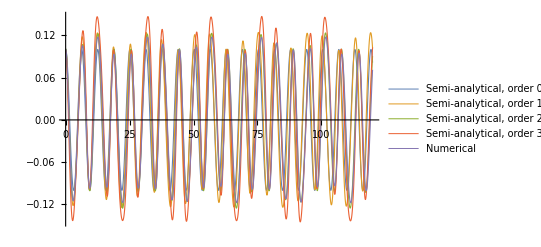

```mathematica
listOfFunctions = Flatten[{Table[xsoltnum[upToOrd][t],{upToOrd,0,nmax}],numSol x[t]}];
listOfLabels = Flatten[{Table["Semi-analytical, order " <>ToString[upToOrd],{upToOrd,0,nmax}],"Numerical"}];
Plot[listOfFunctions,{t,0,120},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002]]
```

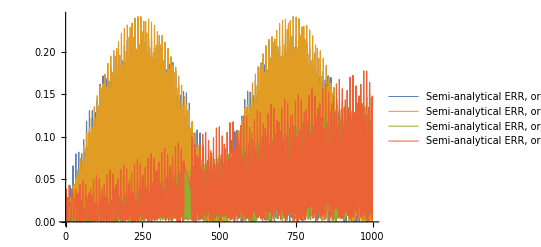

```mathematica
listOfFunctions = Flatten[Table[Abs[xsoltnum[upToOrd][t]-numSol x[t]],{upToOrd,0,nmax}]];
listOfLabels = Flatten[Table["Semi-analytical ERR, order " <>ToString[upToOrd],{upToOrd,0,nmax}]];
Plot[listOfFunctions,{t,0,1000},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002]]
```